```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adityak/Aditya/git/root_tracking/Mathematica/SRSPM/Singularity_event

## Required libraries and functions:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

## Architecture of the SRSPM:

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
(b)[[2]]
```

{rb Cos[2 γb],rb Sin[2 γb],0}

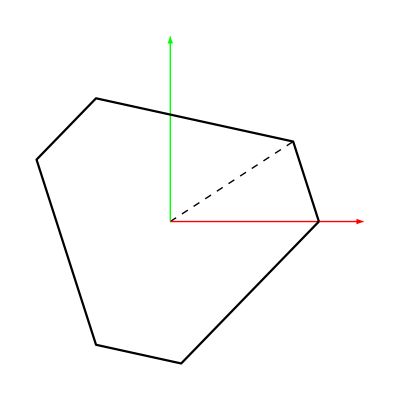

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

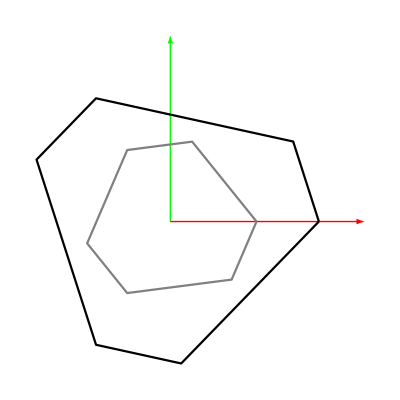

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

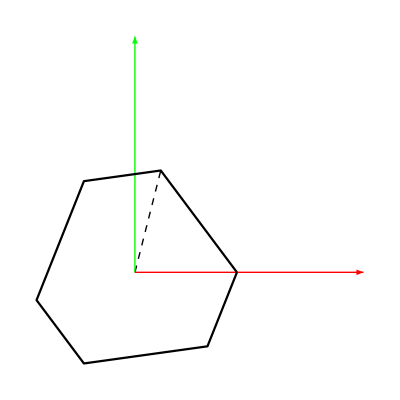

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (al/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

```mathematica
b/.datap
```

{{1,0,0},{0.827026,0.562164,0},{-1/2,(√3)/2,0},{-0.900361,0.435143,0},{-1/2,-(√3)/2,0},{0.0733353,-0.997307,0}}

```mathematica
cords = {"x", "y", "z"};
```

```mathematica
acords = Table[Table[Symbol["a"<>ToString[j]<>cords[[i]]],{i, 3}],{j, 6}]
```

{{a1x,a1y,a1z},{a2x,a2y,a2z},{a3x,a3y,a3z},{a4x,a4y,a4z},{a5x,a5y,a5z},{a6x,a6y,a6z}}

```mathematica
Inner[Rule, Flatten[acords], Flatten[b/.datap], List]
```

{a1x→1,a1y→0,a1z→0,a2x→0.827026,a2y→0.562164,a2z→0,a3x→-1/2,a3y→(√3)/2,a3z→0,a4x→-0.900361,a4y→0.435143,a4z→0,a5x→-1/2,a5y→-(√3)/2,a5z→0,a6x→0.0733353,a6y→-0.997307,a6z→0}

## Inverse Kinematics:

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}]; (*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0.2,0,1.28,0.2,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]]-(l[[i]]*Sin[ψ[[i]]]))/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]]+(l[[i]]*Cos[ψ[[i]]] *Sin[ϕ[[i]]]))/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{l1, _Complex},{l2, _Complex},{l3, _Complex},{l4, _Complex},{l5, _Complex},{l6, _Complex}}, Evaluate[ψ/.ψval/.Inner[Rule,l,{l1,l2,l3,l4,l5,l6},List]]];
```

```mathematica
ψ/.ψval/.lval/.samplex
```

{0.,0.0279909,0.257139,0.407655,-0.333318,-0.4622}

```mathematica
cψval@@Join[(qx/.samplex),l/.lval/.samplex]
```

{-1.5708+0. ⅈ,0.0279909+2.17503×10^-17 ⅈ,0.257139-1.40253×10^-16 ⅈ,0.407655+1.83772×10^-17 ⅈ,-0.333318-1.16914×10^-16 ⅈ,-0.4622-2.00231×10^-16 ⅈ}

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]]+l[[i]]*Cos[ψ[[i]]]* Sin[ϕ[[i]]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{ψ1, _Complex},{ψ2, _Complex},{ψ3, _Complex},{ψ4, _Complex},{ψ5, _Complex},{ψ6, _Complex}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
(atp-aj)/.ϕval/.ψval/.lval/.bsrules/.datap/.samplex
```

{{0.,0.,0.},{0.,-4.16334×10^-17,-1.94289×10^-16},{-5.55112×10^-17,-1.11022×10^-16,-2.498×10^-16},{-1.66533×10^-16,0.,7.63278×10^-17},{-1.11022×10^-16,0.,-1.94289×10^-16},{-1.11022×10^-16,0.,-1.11022×10^-16}}

```mathematica
iksolC[x_] := Module[{lvals, ψvals, ϕvals, xrule, lrule, ψrule},
xrule = Inner[Rule, qx, x, List];
lvals = l/.lval/.xrule;
lrule = Inner[Rule, l, lvals, List];
ψvals = ψ/.ψval/.Join[xrule, lrule];
ψrule = Inner[Rule, ψ, ψvals, List];
ϕvals = ϕ/.ϕval/.Join[xrule,ψrule];
Return[Join[ϕvals, ψvals, lvals]]
]
```

```mathematica
iksolC[qx/.samplex]
```

{-0.169984,-0.310482,0.271327,0.41686,0.360652,0.447679,0.,0.0279909,0.257139,0.407655,-0.333318,-0.4622,1.29872,1.57164,1.58122,1.45458,1.22907,1.39188}

### FK roots for leg lengths {1.29872,1.57164,1.58122,1.45458,1.22907,1.39188}

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
(* Only the real roots *)
roots = {{x->-0.5667492693067395,y->-0.47361433252222773,z->0.6585130434781568,c1->-1.147484922943516,c2->-0.3916813771758316,c3->0.2884677631589457},{x->0.6437068343767637,y->-0.352393621147875,z->-0.868576798805674,c1->-0.6371495097873141,c2->0.39736849892201814,c3->0.0979861139712377},{x->-0.21629297012068094,y->0.430242686569929,z->-1.0374959771743533,c1->-0.40783877504548416,c2->-0.6066186988620645,c3->0.09225868196288778},{x->0.19999999999999962,y->0,z->-1.28,c1->-0.2,c2->0,c3->0},{x->0.19999999999999962,y->0,z->1.28,c1->0.2,c2->0,c3->0},{x->-0.21629297012068094,y->0.430242686569929,z->1.0374959771743533,c1->0.40783877504548416,c2->0.6066186988620645,c3->0.09225868196288778},{x->0.6437068343767637,y->-0.352393621147875,z->0.868576798805674,c1->0.6371495097873141,c2->-0.39736849892201814,c3->0.0979861139712377},{x->-0.5667492693067395,y->-0.47361433252222773,z->-0.6585130434781568,c1->1.147484922943516,c2->0.3916813771758316,c3->0.2884677631589457}};
```

```mathematica
(* Only the complex roots *)
rootsC = {{x->-0.05911145667502127-0.129136108289369 ⅈ,y->-0.1422804325207781-0.02876450342879286 ⅈ,z->0.1047185166403552+0.3134727864613459 ⅈ,c1->-1.2693960456284825-0.18341903687232775 ⅈ,c2->-0.4288776735782819-0.16099483147047725 ⅈ,c3->2.3780340651794107-0.14526633596509228 ⅈ},{x->-0.05911145667502127+0.129136108289369 ⅈ,y->-0.1422804325207781+0.02876450342879286 ⅈ,z->0.1047185166403552-0.3134727864613459 ⅈ,c1->-1.2693960456284825+0.18341903687232775 ⅈ,c2->-0.4288776735782819+0.16099483147047725 ⅈ,c3->2.3780340651794107+0.14526633596509228 ⅈ},{x->-0.07254517345004197+0. ⅈ,y->-0.6056401101876541+0. ⅈ,z->0.+1.0926098236185229 ⅈ,c1->0.-0.09149250333580622 ⅈ,c2->0.+1.8830664020270929 ⅈ,c3->3.2592940042363074},{x->-0.07254517345004197+0. ⅈ,y->-0.6056401101876541+0. ⅈ,z->0.-1.0926098236185229 ⅈ,c1->0.+0.09149250333580622 ⅈ,c2->0.-1.8830664020270929 ⅈ,c3->3.2592940042363074},{x->0.8373968994328096+0. ⅈ,y->-1.671059889184249+0. ⅈ,z->0.+0.7256359519946276 ⅈ,c1->0.-0.23606574410675318 ⅈ,c2->0.-0.6901528187831717 ⅈ,c3->-0.09949955255202442},{x->0.8373968994328096+0. ⅈ,y->-1.671059889184249+0. ⅈ,z->0.-0.7256359519946276 ⅈ,c1->0.+0.23606574410675318 ⅈ,c2->0.+0.6901528187831717 ⅈ,c3->-0.09949955255202442},{x->1.3328248876244597+0. ⅈ,y->2.0633822173662515+0. ⅈ,z->0.-2.354015836127429 ⅈ,c1->0.-0.2369651343289844 ⅈ,c2->0.+2.47763949583596 ⅈ,c3->-0.8551750969591563},{x->1.3328248876244597+0. ⅈ,y->2.0633822173662515+0. ⅈ,z->0.+2.354015836127429 ⅈ,c1->0.+0.2369651343289844 ⅈ,c2->0.-2.47763949583596 ⅈ,c3->-0.8551750969591563},{x->-2.3418055961259334+0. ⅈ,y->-0.6725807932284853+0. ⅈ,z->0.+1.555598060857994 ⅈ,c1->0.-0.3707073717653359 ⅈ,c2->0.+0.6986850965026454 ⅈ,c3->-0.11513233057257073},{x->-2.3418055961259334+0. ⅈ,y->-0.6725807932284853+0. ⅈ,z->0.-1.555598060857994 ⅈ,c1->0.+0.3707073717653359 ⅈ,c2->0.-0.6986850965026454 ⅈ,c3->-0.11513233057257073},{x->0.8678512490762014+0. ⅈ,y->1.5302728315543683+0. ⅈ,z->0.-0.531487951031281 ⅈ,c1->0.-0.7044607449755088 ⅈ,c2->0.-0.034815542070259865 ⅈ,c3->-0.09368147745764965},{x->0.8678512490762014+0. ⅈ,y->1.5302728315543683+0. ⅈ,z->0.+0.531487951031281 ⅈ,c1->0.+0.7044607449755088 ⅈ,c2->0.+0.034815542070259865 ⅈ,c3->-0.09368147745764965},{x->-0.19289447947986194+0. ⅈ,y->0.12030205772730718+0. ⅈ,z->0.-0.8138746856567388 ⅈ,c1->0.-0.9304259840383785 ⅈ,c2->0.+1.1062397919832856 ⅈ,c3->3.0598560090553466},{x->-0.19289447947986194+0. ⅈ,y->0.12030205772730718+0. ⅈ,z->0.+0.8138746856567388 ⅈ,c1->0.+0.9304259840383785 ⅈ,c2->0.-1.1062397919832856 ⅈ,c3->3.0598560090553466},{x->-2.489355898688626+0. ⅈ,y->0.2529423920236149+0. ⅈ,z->0.-2.4815262725457936 ⅈ,c1->0.-1.4015836180942756 ⅈ,c2->0.-1.0937071918421204 ⅈ,c3->-0.4890990746078041},{x->-2.489355898688626+0. ⅈ,y->0.2529423920236149+0. ⅈ,z->0.+2.4815262725457936 ⅈ,c1->0.+1.4015836180942756 ⅈ,c2->0.+1.0937071918421204 ⅈ,c3->-0.4890990746078041},{x->-0.05911145667502127+0.129136108289369 ⅈ,y->-0.1422804325207781+0.02876450342879286 ⅈ,z->-0.1047185166403552+0.3134727864613459 ⅈ,c1->1.2693960456284825-0.18341903687232775 ⅈ,c2->0.4288776735782819-0.16099483147047725 ⅈ,c3->2.3780340651794107+0.14526633596509228 ⅈ},{x->-0.05911145667502127-0.129136108289369 ⅈ,y->-0.1422804325207781-0.02876450342879286 ⅈ,z->-0.1047185166403552-0.3134727864613459 ⅈ,c1->1.2693960456284825+0.18341903687232775 ⅈ,c2->0.4288776735782819+0.16099483147047725 ⅈ,c3->2.3780340651794107-0.14526633596509228 ⅈ}};
```

### Verifying if the IK roots are correct:

```mathematica
ikroots = Table[Inner[Rule, Join[ϕ, ψ, l], iksolC[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
ikroots//MatrixForm
```

(ϕ1→-1.01066 | ϕ2→-1.47858 | ϕ3→-1.0161 | ϕ4→-0.178921 | ϕ5→-0.310817 | ϕ6→-0.317634 | ψ1→0.106616 | ψ2→0.69378 | ψ3→1.39147 | ψ4→0.99173 | ψ5→-0.224175 | ψ6→-0.613704 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→3.05861 | ϕ2→-2.91523 | ϕ3→2.57288 | ϕ4→1.91859 | ϕ5→1.84199 | ϕ6→2.20924 | ψ1→0.367715 | ψ2→0.44655 | ψ3→0.624152 | ψ4→0.541297 | ψ5→-0.275016 | ψ6→-0.269816 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-2.15628 | ϕ2→-2.54772 | ϕ3→2.9907 | ϕ4→2.87787 | ϕ5→3.10569 | ϕ6→-2.82383 | ψ1→-0.556272 | ψ2→-0.235658 | ψ3→0.110831 | ψ4→0.257131 | ψ5→-0.687379 | ψ6→-1.19292 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-2.97161 | ϕ2→-2.83111 | ϕ3→2.87027 | ϕ4→2.72473 | ϕ5→2.78094 | ϕ6→2.69391 | ψ1→0. | ψ2→0.0279909 | ψ3→0.257139 | ψ4→0.407655 | ψ5→-0.333318 | ψ6→-0.4622 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-0.169984 | ϕ2→-0.310482 | ϕ3→0.271327 | ϕ4→0.41686 | ϕ5→0.360652 | ϕ6→0.447679 | ψ1→0. | ψ2→0.0279909 | ψ3→0.257139 | ψ4→0.407655 | ψ5→-0.333318 | ψ6→-0.4622 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-0.985314 | ϕ2→-0.593871 | ϕ3→0.150897 | ϕ4→0.263724 | ϕ5→0.0358998 | ϕ6→-0.317765 | ψ1→-0.556272 | ψ2→-0.235658 | ψ3→0.110831 | ψ4→0.257131 | ψ5→-0.687379 | ψ6→-1.19292 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→0.0829858 | ϕ2→-0.226367 | ϕ3→0.568713 | ϕ4→1.223 | ϕ5→1.29961 | ϕ6→0.932351 | ψ1→0.367715 | ψ2→0.44655 | ψ3→0.624152 | ψ4→0.541297 | ψ5→-0.275016 | ψ6→-0.269816 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188
ϕ1→-2.13093 | ϕ2→-1.66301 | ϕ3→-2.1255 | ϕ4→-2.96267 | ϕ5→-2.83078 | ϕ6→-2.82396 | ψ1→0.106616 | ψ2→0.69378 | ψ3→1.39147 | ψ4→0.99173 | ψ5→-0.224175 | ψ6→-0.613704 | l1→1.29872 | l2→1.57164 | l3→1.58122 | l4→1.45458 | l5→1.22907 | l6→1.39188)

```mathematica
(*iksolC[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]*)
```

```mathematica
initpose=Join[qx/.roots[[5]],iksolC[qx/.roots[[5]]]];
initposes=Table[Join[qx/.roots[[ii]],iksolC[qx/.roots[[ii]]]],{ii,8}];
initposeC[n_]:= Module[{},Return[Join[qx/.rootsC[[n]],iksolC[qx/.rootsC[[n]]]]];];
```

```mathematica
xbrule = Table[{Symbol["xb"<>ToString[i]], Symbol["yb"<>ToString[i]], Symbol["zb"<>ToString[i]]},{i, 1, 6}];
xtrule = Table[{Symbol["xt"<>ToString[i]], Symbol["yt"<>ToString[i]], Symbol["zt"<>ToString[i]]},{i, 1, 6}];
```

```mathematica
top = Table[Inner[Rule, xtrule[[i]], (a/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xt1→-0.0940062,yt1→-0.138202,zt1→0.68609},{xt2→-0.376171,yt2→-0.442818,zt2→0.111266},{xt3→-0.739752,yt3→-0.689841,zt3→0.148548},{xt4→-1.04203,yt4→-0.782303,zt4→0.783302},{xt5→-0.86649,yt5→-0.5928,zt5→1.1409},{xt6→-0.282052,yt6→-0.195722,zt6→1.08097}}

```mathematica
base = Table[Inner[Rule, xbrule[[i]], (b/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xb1→1,yb1→0,zb1→0},{xb2→0.827026,yb2→0.562164,zb2→0},{xb3→-1/2,yb3→(√3)/2,zb3→0},{xb4→-0.900361,yb4→0.435143,zb4→0},{xb5→-1/2,yb5→-(√3)/2,zb5→0},{xb6→0.0733353,yb6→-0.997307,zb6→0}}

```mathematica
roots[[5]]
```

{x→0.2,y→0,z→1.28,c1→0.2,c2→0,c3→0}

```mathematica
Rationalize[base, 0.01]
```

{{xb1→1,yb1→0,zb1→0},{xb2→5/6,yb2→4/7,zb2→0},{xb3→-1/2,yb3→(√3)/2,zb3→0},{xb4→-9/10,yb4→3/7,zb4→0},{xb5→-1/2,yb5→-(√3)/2,zb5→0},{xb6→1/13,yb6→-1,zb6→0}}

```mathematica
Max[Table[ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.ikroots[[i]], {i, Length[ikroots]}]];
```

```mathematica
roots//Dimensions
```

{8,6}

```mathematica
(*All the roots satisfy our constraint equation*)
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

## Compiled functions

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
qfull = Join[qx, qvar];
```

```mathematica
cηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηconfig/.qrule], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηconfig = D[ηconfig/.qrule,{ q[[;;-7]]/.qrule}];
```

```mathematica
cJηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηconfig], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
cηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηext = D[ηext,{ Join[qx, q[[;;-7]]/.qrule]}];
```

```mathematica
Jηext//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
cJηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

## Plotting the SRSPM:

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*Min[lb/.leglparam,Norm[tempvec[[i]]]]}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
(*Plotting the constraints*)
```

```mathematica
plotconstraints[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis, constraints, oval, pts},
oval=5;
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3/oval],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, 2,6}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85/oval],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, 2,6}];
(*Joints*)
jointsbase = Table[Graphics3D[{Opacity[1/oval],Sphere[bval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];
jointstop = Table[Graphics3D[{Opacity[1/oval],Sphere[aval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting constraints*)
constraints = Show[Graphics3D[{Gray,Arrowheads[0.04],Arrow[Tube[{{0,0,0},bval[[1]]},0.025]]}], Graphics3D[{Purple,Arrowheads[0.045],Arrow[Tube[{bval[[1]], (aval/.qvals)[[1]]},0.025]]}], Graphics3D[{Black,Arrowheads[0.045],Arrow[Tube[{(aval/.qvals)[[1]], {x,y,z}/.qvals},0.025]]}], Graphics3D[{Brown,Arrowheads[0.045],Arrow[Tube[{{0,0,0}, {x,y,z}/.qvals},0.025]]}]];
(*Mid points*)
pts = Show[Graphics3D[{Red, Opacity[0.5],Sphere[{0,0,0}, 0.06]}], Graphics3D[{Red, Opacity[0.5],Sphere[Mean[aval/.qvals], 0.06]}]];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis, constraints, pts]
]
```

```mathematica
pt = {0.2,0.2,1.1,0.1,0,0}
cpose = Inner[Rule, qfull,  Join[pt, iksolC[pt]], List];
plotconstraints[Chop[cpose]]
```

{0.2,0.2,1.1,0.1,0,0}

-Graphics3D-

```mathematica
plotsrspm[Chop[Inner[Rule, qfull, initpose, List]]]
```

-Graphics3D-

## Path generation

```mathematica
(* Select a circle, do the IK and get the values and fit a function to those leg values. Now track these functions with other initial conditions *)
```

```mathematica
scale = 0.2;
```

```mathematica
(* Circular path with changing orientation *)
(* parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*Cos[α], scale*Sin[α],scale*Sin[2*α]}; *)

(* Circular path with constant orientation *)
(* parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0}; *)

(* Straight line path moving towards singularity *)
parampath = {scale-α,α, 1.28-α, scale*1, scale*0,scale*0};
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, π/3, π/300}];
```

```mathematica
iksolC[pathpts[[1]]][[-6;;]]
```

{1.29872,1.57164,1.58122,1.45458,1.22907,1.39188}

```mathematica
pathplt=Graphics3D[{Red, Sphere[Chop[pathpts[[;;]]][[1;;Length[pathpts], ;;3]], 0.025]}];
```

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Selected pose for plotting*)
```

```mathematica
(*plotsrspm[Inner[Rule, qfull, Join[pathpts[[43]], iksol[pathpts[[43]]]], List]]*)
```

```mathematica
(*get all the leg array for the circular motion*)
```

```mathematica
(*legvals = Table[Join[{i-1}, {iksol[pathpts[[i]]][[-6;;]]}], {i, Length[pathpts]}];*)
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
legvals[[1]]
```

{1.29872,1.57164,1.58122,1.45458,1.22907,1.39188}

```mathematica
initpose=Join[pathpts[[1]], iksolC[pathpts[[1]]]]
```

{0.2,0,1.28,0.2,0.,0.,-0.169984,-0.310482,0.271327,0.41686,0.360652,0.447679,0.,0.0279909,0.257139,0.407655,-0.333318,-0.4622,1.29872,1.57164,1.58122,1.45458,1.22907,1.39188}

```mathematica
(*legvals//MatrixForm*)
(*legvals//Im//Flatten//CForm*)
```

```mathematica
(*legfunc = Interpolation[legvals]*)
```

## Singularity manifold

### From Anirban’s codes:

```mathematica
orientrule={c1->0.2,c2-> 0,c3-> 0}
```

{c1→0.2,c2→0,c3→0}

```mathematica
transrule=Inner[Rule,{x,y,z},Transpose[rotZ[(2π/3-2*0.2985)/2]].{x,y,z},List]
```

{x→0.732576 x+0.680685 y,y→-0.680685 x+0.732576 y,z→z}

```mathematica
g11 = ToExpression[Import["srspm_pos_eq1.txt"]]
```

-0.00341743+0.00814255 x+0.00455343 y-0.000386999 x y+0.00914266 y^2+0.0392729 z-0.011209 x z-0.0571752 y z-0.0101202 x y z-0.0269848 y^2 z-0.0118007 z^2+0.0242884 x z^2+0.199687 y z^2-0.323817 z^3

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->Green,PlotPoints->60];
```

```mathematica
xpose = {0.2,0,1.28,0.2,0,0};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp,pathplt]
```

-Graphics3D-

### Checking if Det[Jηext] is 0 for random points on g11

```mathematica
randomnumbers=100;
xrandom=RandomReal[{-1.6,1.6},randomnumbers];
yrandom=RandomReal[{-1.6,1.6},randomnumbers];
zrandom=Table[z/.Solve[(g11/.Inner[Rule,{x,y},{xrandom[[ii]],yrandom[[ii]]},List])==0],{ii,randomnumbers}];
ptsrandom=Flatten[Table[Table[{xrandom[[ii]],yrandom[[ii]],zrandom[[ii]][[jj]]},{jj,3}],{ii,randomnumbers}],1];
randrule=Table[Inner[Rule,{x,y,z},ptsrandom[[ii]],List],{ii,randomnumbers}];
```

```mathematica
(* Checking if the obtained points lie on g11=0 *)
Table[g11/.randrule[[ii]],{ii,randomnumbers}]//Abs//Max
```

9.71445×10^-17

```mathematica
(* Checking if the random configurations satisfy the constraints *)
Table[Norm[cηext@@Join[({x,y,z,0.2,0,0}/.randrule[[ii]]),iksolC[({x,y,z,0.2,0,0}/.randrule[[ii]])]]],{ii,randomnumbers}]//Max
```

1.78384×10^-15

```mathematica
(* Now evaluating Det[Jηext] for these random points *)
randomDet=Table[Det[cJηext@@Join[({x,y,z,0.2,0,0}/.randrule[[ii]]),iksolC[({x,y,z,0.2,0,0}/.randrule[[ii]])]]],{ii,randomnumbers}]//Chop;
randomDet
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Newton-Raphson method for root tracking

## Real roots:

```mathematica
(*Now root tracking all the 8 solutions with this leg interpolation for the 50 points*)
```

```mathematica
(*Newton-Raphson method*)
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[(Norm[nvec]≥ 10^-10)&&(loopcounter≤100),
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*Tracking using the extended configuration space*)
```

```mathematica
Jηext//Dimensions
Jηext//Variables
```

{18,18}

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

### Root 1:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[1,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

8.90777×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[1,;;-7]];
tic[]
r1tempϕ = testext;
r1ϕlist = {r1tempϕ};
For[i=2,i≤Length[legvals], i++,
r1tempϕ = NRTracking[legvals[[i]], r1tempϕ, cηext, cJηext];
AppendTo[r1ϕlist, r1tempϕ];
]
toc[]
```

Actual time consumed: 0.01593 seconds.

CPU time consumed: 0.015943 seconds.

```mathematica
r1xlist = r1ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r1trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r1xlist[[u]], iksolC[r1xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r1xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r1xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 2:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[2,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

6.58135×10^-16

```mathematica
(*Root tracking in the extended space*)
testext = initposes[[2,;;-7]];
tic[]
r2tempϕ = testext;
r2ϕlist = {r2tempϕ};
For[i=2,i≤Length[legvals], i++, 
r2tempϕ = NRTracking[legvals[[i]], r2tempϕ, cηext, cJηext];
AppendTo[r2ϕlist, r2tempϕ];
]
toc[]
```

Actual time consumed: 0.01795 seconds.

CPU time consumed: 0.017969 seconds.

```mathematica
r2xlist = r2ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r2trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r2xlist[[u]], iksolC[r2xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r2xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r2xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 3:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[3,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

5.15957×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[3,;;-7]];
tic[]
r3tempϕ = testext;
r3ϕlist = {r3tempϕ};
For[i=2,i≤Length[legvals], i++, 
r3tempϕ = NRTracking[legvals[[i]], r3tempϕ, cηext, cJηext];
AppendTo[r3ϕlist, r3tempϕ];
]
toc[]
```

Actual time consumed: 0.01795 seconds.

CPU time consumed: 0.017969 seconds.

```mathematica
r3xlist = r3ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r3trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r3xlist[[u]], iksolC[r3xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r3xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r3xlist], 1}]
```

```mathematica
r3xlist//MatrixForm
```

(-0.216293 | 0.430243 | -1.0375 | -0.407839 | -0.606619 | 0.0922587
-0.221812+0. ⅈ | 0.429298+0. ⅈ | -1.026+0. ⅈ | -0.404595+0. ⅈ | -0.595464+0. ⅈ | 0.089159+0. ⅈ
-0.227251+0. ⅈ | 0.428465+0. ⅈ | -1.01459+0. ⅈ | -0.401374+0. ⅈ | -0.58444+0. ⅈ | 0.0861517+0. ⅈ
-0.232613+0. ⅈ | 0.427745+0. ⅈ | -1.00328+0. ⅈ | -0.398176+0. ⅈ | -0.573544+0. ⅈ | 0.0832338+0. ⅈ
-0.237903+0. ⅈ | 0.427141+0. ⅈ | -0.992072+0. ⅈ | -0.395+0. ⅈ | -0.562772+0. ⅈ | 0.0804023+0. ⅈ
-0.243125+0. ⅈ | 0.426656+0. ⅈ | -0.980964+0. ⅈ | -0.391847+0. ⅈ | -0.552122+0. ⅈ | 0.0776543+0. ⅈ
-0.248282+0. ⅈ | 0.426291+0. ⅈ | -0.969959+0. ⅈ | -0.388718+0. ⅈ | -0.54159+0. ⅈ | 0.0749873+0. ⅈ
-0.253378+0. ⅈ | 0.42605+0. ⅈ | -0.959059+0. ⅈ | -0.385612+0. ⅈ | -0.531174+0. ⅈ | 0.0723986+0. ⅈ
-0.258418+0. ⅈ | 0.425936+0. ⅈ | -0.948265+0. ⅈ | -0.38253+0. ⅈ | -0.520872+0. ⅈ | 0.069886+0. ⅈ
-0.263403+0. ⅈ | 0.425951+0. ⅈ | -0.93758+0. ⅈ | -0.379472+0. ⅈ | -0.51068+0. ⅈ | 0.0674471+0. ⅈ
-0.26834+0. ⅈ | 0.426097+0. ⅈ | -0.927004+0. ⅈ | -0.376439+0. ⅈ | -0.500597+0. ⅈ | 0.0650799+0. ⅈ
-0.27323+0. ⅈ | 0.426377+0. ⅈ | -0.916539+0. ⅈ | -0.373431+0. ⅈ | -0.490621+0. ⅈ | 0.0627821+0. ⅈ
-0.278078+0. ⅈ | 0.426794+0. ⅈ | -0.906186+0. ⅈ | -0.370448+0. ⅈ | -0.480749+0. ⅈ | 0.0605519+0. ⅈ
-0.282887+0. ⅈ | 0.42735+0. ⅈ | -0.895946+0. ⅈ | -0.36749+0. ⅈ | -0.470981+0. ⅈ | 0.0583874+0. ⅈ
-0.287661+0. ⅈ | 0.428048+0. ⅈ | -0.88582+0. ⅈ | -0.364559+0. ⅈ | -0.461314+0. ⅈ | 0.0562868+0. ⅈ
-0.292403+0. ⅈ | 0.428891+0. ⅈ | -0.875809+0. ⅈ | -0.361653+0. ⅈ | -0.451746+0. ⅈ | 0.0542484+0. ⅈ
-0.297117+0. ⅈ | 0.42988+0. ⅈ | -0.865914+0. ⅈ | -0.358774+0. ⅈ | -0.442277+0. ⅈ | 0.0522704+0. ⅈ
-0.301806+0. ⅈ | 0.431019+0. ⅈ | -0.856134+0. ⅈ | -0.355921+0. ⅈ | -0.432904+0. ⅈ | 0.0503514+0. ⅈ
-0.306474+0. ⅈ | 0.432309+0. ⅈ | -0.846471+0. ⅈ | -0.353096+0. ⅈ | -0.423627+0. ⅈ | 0.0484898+0. ⅈ
-0.311123+0. ⅈ | 0.433753+0. ⅈ | -0.836925+0. ⅈ | -0.350297+0. ⅈ | -0.414444+0. ⅈ | 0.0466842+0. ⅈ
-0.315759+0. ⅈ | 0.435352+0. ⅈ | -0.827496+0. ⅈ | -0.347526+0. ⅈ | -0.405355+0. ⅈ | 0.044933+0. ⅈ
-0.320382+0. ⅈ | 0.437111+0. ⅈ | -0.818183+0. ⅈ | -0.344783+0. ⅈ | -0.396359+0. ⅈ | 0.043235+0. ⅈ
-0.324998+0. ⅈ | 0.439029+0. ⅈ | -0.808987+0. ⅈ | -0.342068+0. ⅈ | -0.387453+0. ⅈ | 0.0415889+0. ⅈ
-0.329608+0. ⅈ | 0.441109+0. ⅈ | -0.799908+0. ⅈ | -0.339381+0. ⅈ | -0.378639+0. ⅈ | 0.0399933+0. ⅈ
-0.334217+0. ⅈ | 0.443353+0. ⅈ | -0.790945+0. ⅈ | -0.336722+0. ⅈ | -0.369914+0. ⅈ | 0.038447+0. ⅈ
-0.338826+0. ⅈ | 0.445763+0. ⅈ | -0.782097+0. ⅈ | -0.334091+0. ⅈ | -0.361279+0. ⅈ | 0.0369488+0. ⅈ
-0.34344+0. ⅈ | 0.448341+0. ⅈ | -0.773365+0. ⅈ | -0.33149+0. ⅈ | -0.352732+0. ⅈ | 0.0354976+0. ⅈ
-0.34806+0. ⅈ | 0.451087+0. ⅈ | -0.764747+0. ⅈ | -0.328916+0. ⅈ | -0.344274+0. ⅈ | 0.0340922+0. ⅈ
-0.352691+0. ⅈ | 0.454004+0. ⅈ | -0.756242+0. ⅈ | -0.326372+0. ⅈ | -0.335903+0. ⅈ | 0.0327316+0. ⅈ
-0.357334+0. ⅈ | 0.457092+0. ⅈ | -0.747849+0. ⅈ | -0.323856+0. ⅈ | -0.327619+0. ⅈ | 0.0314145+0. ⅈ
-0.361992+0. ⅈ | 0.460352+0. ⅈ | -0.739568+0. ⅈ | -0.321369+0. ⅈ | -0.319423+0. ⅈ | 0.03014+0. ⅈ
-0.366668+0. ⅈ | 0.463787+0. ⅈ | -0.731396+0. ⅈ | -0.31891+0. ⅈ | -0.311313+0. ⅈ | 0.0289071+0. ⅈ
-0.371365+0. ⅈ | 0.467396+0. ⅈ | -0.723333+0. ⅈ | -0.31648+0. ⅈ | -0.303289+0. ⅈ | 0.0277148+0. ⅈ
-0.376085+0. ⅈ | 0.47118+0. ⅈ | -0.715377+0. ⅈ | -0.314079+0. ⅈ | -0.295351+0. ⅈ | 0.026562+0. ⅈ
-0.380831+0. ⅈ | 0.47514+0. ⅈ | -0.707526+0. ⅈ | -0.311706+0. ⅈ | -0.2875+0. ⅈ | 0.0254478+0. ⅈ
-0.385605+0. ⅈ | 0.479277+0. ⅈ | -0.699779+0. ⅈ | -0.309361+0. ⅈ | -0.279734+0. ⅈ | 0.0243712+0. ⅈ
-0.390409+0. ⅈ | 0.48359+0. ⅈ | -0.692133+0. ⅈ | -0.307044+0. ⅈ | -0.272054+0. ⅈ | 0.0233314+0. ⅈ
-0.395245+0. ⅈ | 0.488081+0. ⅈ | -0.684588+0. ⅈ | -0.304754+0. ⅈ | -0.26446+0. ⅈ | 0.0223274+0. ⅈ
-0.400116+0. ⅈ | 0.492748+0. ⅈ | -0.67714+0. ⅈ | -0.302492+0. ⅈ | -0.256952+0. ⅈ | 0.0213582+0. ⅈ
-0.405024+0. ⅈ | 0.497592+0. ⅈ | -0.669787+0. ⅈ | -0.300257+0. ⅈ | -0.24953+0. ⅈ | 0.0204231+0. ⅈ
-0.40997+0. ⅈ | 0.502613+0. ⅈ | -0.662528+0. ⅈ | -0.298048+0. ⅈ | -0.242193+0. ⅈ | 0.0195212+0. ⅈ
-0.414958+0. ⅈ | 0.50781+0. ⅈ | -0.655361+0. ⅈ | -0.295865+0. ⅈ | -0.234943+0. ⅈ | 0.0186515+0. ⅈ
-0.419988+0. ⅈ | 0.513183+0. ⅈ | -0.648281+0. ⅈ | -0.293708+0. ⅈ | -0.227779+0. ⅈ | 0.0178132+0. ⅈ
-0.425062+0. ⅈ | 0.518731+0. ⅈ | -0.641288+0. ⅈ | -0.291575+0. ⅈ | -0.220702+0. ⅈ | 0.0170055+0. ⅈ
-0.430183+0. ⅈ | 0.524453+0. ⅈ | -0.634378+0. ⅈ | -0.289466+0. ⅈ | -0.213712+0. ⅈ | 0.0162275+0. ⅈ
-0.435352+0. ⅈ | 0.530349+0. ⅈ | -0.62755+0. ⅈ | -0.287381+0. ⅈ | -0.206809+0. ⅈ | 0.0154785+0. ⅈ
-0.44057+0. ⅈ | 0.536417+0. ⅈ | -0.620799+0. ⅈ | -0.285319+0. ⅈ | -0.199993+0. ⅈ | 0.0147576+0. ⅈ
-0.44584+0. ⅈ | 0.542657+0. ⅈ | -0.614124+0. ⅈ | -0.283278+0. ⅈ | -0.193265+0. ⅈ | 0.0140639+0. ⅈ
-0.451162+0. ⅈ | 0.549067+0. ⅈ | -0.607521+0. ⅈ | -0.281258+0. ⅈ | -0.186625+0. ⅈ | 0.0133968+0. ⅈ
-0.456539+0. ⅈ | 0.555646+0. ⅈ | -0.600987+0. ⅈ | -0.279258+0. ⅈ | -0.180073+0. ⅈ | 0.0127553+0. ⅈ
-0.461972+0. ⅈ | 0.562392+0. ⅈ | -0.59452+0. ⅈ | -0.277277+0. ⅈ | -0.173611+0. ⅈ | 0.0121388+0. ⅈ
-0.467462+0. ⅈ | 0.569303+0. ⅈ | -0.588116+0. ⅈ | -0.275314+0. ⅈ | -0.167238+0. ⅈ | 0.0115464+0. ⅈ
-0.473011+0. ⅈ | 0.576379+0. ⅈ | -0.581772+0. ⅈ | -0.273367+0. ⅈ | -0.160955+0. ⅈ | 0.0109773+0. ⅈ
-0.478619+0. ⅈ | 0.583617+0. ⅈ | -0.575485+0. ⅈ | -0.271436+0. ⅈ | -0.154763+0. ⅈ | 0.0104308+0. ⅈ
-0.484289+0. ⅈ | 0.591016+0. ⅈ | -0.569252+0. ⅈ | -0.269519+0. ⅈ | -0.148662+0. ⅈ | 0.00990609+0. ⅈ
-0.490022+0. ⅈ | 0.598574+0. ⅈ | -0.563069+0. ⅈ | -0.267615+0. ⅈ | -0.142652+0. ⅈ | 0.00940242+0. ⅈ
-0.495818+0. ⅈ | 0.606288+0. ⅈ | -0.556933+0. ⅈ | -0.265722+0. ⅈ | -0.136734+0. ⅈ | 0.00891905+0. ⅈ
-0.501679+0. ⅈ | 0.614156+0. ⅈ | -0.55084+0. ⅈ | -0.263839+0. ⅈ | -0.13091+0. ⅈ | 0.00845519+0. ⅈ
-0.507607+0. ⅈ | 0.622178+0. ⅈ | -0.544787+0. ⅈ | -0.261964+0. ⅈ | -0.125179+0. ⅈ | 0.00801012+0. ⅈ
-0.513602+0. ⅈ | 0.630349+0. ⅈ | -0.53877+0. ⅈ | -0.260095+0. ⅈ | -0.119541+0. ⅈ | 0.00758308+0. ⅈ
-0.519666+0. ⅈ | 0.638669+0. ⅈ | -0.532785+0. ⅈ | -0.258232+0. ⅈ | -0.113999+0. ⅈ | 0.00717334+0. ⅈ
-0.525799+0. ⅈ | 0.647134+0. ⅈ | -0.526828+0. ⅈ | -0.256372+0. ⅈ | -0.108552+0. ⅈ | 0.00678015+0. ⅈ
-0.532003+0. ⅈ | 0.655743+0. ⅈ | -0.520897+0. ⅈ | -0.254513+0. ⅈ | -0.103201+0. ⅈ | 0.00640279+0. ⅈ
-0.538279+0. ⅈ | 0.664494+0. ⅈ | -0.514986+0. ⅈ | -0.252654+0. ⅈ | -0.0979464+0. ⅈ | 0.00604052+0. ⅈ
-0.544628+0. ⅈ | 0.673383+0. ⅈ | -0.509091+0. ⅈ | -0.250792+0. ⅈ | -0.0927892+0. ⅈ | 0.00569263+0. ⅈ
-0.551051+0. ⅈ | 0.682408+0. ⅈ | -0.503209+0. ⅈ | -0.248925+0. ⅈ | -0.0877299+0. ⅈ | 0.00535841+0. ⅈ
-0.557548+0. ⅈ | 0.691567+0. ⅈ | -0.497335+0. ⅈ | -0.247051+0. ⅈ | -0.0827692+0. ⅈ | 0.00503713+0. ⅈ
-0.564121+0. ⅈ | 0.700858+0. ⅈ | -0.491465+0. ⅈ | -0.245169+0. ⅈ | -0.0779075+0. ⅈ | 0.0047281+0. ⅈ
-0.570771+0. ⅈ | 0.710278+0. ⅈ | -0.485594+0. ⅈ | -0.243275+0. ⅈ | -0.0731453+0. ⅈ | 0.00443061+0. ⅈ
-0.577499+0. ⅈ | 0.719824+0. ⅈ | -0.479718+0. ⅈ | -0.241368+0. ⅈ | -0.0684833+0. ⅈ | 0.00414399+0. ⅈ
-0.584305+0. ⅈ | 0.729494+0. ⅈ | -0.473832+0. ⅈ | -0.239444+0. ⅈ | -0.0639217+0. ⅈ | 0.00386754+0. ⅈ
-0.591189+0. ⅈ | 0.739285+0. ⅈ | -0.467931+0. ⅈ | -0.237503+0. ⅈ | -0.0594611+0. ⅈ | 0.0036006+0. ⅈ
-0.598154+0. ⅈ | 0.749196+0. ⅈ | -0.462011+0. ⅈ | -0.23554+0. ⅈ | -0.0551017+0. ⅈ | 0.00334251+0. ⅈ
-0.605199+0. ⅈ | 0.759222+0. ⅈ | -0.456065+0. ⅈ | -0.233554+0. ⅈ | -0.0508438+0. ⅈ | 0.0030926+0. ⅈ
-0.612326+0. ⅈ | 0.769363+0. ⅈ | -0.450089+0. ⅈ | -0.231542+0. ⅈ | -0.0466876+0. ⅈ | 0.00285024+0. ⅈ
-0.619533+0. ⅈ | 0.779615+0. ⅈ | -0.444077+0. ⅈ | -0.229501+0. ⅈ | -0.042633+0. ⅈ | 0.00261481+0. ⅈ
-0.626823+0. ⅈ | 0.789975+0. ⅈ | -0.438023+0. ⅈ | -0.227428+0. ⅈ | -0.0386801+0. ⅈ | 0.00238568+0. ⅈ
-0.634195+0. ⅈ | 0.800443+0. ⅈ | -0.431922+0. ⅈ | -0.225321+0. ⅈ | -0.0348287+0. ⅈ | 0.00216225+0. ⅈ
-0.64165+0. ⅈ | 0.811014+0. ⅈ | -0.425767+0. ⅈ | -0.223177+0. ⅈ | -0.0310785+0. ⅈ | 0.00194395+0. ⅈ
-0.649188+0. ⅈ | 0.821686+0. ⅈ | -0.419552+0. ⅈ | -0.220992+0. ⅈ | -0.0274292+0. ⅈ | 0.0017302+0. ⅈ
-0.656808+0. ⅈ | 0.832458+0. ⅈ | -0.413271+0. ⅈ | -0.218764+0. ⅈ | -0.0238801+0. ⅈ | 0.00152046+0. ⅈ
-0.664511+0. ⅈ | 0.843326+0. ⅈ | -0.406916+0. ⅈ | -0.21649+0. ⅈ | -0.0204305+0. ⅈ | 0.00131418+0. ⅈ
-0.672296+0. ⅈ | 0.854289+0. ⅈ | -0.400481+0. ⅈ | -0.214165+0. ⅈ | -0.0170794+0. ⅈ | 0.00111085+0. ⅈ
-0.680164+0. ⅈ | 0.865344+0. ⅈ | -0.393957+0. ⅈ | -0.211788+0. ⅈ | -0.0138258+0. ⅈ | 0.000909989+0. ⅈ
-0.688114+0. ⅈ | 0.876489+0. ⅈ | -0.387337+0. ⅈ | -0.209354+0. ⅈ | -0.0106684+0. ⅈ | 0.000711114+0. ⅈ
-0.696145+0. ⅈ | 0.887721+0. ⅈ | -0.380612+0. ⅈ | -0.20686+0. ⅈ | -0.00760543+0. ⅈ | 0.000513778+0. ⅈ
-0.704257+0. ⅈ | 0.899038+0. ⅈ | -0.373773+0. ⅈ | -0.204303+0. ⅈ | -0.00463516+0. ⅈ | 0.000317554+0. ⅈ
-0.711062+0. ⅈ | 0.911062+0. ⅈ | -0.368938+0. ⅈ | -0.2+0. ⅈ | 2.33405×10^-11+0. ⅈ | -1.62255×10^-12+0. ⅈ
-0.721534+0. ⅈ | 0.921534+0. ⅈ | -0.358466+0. ⅈ | -0.2+0. ⅈ | -2.49878×10^-13+0. ⅈ | 1.76006×10^-14+0. ⅈ
-0.729065+0. ⅈ | 0.933484+0. ⅈ | -0.352476+0. ⅈ | -0.196208+0. ⅈ | 0.00374286+0. ⅈ | -0.000268358+0. ⅈ
-0.737488+0. ⅈ | 0.945123+0. ⅈ | -0.345081+0. ⅈ | -0.193355+0. ⅈ | 0.00636755+0. ⅈ | -0.000463919+0. ⅈ
-0.745985+0. ⅈ | 0.956838+0. ⅈ | -0.337517+0. ⅈ | -0.190417+0. ⅈ | 0.00891419+0. ⅈ | -0.000660127+0. ⅈ
-0.754555+0. ⅈ | 0.968628+0. ⅈ | -0.329771+0. ⅈ | -0.187388+0. ⅈ | 0.0113872+0. ⅈ | -0.000857251+0. ⅈ
-0.763195+0. ⅈ | 0.980489+0. ⅈ | -0.321828+0. ⅈ | -0.184264+0. ⅈ | 0.0137916+0. ⅈ | -0.00105553+0. ⅈ
-0.771903+0. ⅈ | 0.992422+0. ⅈ | -0.313671+0. ⅈ | -0.181039+0. ⅈ | 0.0161335+0. ⅈ | -0.00125516+0. ⅈ
-0.780676+0. ⅈ | 1.00442+0. ⅈ | -0.305283+0. ⅈ | -0.177706+0. ⅈ | 0.0184197+0. ⅈ | -0.0014563+0. ⅈ
-0.789511+0. ⅈ | 1.0165+0. ⅈ | -0.296642+0. ⅈ | -0.174259+0. ⅈ | 0.0206584+0. ⅈ | -0.00165908+0. ⅈ
-0.798405+0. ⅈ | 1.02863+0. ⅈ | -0.287726+0. ⅈ | -0.170689+0. ⅈ | 0.0228596+0. ⅈ | -0.00186356+0. ⅈ
-0.807353+0. ⅈ | 1.04084+0. ⅈ | -0.278509+0. ⅈ | -0.166989+0. ⅈ | 0.0250348+0. ⅈ | -0.00206973+0. ⅈ
-0.816351+0. ⅈ | 1.05311+0. ⅈ | -0.268961+0. ⅈ | -0.163151+0. ⅈ | 0.0271984+0. ⅈ | -0.00227751+0. ⅈ
-0.825393+0. ⅈ | 1.06545+0. ⅈ | -0.259049+0. ⅈ | -0.159164+0. ⅈ | 0.0293681+0. ⅈ | -0.00248671+0. ⅈ)

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 4:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[4,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

7.44275×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[4,;;-7]];
tic[]
r4tempϕ = testext;
r4ϕlist = {r4tempϕ};
For[i=2,i≤Length[legvals], i++, 
r4tempϕ = NRTracking[legvals[[i]], r4tempϕ, cηext, cJηext];
AppendTo[r4ϕlist, r4tempϕ];
]
toc[]
```

Actual time consumed: 0.01818 seconds.

CPU time consumed: 0.01817 seconds.

```mathematica
r4xlist = r4ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r4trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r4xlist[[u]], iksolC[r4xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r4xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r4xlist], 1}]
```

```mathematica
r4xlist//MatrixForm
```

(0.2 | 0 | -1.28 | -0.2 | 0 | 0
0.189528+0. ⅈ | 0.010472+0. ⅈ | -1.26953+0. ⅈ | -0.2+0. ⅈ | -3.82405×10^-17+0. ⅈ | 2.10099×10^-16+0. ⅈ
0.179056+0. ⅈ | 0.020944+0. ⅈ | -1.25906+0. ⅈ | -0.2+0. ⅈ | -1.96433×10^-16+0. ⅈ | 1.30571×10^-16+0. ⅈ
0.168584+0. ⅈ | 0.0314159+0. ⅈ | -1.24858+0. ⅈ | -0.2+0. ⅈ | 6.92055×10^-17+0. ⅈ | 4.80945×10^-17+0. ⅈ
0.158112+0. ⅈ | 0.0418879+0. ⅈ | -1.23811+0. ⅈ | -0.2+0. ⅈ | -7.3068×10^-18+0. ⅈ | -3.24359×10^-16+0. ⅈ
0.14764+0. ⅈ | 0.0523599+0. ⅈ | -1.22764+0. ⅈ | -0.2+0. ⅈ | -3.66863×10^-16+0. ⅈ | -9.60407×10^-17+0. ⅈ
0.137168+0. ⅈ | 0.0628319+0. ⅈ | -1.21717+0. ⅈ | -0.2+0. ⅈ | -1.56162×10^-17+0. ⅈ | 1.92617×10^-16+0. ⅈ
0.126696+0. ⅈ | 0.0733038+0. ⅈ | -1.2067+0. ⅈ | -0.2+0. ⅈ | 6.98964×10^-17+0. ⅈ | -2.71481×10^-17+0. ⅈ
0.116224+0. ⅈ | 0.0837758+0. ⅈ | -1.19622+0. ⅈ | -0.2+0. ⅈ | -2.5669×10^-16+0. ⅈ | 4.36163×10^-16+0. ⅈ
0.105752+0. ⅈ | 0.0942478+0. ⅈ | -1.18575+0. ⅈ | -0.2+0. ⅈ | 6.7404×10^-18+0. ⅈ | 3.48371×10^-16+0. ⅈ
0.0952802+0. ⅈ | 0.10472+0. ⅈ | -1.17528+0. ⅈ | -0.2+0. ⅈ | 7.35351×10^-17+0. ⅈ | -3.06316×10^-16+0. ⅈ
0.0848083+0. ⅈ | 0.115192+0. ⅈ | -1.16481+0. ⅈ | -0.2+0. ⅈ | -2.25674×10^-16+0. ⅈ | -4.21652×10^-17+0. ⅈ
0.0743363+0. ⅈ | 0.125664+0. ⅈ | -1.15434+0. ⅈ | -0.2+0. ⅈ | -2.60527×10^-16+0. ⅈ | -1.68981×10^-16+0. ⅈ
0.0638643+0. ⅈ | 0.136136+0. ⅈ | -1.14386+0. ⅈ | -0.2+0. ⅈ | -4.60829×10^-17+0. ⅈ | -2.72269×10^-17+0. ⅈ
0.0533923+0. ⅈ | 0.146608+0. ⅈ | -1.13339+0. ⅈ | -0.2+0. ⅈ | -2.01801×10^-16+0. ⅈ | 2.19924×10^-16+0. ⅈ
0.0429204+0. ⅈ | 0.15708+0. ⅈ | -1.12292+0. ⅈ | -0.2+0. ⅈ | -1.08693×10^-16+0. ⅈ | 2.28607×10^-16+0. ⅈ
0.0324484+0. ⅈ | 0.167552+0. ⅈ | -1.11245+0. ⅈ | -0.2+0. ⅈ | -8.61438×10^-17+0. ⅈ | -2.15679×10^-16+0. ⅈ
0.0219764+0. ⅈ | 0.178024+0. ⅈ | -1.10198+0. ⅈ | -0.2+0. ⅈ | -3.89092×10^-16+0. ⅈ | 4.08504×10^-16+0. ⅈ
0.0115044+0. ⅈ | 0.188496+0. ⅈ | -1.0915+0. ⅈ | -0.2+0. ⅈ | 2.41571×10^-16+0. ⅈ | -1.05056×10^-16+0. ⅈ
0.00103247+0. ⅈ | 0.198968+0. ⅈ | -1.08103+0. ⅈ | -0.2+0. ⅈ | -2.39399×10^-16+0. ⅈ | 1.48435×10^-16+0. ⅈ
-0.00943951+0. ⅈ | 0.20944+0. ⅈ | -1.07056+0. ⅈ | -0.2+0. ⅈ | -1.24594×10^-16+0. ⅈ | 6.63937×10^-17+0. ⅈ
-0.0199115+0. ⅈ | 0.219911+0. ⅈ | -1.06009+0. ⅈ | -0.2+0. ⅈ | -4.03954×10^-16+0. ⅈ | 4.08977×10^-16+0. ⅈ
-0.0303835+0. ⅈ | 0.230383+0. ⅈ | -1.04962+0. ⅈ | -0.2+0. ⅈ | -1.14475×10^-17+0. ⅈ | -1.30669×10^-16+0. ⅈ
-0.0408554+0. ⅈ | 0.240855+0. ⅈ | -1.03914+0. ⅈ | -0.2+0. ⅈ | -1.1137×10^-16+0. ⅈ | 2.28651×10^-16+0. ⅈ
-0.0513274+0. ⅈ | 0.251327+0. ⅈ | -1.02867+0. ⅈ | -0.2+0. ⅈ | -2.31062×10^-16+0. ⅈ | -1.04311×10^-16+0. ⅈ
-0.0617994+0. ⅈ | 0.261799+0. ⅈ | -1.0182+0. ⅈ | -0.2+0. ⅈ | -3.60845×10^-16+0. ⅈ | 1.85541×10^-16+0. ⅈ
-0.0722714+0. ⅈ | 0.272271+0. ⅈ | -1.00773+0. ⅈ | -0.2+0. ⅈ | 3.21871×10^-16+0. ⅈ | -2.82753×10^-16+0. ⅈ
-0.0827433+0. ⅈ | 0.282743+0. ⅈ | -0.997257+0. ⅈ | -0.2+0. ⅈ | -1.3765×10^-16+0. ⅈ | -1.32999×10^-16+0. ⅈ
-0.0932153+0. ⅈ | 0.293215+0. ⅈ | -0.986785+0. ⅈ | -0.2+0. ⅈ | 1.65789×10^-17+0. ⅈ | 7.05362×10^-18+0. ⅈ
-0.103687+0. ⅈ | 0.303687+0. ⅈ | -0.976313+0. ⅈ | -0.2+0. ⅈ | -2.2155×10^-16+0. ⅈ | 3.92978×10^-17+0. ⅈ
-0.114159+0. ⅈ | 0.314159+0. ⅈ | -0.965841+0. ⅈ | -0.2+0. ⅈ | -1.34941×10^-16+0. ⅈ | 1.07998×10^-16+0. ⅈ
-0.124631+0. ⅈ | 0.324631+0. ⅈ | -0.955369+0. ⅈ | -0.2+0. ⅈ | 2.01576×10^-16+0. ⅈ | -3.29396×10^-16+0. ⅈ
-0.135103+0. ⅈ | 0.335103+0. ⅈ | -0.944897+0. ⅈ | -0.2+0. ⅈ | -1.03369×10^-16+0. ⅈ | -4.37245×10^-17+0. ⅈ
-0.145575+0. ⅈ | 0.345575+0. ⅈ | -0.934425+0. ⅈ | -0.2+0. ⅈ | -9.59217×10^-18+0. ⅈ | 8.54451×10^-17+0. ⅈ
-0.156047+0. ⅈ | 0.356047+0. ⅈ | -0.923953+0. ⅈ | -0.2+0. ⅈ | -9.41031×10^-18+0. ⅈ | 1.38004×10^-17+0. ⅈ
-0.166519+0. ⅈ | 0.366519+0. ⅈ | -0.913481+0. ⅈ | -0.2+0. ⅈ | -1.76441×10^-16+0. ⅈ | -5.04674×10^-17+0. ⅈ
-0.176991+0. ⅈ | 0.376991+0. ⅈ | -0.903009+0. ⅈ | -0.2+0. ⅈ | -1.76845×10^-16+0. ⅈ | -7.50183×10^-18+0. ⅈ
-0.187463+0. ⅈ | 0.387463+0. ⅈ | -0.892537+0. ⅈ | -0.2+0. ⅈ | 2.27083×10^-16+0. ⅈ | 1.60754×10^-16+0. ⅈ
-0.197935+0. ⅈ | 0.397935+0. ⅈ | -0.882065+0. ⅈ | -0.2+0. ⅈ | -4.82223×10^-16+0. ⅈ | 3.20147×10^-16+0. ⅈ
-0.208407+0. ⅈ | 0.408407+0. ⅈ | -0.871593+0. ⅈ | -0.2+0. ⅈ | -4.17828×10^-17+0. ⅈ | -5.49677×10^-17+0. ⅈ
-0.218879+0. ⅈ | 0.418879+0. ⅈ | -0.861121+0. ⅈ | -0.2+0. ⅈ | 3.63496×10^-16+0. ⅈ | -3.51664×10^-16+0. ⅈ
-0.229351+0. ⅈ | 0.429351+0. ⅈ | -0.850649+0. ⅈ | -0.2+0. ⅈ | 3.85309×10^-17+0. ⅈ | -5.59866×10^-18+0. ⅈ
-0.239823+0. ⅈ | 0.439823+0. ⅈ | -0.840177+0. ⅈ | -0.2+0. ⅈ | 4.16524×10^-16+0. ⅈ | -1.41069×10^-16+0. ⅈ
-0.250295+0. ⅈ | 0.450295+0. ⅈ | -0.829705+0. ⅈ | -0.2+0. ⅈ | 4.85838×10^-16+0. ⅈ | -4.09087×10^-16+0. ⅈ
-0.260767+0. ⅈ | 0.460767+0. ⅈ | -0.819233+0. ⅈ | -0.2+0. ⅈ | 2.66022×10^-16+0. ⅈ | -2.9132×10^-16+0. ⅈ
-0.271239+0. ⅈ | 0.471239+0. ⅈ | -0.808761+0. ⅈ | -0.2+0. ⅈ | -2.8911×10^-16+0. ⅈ | 1.40477×10^-17+0. ⅈ
-0.281711+0. ⅈ | 0.481711+0. ⅈ | -0.798289+0. ⅈ | -0.2+0. ⅈ | -2.72503×10^-16+0. ⅈ | 1.46794×10^-17+0. ⅈ
-0.292183+0. ⅈ | 0.492183+0. ⅈ | -0.787817+0. ⅈ | -0.2+0. ⅈ | -1.25398×10^-16+0. ⅈ | -1.90005×10^-16+0. ⅈ
-0.302655+0. ⅈ | 0.502655+0. ⅈ | -0.777345+0. ⅈ | -0.2+0. ⅈ | -2.56933×10^-17+0. ⅈ | -1.34799×10^-16+0. ⅈ
-0.313127+0. ⅈ | 0.513127+0. ⅈ | -0.766873+0. ⅈ | -0.2+0. ⅈ | -5.14785×10^-16+0. ⅈ | -1.88454×10^-16+0. ⅈ
-0.323599+0. ⅈ | 0.523599+0. ⅈ | -0.756401+0. ⅈ | -0.2+0. ⅈ | -8.17898×10^-16+0. ⅈ | -1.3834×10^-16+0. ⅈ
-0.334071+0. ⅈ | 0.534071+0. ⅈ | -0.745929+0. ⅈ | -0.2+0. ⅈ | -1.07455×10^-16+0. ⅈ | -4.39169×10^-16+0. ⅈ
-0.344543+0. ⅈ | 0.544543+0. ⅈ | -0.735457+0. ⅈ | -0.2+0. ⅈ | -6.44377×10^-16+0. ⅈ | -3.64701×10^-16+0. ⅈ
-0.355015+0. ⅈ | 0.555015+0. ⅈ | -0.724985+0. ⅈ | -0.2+0. ⅈ | -8.20273×10^-16+0. ⅈ | -4.81212×10^-16+0. ⅈ
-0.365487+0. ⅈ | 0.565487+0. ⅈ | -0.714513+0. ⅈ | -0.2+0. ⅈ | -6.22894×10^-16+0. ⅈ | -7.23857×10^-16+0. ⅈ
-0.375959+0. ⅈ | 0.575959+0. ⅈ | -0.704041+0. ⅈ | -0.2+0. ⅈ | -1.98179×10^-15+0. ⅈ | -4.98679×10^-16+0. ⅈ
-0.386431+0. ⅈ | 0.586431+0. ⅈ | -0.693569+0. ⅈ | -0.2+0. ⅈ | -2.12121×10^-15+0. ⅈ | -5.75585×10^-16+0. ⅈ
-0.396903+0. ⅈ | 0.596903+0. ⅈ | -0.683097+0. ⅈ | -0.2+0. ⅈ | -1.51161×10^-15+0. ⅈ | -8.69035×10^-16+0. ⅈ
-0.407375+0. ⅈ | 0.607375+0. ⅈ | -0.672625+0. ⅈ | -0.2+0. ⅈ | -2.82461×10^-15+0. ⅈ | -3.70437×10^-16+0. ⅈ
-0.417847+0. ⅈ | 0.617847+0. ⅈ | -0.662153+0. ⅈ | -0.2+0. ⅈ | -3.1795×10^-15+0. ⅈ | -2.49906×10^-16+0. ⅈ
-0.428319+0. ⅈ | 0.628319+0. ⅈ | -0.651681+0. ⅈ | -0.2+0. ⅈ | -3.9696×10^-15+0. ⅈ | -6.55942×10^-16+0. ⅈ
-0.438791+0. ⅈ | 0.638791+0. ⅈ | -0.641209+0. ⅈ | -0.2+0. ⅈ | -3.20666×10^-15+0. ⅈ | -7.80183×10^-16+0. ⅈ
-0.449262+0. ⅈ | 0.649262+0. ⅈ | -0.630738+0. ⅈ | -0.2+0. ⅈ | -6.59381×10^-15+0. ⅈ | 6.41257×10^-17+0. ⅈ
-0.459734+0. ⅈ | 0.659734+0. ⅈ | -0.620266+0. ⅈ | -0.2+0. ⅈ | -6.02731×10^-15+0. ⅈ | 1.34181×10^-16+0. ⅈ
-0.470206+0. ⅈ | 0.670206+0. ⅈ | -0.609794+0. ⅈ | -0.2+0. ⅈ | -5.78876×10^-15+0. ⅈ | -4.31927×10^-17+0. ⅈ
-0.480678+0. ⅈ | 0.680678+0. ⅈ | -0.599322+0. ⅈ | -0.2+0. ⅈ | -6.06531×10^-15+0. ⅈ | 6.27201×10^-16+0. ⅈ
-0.49115+0. ⅈ | 0.69115+0. ⅈ | -0.58885+0. ⅈ | -0.2+0. ⅈ | -5.84741×10^-15+0. ⅈ | 1.02399×10^-15+0. ⅈ
-0.501622+0. ⅈ | 0.701622+0. ⅈ | -0.578378+0. ⅈ | -0.2+0. ⅈ | -3.93654×10^-15+0. ⅈ | 1.7322×10^-15+0. ⅈ
-0.512094+0. ⅈ | 0.712094+0. ⅈ | -0.567906+0. ⅈ | -0.2+0. ⅈ | 9.75586×10^-16+0. ⅈ | 1.87985×10^-15+0. ⅈ
-0.522566+0. ⅈ | 0.722566+0. ⅈ | -0.557434+0. ⅈ | -0.2+0. ⅈ | 8.35829×10^-15+0. ⅈ | 2.97393×10^-15+0. ⅈ
-0.533038+0. ⅈ | 0.733038+0. ⅈ | -0.546962+0. ⅈ | -0.2+0. ⅈ | 2.38994×10^-14+0. ⅈ | 3.21493×10^-15+0. ⅈ
-0.54351+0. ⅈ | 0.74351+0. ⅈ | -0.53649+0. ⅈ | -0.2+0. ⅈ | 4.88464×10^-14+0. ⅈ | 3.15762×10^-15+0. ⅈ
-0.553982+0. ⅈ | 0.753982+0. ⅈ | -0.526018+0. ⅈ | -0.2+0. ⅈ | 9.1178×10^-14+0. ⅈ | 2.21197×10^-15+0. ⅈ
-0.564454+0. ⅈ | 0.764454+0. ⅈ | -0.515546+0. ⅈ | -0.2+0. ⅈ | 1.51543×10^-13+0. ⅈ | 7.14152×10^-16+0. ⅈ
-0.574926+0. ⅈ | 0.774926+0. ⅈ | -0.505074+0. ⅈ | -0.2+0. ⅈ | 2.42323×10^-13+0. ⅈ | -3.09895×10^-15+0. ⅈ
-0.585398+0. ⅈ | 0.785398+0. ⅈ | -0.494602+0. ⅈ | -0.2+0. ⅈ | 3.58647×10^-13+0. ⅈ | -8.77891×10^-15+0. ⅈ
-0.59587+0. ⅈ | 0.79587+0. ⅈ | -0.48413+0. ⅈ | -0.2+0. ⅈ | 4.85934×10^-13+0. ⅈ | -1.61535×10^-14+0. ⅈ
-0.606342+0. ⅈ | 0.806342+0. ⅈ | -0.473658+0. ⅈ | -0.2+0. ⅈ | 5.66301×10^-13+0. ⅈ | -2.19259×10^-14+0. ⅈ
-0.616814+0. ⅈ | 0.816814+0. ⅈ | -0.463186+0. ⅈ | -0.2+0. ⅈ | 5.04119×10^-13+0. ⅈ | -2.24263×10^-14+0. ⅈ
-0.627286+0. ⅈ | 0.827286+0. ⅈ | -0.452714+0. ⅈ | -0.2+0. ⅈ | 1.62807×10^-13+0. ⅈ | -7.46993×10^-15+0. ⅈ
-0.637758+0. ⅈ | 0.837758+0. ⅈ | -0.442242+0. ⅈ | -0.2+0. ⅈ | 1.34609×10^-13+0. ⅈ | -1.34606×10^-14+0. ⅈ
-0.64823+0. ⅈ | 0.84823+0. ⅈ | -0.43177+0. ⅈ | -0.2+0. ⅈ | 6.24959×10^-12+0. ⅈ | -4.0346×10^-13+0. ⅈ
-0.658702+0. ⅈ | 0.858702+0. ⅈ | -0.421298+0. ⅈ | -0.2+0. ⅈ | 5.93165×10^-11+0. ⅈ | -3.79223×10^-12+0. ⅈ
-0.669174+0. ⅈ | 0.869174+0. ⅈ | -0.410826+0. ⅈ | -0.2+0. ⅈ | 4.51436×10^-10+0. ⅈ | -2.92905×10^-11+0. ⅈ
-0.679646+0. ⅈ | 0.879646+0. ⅈ | -0.400354+0. ⅈ | -0.2+0. ⅈ | 1.69988×10^-15+0. ⅈ | -2.18899×10^-16+0. ⅈ
-0.690118+0. ⅈ | 0.890118+0. ⅈ | -0.389882+0. ⅈ | -0.2+0. ⅈ | 2.50746×10^-13+0. ⅈ | -1.69827×10^-14+0. ⅈ
-0.70059+0. ⅈ | 0.90059+0. ⅈ | -0.37941+0. ⅈ | -0.2+0. ⅈ | 3.56972×10^-10+0. ⅈ | -2.44398×10^-11+0. ⅈ
-0.712448+0. ⅈ | 0.91044+0. ⅈ | -0.366811+0. ⅈ | -0.201677+0. ⅈ | -0.00175541+0. ⅈ | 0.000122038+0. ⅈ
-0.720717+0. ⅈ | 0.921922+0. ⅈ | -0.359716+0. ⅈ | -0.19898+0. ⅈ | 0.00103631+0. ⅈ | -0.0000731483+0. ⅈ
-0.732006+0. ⅈ | 0.932006+0. ⅈ | -0.347994+0. ⅈ | -0.2+0. ⅈ | -4.32157×10^-11+0. ⅈ | 3.09741×10^-12+0. ⅈ
-0.742478+0. ⅈ | 0.942478+0. ⅈ | -0.337522+0. ⅈ | -0.2+0. ⅈ | -2.87451×10^-13+0. ⅈ | 2.10353×10^-14+0. ⅈ
-0.75295+0. ⅈ | 0.95295+0. ⅈ | -0.32705+0. ⅈ | -0.2+0. ⅈ | -2.15097×10^-11+0. ⅈ | 1.58999×10^-12+0. ⅈ
-0.763422+0. ⅈ | 0.963422+0. ⅈ | -0.316578+0. ⅈ | -0.2+0. ⅈ | -1.83838×10^-13+0. ⅈ | 1.36579×10^-14+0. ⅈ
-0.773894+0. ⅈ | 0.973894+0. ⅈ | -0.306106+0. ⅈ | -0.2+0. ⅈ | -5.11276×10^-15+0. ⅈ | 2.21996×10^-16+0. ⅈ
-0.784366+0. ⅈ | 0.984366+0. ⅈ | -0.295634+0. ⅈ | -0.2+0. ⅈ | -7.26129×10^-15+0. ⅈ | 4.62207×10^-16+0. ⅈ
-0.794838+0. ⅈ | 0.994838+0. ⅈ | -0.285162+0. ⅈ | -0.2+0. ⅈ | 5.98864×10^-15+0. ⅈ | -3.11954×10^-16+0. ⅈ
-0.80531+0. ⅈ | 1.00531+0. ⅈ | -0.27469+0. ⅈ | -0.2+0. ⅈ | -2.34755×10^-10+0. ⅈ | 2.03826×10^-11+0. ⅈ
-0.815782+0. ⅈ | 1.01578+0. ⅈ | -0.264218+0. ⅈ | -0.2+0. ⅈ | -9.13749×10^-11+0. ⅈ | 8.39242×10^-12+0. ⅈ
-0.826254+0. ⅈ | 1.02625+0. ⅈ | -0.253746+0. ⅈ | -0.2+0. ⅈ | -3.78562×10^-11+0. ⅈ | 3.72212×10^-12+0. ⅈ
-0.836726+0. ⅈ | 1.03673+0. ⅈ | -0.243274+0. ⅈ | -0.2+0. ⅈ | -1.63306×10^-11+0. ⅈ | 1.74185×10^-12+0. ⅈ
-0.847198+0. ⅈ | 1.0472+0. ⅈ | -0.232802+0. ⅈ | -0.2+0. ⅈ | -7.19316×10^-12+0. ⅈ | 8.44946×10^-13+0. ⅈ)

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 5:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[5,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

6.04959×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[5,;;-7]];
tic[]
r5tempϕ = testext;
r5ϕlist = {r5tempϕ};
For[i=2,i≤Length[legvals], i++, 
r5tempϕ = NRTracking[legvals[[i]], r5tempϕ, cηext, cJηext];
AppendTo[r5ϕlist, r5tempϕ];
]
toc[]
```

Actual time consumed: 0.01848 seconds.

CPU time consumed: 0.018499 seconds.

```mathematica
r5xlist = r5ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r5trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r5xlist[[u]], iksolC[r5xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r5xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r5xlist], 1}]
```

```mathematica
r5xlist//MatrixForm//Chop
```

(0.2 | 0 | 1.28 | 0.2 | 0 | 0
0.189528 | 0.010472 | 1.26953 | 0.2 | 0 | 0
0.179056 | 0.020944 | 1.25906 | 0.2 | 0 | 0
0.168584 | 0.0314159 | 1.24858 | 0.2 | 0 | 0
0.158112 | 0.0418879 | 1.23811 | 0.2 | 0 | 0
0.14764 | 0.0523599 | 1.22764 | 0.2 | 0 | 0
0.137168 | 0.0628319 | 1.21717 | 0.2 | 0 | 0
0.126696 | 0.0733038 | 1.2067 | 0.2 | 0 | 0
0.116224 | 0.0837758 | 1.19622 | 0.2 | 0 | 0
0.105752 | 0.0942478 | 1.18575 | 0.2 | 0 | 0
0.0952802 | 0.10472 | 1.17528 | 0.2 | 0 | 0
0.0848083 | 0.115192 | 1.16481 | 0.2 | 0 | 0
0.0743363 | 0.125664 | 1.15434 | 0.2 | 0 | 0
0.0638643 | 0.136136 | 1.14386 | 0.2 | 0 | 0
0.0533923 | 0.146608 | 1.13339 | 0.2 | 0 | 0
0.0429204 | 0.15708 | 1.12292 | 0.2 | 0 | 0
0.0324484 | 0.167552 | 1.11245 | 0.2 | 0 | 0
0.0219764 | 0.178024 | 1.10198 | 0.2 | 0 | 0
0.0115044 | 0.188496 | 1.0915 | 0.2 | 0 | 0
0.00103247 | 0.198968 | 1.08103 | 0.2 | 0 | 0
-0.00943951 | 0.20944 | 1.07056 | 0.2 | 0 | 0
-0.0199115 | 0.219911 | 1.06009 | 0.2 | 0 | 0
-0.0303835 | 0.230383 | 1.04962 | 0.2 | 0 | 0
-0.0408554 | 0.240855 | 1.03914 | 0.2 | 0 | 0
-0.0513274 | 0.251327 | 1.02867 | 0.2 | 0 | 0
-0.0617994 | 0.261799 | 1.0182 | 0.2 | 0 | 0
-0.0722714 | 0.272271 | 1.00773 | 0.2 | 0 | 0
-0.0827433 | 0.282743 | 0.997257 | 0.2 | 0 | 0
-0.0932153 | 0.293215 | 0.986785 | 0.2 | 0 | 0
-0.103687 | 0.303687 | 0.976313 | 0.2 | 0 | 0
-0.114159 | 0.314159 | 0.965841 | 0.2 | 0 | 0
-0.124631 | 0.324631 | 0.955369 | 0.2 | 0 | 0
-0.135103 | 0.335103 | 0.944897 | 0.2 | 0 | 0
-0.145575 | 0.345575 | 0.934425 | 0.2 | 0 | 0
-0.156047 | 0.356047 | 0.923953 | 0.2 | 0 | 0
-0.166519 | 0.366519 | 0.913481 | 0.2 | 0 | 0
-0.176991 | 0.376991 | 0.903009 | 0.2 | 0 | 0
-0.187463 | 0.387463 | 0.892537 | 0.2 | 0 | 0
-0.197935 | 0.397935 | 0.882065 | 0.2 | 0 | 0
-0.208407 | 0.408407 | 0.871593 | 0.2 | 0 | 0
-0.218879 | 0.418879 | 0.861121 | 0.2 | 0 | 0
-0.229351 | 0.429351 | 0.850649 | 0.2 | 0 | 0
-0.239823 | 0.439823 | 0.840177 | 0.2 | 0 | 0
-0.250295 | 0.450295 | 0.829705 | 0.2 | 0 | 0
-0.260767 | 0.460767 | 0.819233 | 0.2 | 0 | 0
-0.271239 | 0.471239 | 0.808761 | 0.2 | 0 | 0
-0.281711 | 0.481711 | 0.798289 | 0.2 | 0 | 0
-0.292183 | 0.492183 | 0.787817 | 0.2 | 0 | 0
-0.302655 | 0.502655 | 0.777345 | 0.2 | 0 | 0
-0.313127 | 0.513127 | 0.766873 | 0.2 | 0 | 0
-0.323599 | 0.523599 | 0.756401 | 0.2 | 0 | 0
-0.334071 | 0.534071 | 0.745929 | 0.2 | 0 | 0
-0.344543 | 0.544543 | 0.735457 | 0.2 | 0 | 0
-0.355015 | 0.555015 | 0.724985 | 0.2 | 0 | 0
-0.365487 | 0.565487 | 0.714513 | 0.2 | 0 | 0
-0.375959 | 0.575959 | 0.704041 | 0.2 | 0 | 0
-0.386431 | 0.586431 | 0.693569 | 0.2 | 0 | 0
-0.396903 | 0.596903 | 0.683097 | 0.2 | 0 | 0
-0.407375 | 0.607375 | 0.672625 | 0.2 | 0 | 0
-0.417847 | 0.617847 | 0.662153 | 0.2 | 0 | 0
-0.428319 | 0.628319 | 0.651681 | 0.2 | 0 | 0
-0.438791 | 0.638791 | 0.641209 | 0.2 | 0 | 0
-0.449262 | 0.649262 | 0.630738 | 0.2 | 0 | 0
-0.459734 | 0.659734 | 0.620266 | 0.2 | 0 | 0
-0.470206 | 0.670206 | 0.609794 | 0.2 | 0 | 0
-0.480678 | 0.680678 | 0.599322 | 0.2 | 0 | 0
-0.49115 | 0.69115 | 0.58885 | 0.2 | 0 | 0
-0.501622 | 0.701622 | 0.578378 | 0.2 | 0 | 0
-0.512094 | 0.712094 | 0.567906 | 0.2 | 0 | 0
-0.522566 | 0.722566 | 0.557434 | 0.2 | 0 | 0
-0.533038 | 0.733038 | 0.546962 | 0.2 | 0 | 0
-0.54351 | 0.74351 | 0.53649 | 0.2 | 0 | 0
-0.553982 | 0.753982 | 0.526018 | 0.2 | 0 | 0
-0.564454 | 0.764454 | 0.515546 | 0.2 | 0 | 0
-0.574926 | 0.774926 | 0.505074 | 0.2 | 0 | 0
-0.585398 | 0.785398 | 0.494602 | 0.2 | 0 | 0
-0.59587 | 0.79587 | 0.48413 | 0.2 | 0 | 0
-0.606342 | 0.806342 | 0.473658 | 0.2 | 0 | 0
-0.616814 | 0.816814 | 0.463186 | 0.2 | 0 | 0
-0.627286 | 0.827286 | 0.452714 | 0.2 | 0 | 0
-0.637758 | 0.837758 | 0.442242 | 0.2 | 0 | 0
-0.64823 | 0.84823 | 0.43177 | 0.2 | 0 | 0
-0.658702 | 0.858702 | 0.421298 | 0.2 | 0 | 0
-0.669174 | 0.869174 | 0.410826 | 0.2 | -4.51428×10^-10 | 0
-0.679646 | 0.879646 | 0.400354 | 0.2 | 0 | 0
-0.690118 | 0.890118 | 0.389882 | 0.2 | 0 | 0
-0.70059 | 0.90059 | 0.37941 | 0.2 | -3.56965×10^-10 | 0
-0.712448 | 0.91044 | 0.366811 | 0.201677 | 0.00175541 | 0.000122038
-0.720717 | 0.921922 | 0.359716 | 0.19898 | -0.00103631 | -0.0000731483
-0.732006 | 0.932006 | 0.347994 | 0.2 | 0 | 0
-0.742478 | 0.942478 | 0.337522 | 0.2 | 0 | 0
-0.75295 | 0.95295 | 0.32705 | 0.2 | 0 | 0
-0.763422 | 0.963422 | 0.316578 | 0.2 | 0 | 0
-0.773894 | 0.973894 | 0.306106 | 0.2 | 0 | 0
-0.784366 | 0.984366 | 0.295634 | 0.2 | 0 | 0
-0.794838 | 0.994838 | 0.285162 | 0.2 | 0 | 0
-0.80531 | 1.00531 | 0.27469 | 0.2 | 2.34757×10^-10 | 0
-0.815782 | 1.01578 | 0.264218 | 0.2 | 0 | 0
-0.826254 | 1.02625 | 0.253746 | 0.2 | 0 | 0
-0.836726 | 1.03673 | 0.243274 | 0.2 | 0 | 0
-0.847198 | 1.0472 | 0.232802 | 0.2 | 0 | 0)

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 6:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[6,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

3.57134×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[6,;;-7]];
tic[]
r6tempϕ = testext;
r6ϕlist = {r6tempϕ};
For[i=2,i≤Length[legvals], i++, 
r6tempϕ = NRTracking[legvals[[i]], r6tempϕ, cηext, cJηext];
AppendTo[r6ϕlist, r6tempϕ];
]
toc[]
```

Actual time consumed: 0.02178 seconds.

CPU time consumed: 0.02178 seconds.

```mathematica
r6xlist = r6ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r6trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r6xlist[[u]], iksolC[r6xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r6xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r6xlist], 1}]
```

```mathematica
r6xlist//MatrixForm//Chop
```

(-0.216293 | 0.430243 | 1.0375 | 0.407839 | 0.606619 | 0.0922587
-0.221812 | 0.429298 | 1.026 | 0.404595 | 0.595464 | 0.089159
-0.227251 | 0.428465 | 1.01459 | 0.401374 | 0.58444 | 0.0861517
-0.232613 | 0.427745 | 1.00328 | 0.398176 | 0.573544 | 0.0832338
-0.237903 | 0.427141 | 0.992072 | 0.395 | 0.562772 | 0.0804023
-0.243125 | 0.426656 | 0.980964 | 0.391847 | 0.552122 | 0.0776543
-0.248282 | 0.426291 | 0.969959 | 0.388718 | 0.54159 | 0.0749873
-0.253378 | 0.42605 | 0.959059 | 0.385612 | 0.531174 | 0.0723986
-0.258418 | 0.425936 | 0.948265 | 0.38253 | 0.520872 | 0.069886
-0.263403 | 0.425951 | 0.93758 | 0.379472 | 0.51068 | 0.0674471
-0.26834 | 0.426097 | 0.927004 | 0.376439 | 0.500597 | 0.0650799
-0.27323 | 0.426377 | 0.916539 | 0.373431 | 0.490621 | 0.0627821
-0.278078 | 0.426794 | 0.906186 | 0.370448 | 0.480749 | 0.0605519
-0.282887 | 0.42735 | 0.895946 | 0.36749 | 0.470981 | 0.0583874
-0.287661 | 0.428048 | 0.88582 | 0.364559 | 0.461314 | 0.0562868
-0.292403 | 0.428891 | 0.875809 | 0.361653 | 0.451746 | 0.0542484
-0.297117 | 0.42988 | 0.865914 | 0.358774 | 0.442277 | 0.0522704
-0.301806 | 0.431019 | 0.856134 | 0.355921 | 0.432904 | 0.0503514
-0.306474 | 0.432309 | 0.846471 | 0.353096 | 0.423627 | 0.0484898
-0.311123 | 0.433753 | 0.836925 | 0.350297 | 0.414444 | 0.0466842
-0.315759 | 0.435352 | 0.827496 | 0.347526 | 0.405355 | 0.044933
-0.320382 | 0.437111 | 0.818183 | 0.344783 | 0.396359 | 0.043235
-0.324998 | 0.439029 | 0.808987 | 0.342068 | 0.387453 | 0.0415889
-0.329608 | 0.441109 | 0.799908 | 0.339381 | 0.378639 | 0.0399933
-0.334217 | 0.443353 | 0.790945 | 0.336722 | 0.369914 | 0.038447
-0.338826 | 0.445763 | 0.782097 | 0.334091 | 0.361279 | 0.0369488
-0.34344 | 0.448341 | 0.773365 | 0.33149 | 0.352732 | 0.0354976
-0.34806 | 0.451087 | 0.764747 | 0.328916 | 0.344274 | 0.0340922
-0.352691 | 0.454004 | 0.756242 | 0.326372 | 0.335903 | 0.0327316
-0.357334 | 0.457092 | 0.747849 | 0.323856 | 0.327619 | 0.0314145
-0.361992 | 0.460352 | 0.739568 | 0.321369 | 0.319423 | 0.03014
-0.366668 | 0.463787 | 0.731396 | 0.31891 | 0.311313 | 0.0289071
-0.371365 | 0.467396 | 0.723333 | 0.31648 | 0.303289 | 0.0277148
-0.376085 | 0.47118 | 0.715377 | 0.314079 | 0.295351 | 0.026562
-0.380831 | 0.47514 | 0.707526 | 0.311706 | 0.2875 | 0.0254478
-0.385605 | 0.479277 | 0.699779 | 0.309361 | 0.279734 | 0.0243712
-0.390409 | 0.48359 | 0.692133 | 0.307044 | 0.272054 | 0.0233314
-0.395245 | 0.488081 | 0.684588 | 0.304754 | 0.26446 | 0.0223274
-0.400116 | 0.492748 | 0.67714 | 0.302492 | 0.256952 | 0.0213582
-0.405024 | 0.497592 | 0.669787 | 0.300257 | 0.24953 | 0.0204231
-0.40997 | 0.502613 | 0.662528 | 0.298048 | 0.242193 | 0.0195212
-0.414958 | 0.50781 | 0.655361 | 0.295865 | 0.234943 | 0.0186515
-0.419988 | 0.513183 | 0.648281 | 0.293708 | 0.227779 | 0.0178132
-0.425062 | 0.518731 | 0.641288 | 0.291575 | 0.220702 | 0.0170055
-0.430183 | 0.524453 | 0.634378 | 0.289466 | 0.213712 | 0.0162275
-0.435352 | 0.530349 | 0.62755 | 0.287381 | 0.206809 | 0.0154785
-0.44057 | 0.536417 | 0.620799 | 0.285319 | 0.199993 | 0.0147576
-0.44584 | 0.542657 | 0.614124 | 0.283278 | 0.193265 | 0.0140639
-0.451162 | 0.549067 | 0.607521 | 0.281258 | 0.186625 | 0.0133968
-0.456539 | 0.555646 | 0.600987 | 0.279258 | 0.180073 | 0.0127553
-0.461972 | 0.562392 | 0.59452 | 0.277277 | 0.173611 | 0.0121388
-0.467462 | 0.569303 | 0.588116 | 0.275314 | 0.167238 | 0.0115464
-0.473011 | 0.576379 | 0.581772 | 0.273367 | 0.160955 | 0.0109773
-0.478619 | 0.583617 | 0.575485 | 0.271436 | 0.154763 | 0.0104308
-0.484289 | 0.591016 | 0.569252 | 0.269519 | 0.148662 | 0.00990609
-0.490022 | 0.598574 | 0.563069 | 0.267615 | 0.142652 | 0.00940242
-0.495818 | 0.606288 | 0.556933 | 0.265722 | 0.136734 | 0.00891905
-0.501679 | 0.614156 | 0.55084 | 0.263839 | 0.13091 | 0.00845519
-0.507607 | 0.622178 | 0.544787 | 0.261964 | 0.125179 | 0.00801012
-0.513602 | 0.630349 | 0.53877 | 0.260095 | 0.119541 | 0.00758308
-0.519666 | 0.638669 | 0.532785 | 0.258232 | 0.113999 | 0.00717334
-0.525799 | 0.647134 | 0.526828 | 0.256372 | 0.108552 | 0.00678015
-0.532003 | 0.655743 | 0.520897 | 0.254513 | 0.103201 | 0.00640279
-0.538279 | 0.664494 | 0.514986 | 0.252654 | 0.0979464 | 0.00604052
-0.544628 | 0.673383 | 0.509091 | 0.250792 | 0.0927892 | 0.00569263
-0.551051 | 0.682408 | 0.503209 | 0.248925 | 0.0877299 | 0.00535841
-0.557548 | 0.691567 | 0.497335 | 0.247051 | 0.0827692 | 0.00503713
-0.564121 | 0.700858 | 0.491465 | 0.245169 | 0.0779075 | 0.0047281
-0.570771 | 0.710278 | 0.485594 | 0.243275 | 0.0731453 | 0.00443061
-0.577499 | 0.719824 | 0.479718 | 0.241368 | 0.0684833 | 0.00414399
-0.584305 | 0.729494 | 0.473832 | 0.239444 | 0.0639217 | 0.00386754
-0.591189 | 0.739285 | 0.467931 | 0.237503 | 0.0594611 | 0.0036006
-0.598154 | 0.749196 | 0.462011 | 0.23554 | 0.0551017 | 0.00334251
-0.605199 | 0.759222 | 0.456065 | 0.233554 | 0.0508438 | 0.0030926
-0.612326 | 0.769363 | 0.450089 | 0.231542 | 0.0466876 | 0.00285024
-0.619533 | 0.779615 | 0.444077 | 0.229501 | 0.042633 | 0.00261481
-0.626823 | 0.789975 | 0.438023 | 0.227428 | 0.0386801 | 0.00238568
-0.634195 | 0.800443 | 0.431922 | 0.225321 | 0.0348287 | 0.00216225
-0.64165 | 0.811014 | 0.425767 | 0.223177 | 0.0310785 | 0.00194395
-0.649188 | 0.821686 | 0.419552 | 0.220992 | 0.0274292 | 0.0017302
-0.656808 | 0.832458 | 0.413271 | 0.218764 | 0.0238801 | 0.00152046
-0.664511 | 0.843326 | 0.406916 | 0.21649 | 0.0204305 | 0.00131418
-0.672296 | 0.854289 | 0.400481 | 0.214165 | 0.0170794 | 0.00111085
-0.680164 | 0.865344 | 0.393957 | 0.211788 | 0.0138258 | 0.000909989
-0.688114 | 0.876489 | 0.387337 | 0.209354 | 0.0106684 | 0.000711114
-0.696145 | 0.887721 | 0.380612 | 0.20686 | 0.00760543 | 0.000513778
-0.704257 | 0.899038 | 0.373773 | 0.204303 | 0.00463516 | 0.000317554
-0.711062 | 0.911062 | 0.368938 | 0.2 | 0 | 0
-0.721534 | 0.921534 | 0.358466 | 0.2 | 0 | 0
-0.729065 | 0.933484 | 0.352476 | 0.196208 | -0.00374286 | -0.000268358
-0.737488 | 0.945123 | 0.345081 | 0.193355 | -0.00636755 | -0.000463919
-0.745985 | 0.956838 | 0.337517 | 0.190417 | -0.00891419 | -0.000660127
-0.754555 | 0.968628 | 0.329771 | 0.187388 | -0.0113872 | -0.000857251
-0.763195 | 0.980489 | 0.321828 | 0.184264 | -0.0137916 | -0.00105553
-0.771903 | 0.992422 | 0.313671 | 0.181039 | -0.0161335 | -0.00125516
-0.780676 | 1.00442 | 0.305283 | 0.177706 | -0.0184197 | -0.0014563
-0.789511 | 1.0165 | 0.296642 | 0.174259 | -0.0206584 | -0.00165908
-0.798405 | 1.02863 | 0.287726 | 0.170689 | -0.0228596 | -0.00186356
-0.807353 | 1.04084 | 0.278509 | 0.166989 | -0.0250348 | -0.00206973
-0.816351 | 1.05311 | 0.268961 | 0.163151 | -0.0271984 | -0.00227751
-0.825393 | 1.06545 | 0.259049 | 0.159164 | -0.0293681 | -0.00248671)

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 7:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[7,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

5.82867×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[7,;;-7]];
tic[]
r7tempϕ = testext;
r7ϕlist = {r7tempϕ};
For[i=2,i≤Length[legvals], i++, 
r7tempϕ = NRTracking[legvals[[i]], r7tempϕ, cηext, cJηext];
AppendTo[r7ϕlist, r7tempϕ];
]
toc[]
```

Actual time consumed: 0.017 seconds.

CPU time consumed: 0.017015 seconds.

```mathematica
r7xlist = r7ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r7trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r7xlist[[u]], iksolC[r7xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r7xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r7xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 8:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[8,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

9.2013×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[8,;;-7]];
tic[]
r8tempϕ = testext;
r8ϕlist = {r8tempϕ};
For[i=2,i≤Length[legvals], i++, 
r8tempϕ = NRTracking[legvals[[i]], r8tempϕ, cηext, cJηext];
AppendTo[r8ϕlist, r8tempϕ];
]
toc[]
```

Actual time consumed: 0.01662 seconds.

CPU time consumed: 0.016612 seconds.

```mathematica
r8xlist = r8ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r8trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r8xlist[[u]], iksolC[r8xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r8xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r8xlist], 1}]
```

```mathematica
r8xlist//Chop//MatrixForm
```

(-0.566749 | -0.473614 | -0.658513 | 1.14748 | 0.391681 | 0.288468
-0.566809 | -0.465276 | -0.647062 | 1.1364 | 0.382782 | 0.281119
-0.567025 | -0.456757 | -0.635627 | 1.12567 | 0.374198 | 0.274151
-0.567391 | -0.448067 | -0.624213 | 1.11529 | 0.365906 | 0.267529
-0.567904 | -0.439214 | -0.612825 | 1.10521 | 0.357888 | 0.261223
-0.568557 | -0.430207 | -0.601466 | 1.09543 | 0.350124 | 0.255207
-0.569348 | -0.421051 | -0.590141 | 1.08591 | 0.3426 | 0.249457
-0.570271 | -0.411755 | -0.578853 | 1.07665 | 0.3353 | 0.243953
-0.571324 | -0.402323 | -0.567606 | 1.06762 | 0.328213 | 0.238677
-0.572501 | -0.392762 | -0.556401 | 1.05881 | 0.321326 | 0.233612
-0.5738 | -0.383075 | -0.545242 | 1.0502 | 0.314628 | 0.228743
-0.575218 | -0.373269 | -0.534131 | 1.04178 | 0.30811 | 0.224056
-0.576751 | -0.363346 | -0.523071 | 1.03355 | 0.301762 | 0.219539
-0.578396 | -0.353312 | -0.512065 | 1.02548 | 0.295576 | 0.215183
-0.580151 | -0.343169 | -0.501113 | 1.01758 | 0.289545 | 0.210975
-0.582013 | -0.332921 | -0.490219 | 1.00983 | 0.283661 | 0.206908
-0.58398 | -0.322572 | -0.479384 | 1.00222 | 0.277918 | 0.202973
-0.586048 | -0.312124 | -0.46861 | 0.994744 | 0.27231 | 0.199162
-0.588217 | -0.30158 | -0.457899 | 0.9874 | 0.266831 | 0.195468
-0.590483 | -0.290944 | -0.447252 | 0.980178 | 0.261476 | 0.191886
-0.592845 | -0.280217 | -0.436672 | 0.973071 | 0.25624 | 0.188408
-0.5953 | -0.269402 | -0.42616 | 0.966075 | 0.251118 | 0.185029
-0.597848 | -0.258501 | -0.415717 | 0.959185 | 0.246107 | 0.181745
-0.600486 | -0.247517 | -0.405345 | 0.952394 | 0.241201 | 0.17855
-0.603212 | -0.236452 | -0.395046 | 0.945699 | 0.236398 | 0.17544
-0.606026 | -0.225307 | -0.384822 | 0.939096 | 0.231694 | 0.172411
-0.608925 | -0.214085 | -0.374673 | 0.93258 | 0.227085 | 0.16946
-0.611908 | -0.202787 | -0.364601 | 0.926147 | 0.222568 | 0.166582
-0.614975 | -0.191416 | -0.354607 | 0.919795 | 0.218141 | 0.163775
-0.618123 | -0.179972 | -0.344694 | 0.91352 | 0.213801 | 0.161036
-0.621352 | -0.168459 | -0.334862 | 0.907318 | 0.209544 | 0.15836
-0.62466 | -0.156877 | -0.325114 | 0.901188 | 0.205369 | 0.155747
-0.628047 | -0.145228 | -0.31545 | 0.895125 | 0.201274 | 0.153193
-0.631511 | -0.133514 | -0.305871 | 0.889129 | 0.197255 | 0.150696
-0.635052 | -0.121735 | -0.29638 | 0.883196 | 0.193312 | 0.148254
-0.638668 | -0.109895 | -0.286978 | 0.877325 | 0.189441 | 0.145865
-0.642359 | -0.0979941 | -0.277666 | 0.871513 | 0.185641 | 0.143526
-0.646125 | -0.0860339 | -0.268446 | 0.865759 | 0.181911 | 0.141237
-0.649964 | -0.074016 | -0.25932 | 0.86006 | 0.178248 | 0.138995
-0.653876 | -0.0619419 | -0.250288 | 0.854416 | 0.174651 | 0.136798
-0.657861 | -0.0498132 | -0.241353 | 0.848825 | 0.171119 | 0.134646
-0.661917 | -0.0376312 | -0.232515 | 0.843285 | 0.16765 | 0.132537
-0.666045 | -0.0253975 | -0.223777 | 0.837796 | 0.164242 | 0.130469
-0.670244 | -0.0131137 | -0.215141 | 0.832356 | 0.160895 | 0.128441
-0.674513 | -0.000781321 | -0.206607 | 0.826964 | 0.157607 | 0.126453
-0.678853 | 0.0115981 | -0.198178 | 0.82162 | 0.154377 | 0.124503
-0.683263 | 0.024023 | -0.189855 | 0.816322 | 0.151203 | 0.122589
-0.687743 | 0.0364916 | -0.18164 | 0.811071 | 0.148086 | 0.120712
-0.692293 | 0.0490024 | -0.173535 | 0.805866 | 0.145023 | 0.118871
-0.696912 | 0.0615535 | -0.165542 | 0.800706 | 0.142014 | 0.117064
-0.701601 | 0.0741432 | -0.157662 | 0.795592 | 0.139058 | 0.11529
-0.70636 | 0.0867698 | -0.149897 | 0.790523 | 0.136154 | 0.11355
-0.711189 | 0.0994312 | -0.14225 | 0.785499 | 0.133302 | 0.111842
-0.716088 | 0.112125 | -0.134722 | 0.78052 | 0.1305 | 0.110166
-0.721058 | 0.124851 | -0.127316 | 0.775587 | 0.127747 | 0.108522
-0.726098 | 0.137605 | -0.120033 | 0.770701 | 0.125044 | 0.106908
-0.731209 | 0.150385 | -0.112876 | 0.765861 | 0.12239 | 0.105326
-0.736391 | 0.163189 | -0.105847 | 0.761069 | 0.119783 | 0.103773
-0.741645 | 0.176016 | -0.0989474 | 0.756326 | 0.117223 | 0.10225
-0.746972 | 0.188861 | -0.0921809 | 0.751632 | 0.114711 | 0.100758
-0.752373 | 0.201722 | -0.0855494 | 0.746989 | 0.112245 | 0.0992945
-0.757847 | 0.214598 | -0.0790553 | 0.742398 | 0.109824 | 0.0978609
-0.763397 | 0.227483 | -0.0727013 | 0.737862 | 0.10745 | 0.0964568
-0.769022 | 0.240376 | -0.06649 | 0.733382 | 0.10512 | 0.0950821
-0.774725 | 0.253273 | -0.060424 | 0.72896 | 0.102836 | 0.0937371
-0.780505 | 0.26617 | -0.0545063 | 0.724598 | 0.100596 | 0.0924217
-0.786366 | 0.279063 | -0.0487396 | 0.720299 | 0.0984002 | 0.0911363
-0.792308 | 0.291949 | -0.043127 | 0.716067 | 0.0962489 | 0.0898811
-0.798332 | 0.304822 | -0.0376716 | 0.711904 | 0.0941416 | 0.0886565
-0.804441 | 0.31768 | -0.0323765 | 0.707814 | 0.0920783 | 0.0874629
-0.810637 | 0.330515 | -0.027245 | 0.7038 | 0.0900589 | 0.0863008
-0.816921 | 0.343324 | -0.0222804 | 0.699868 | 0.0880834 | 0.0851709
-0.823295 | 0.3561 | -0.0174862 | 0.696021 | 0.0861518 | 0.0840738
-0.829764 | 0.368837 | -0.012866 | 0.692266 | 0.0842642 | 0.0830102
-0.836328 | 0.38153 | -0.0084235 | 0.688606 | 0.0824208 | 0.0819812
-0.842991 | 0.394171 | -0.00416235 | 0.685049 | 0.0806216 | 0.0809877
-0.849755 | 0.406753 | -0.0000864838 | 0.6816 | 0.078867 | 0.0800308
-0.856626 | 0.419268 | 0.00380015 | 0.678267 | 0.0771572 | 0.0791118
-0.863605 | 0.431707 | 0.00749349 | 0.675058 | 0.0754926 | 0.078232
-0.870697 | 0.444063 | 0.0109894 | 0.671981 | 0.0738735 | 0.077393
-0.877906 | 0.456324 | 0.0142837 | 0.669044 | 0.0723004 | 0.0765963
-0.885236 | 0.468482 | 0.0173721 | 0.666258 | 0.0707739 | 0.0758439
-0.892692 | 0.480525 | 0.0202503 | 0.663632 | 0.0692944 | 0.0751376
-0.90028 | 0.492442 | 0.0229139 | 0.661177 | 0.0678627 | 0.0744797
-0.908004 | 0.504221 | 0.0253586 | 0.658906 | 0.0664793 | 0.0738723
-0.91587 | 0.515849 | 0.02758 | 0.656829 | 0.065145 | 0.0733181
-0.923884 | 0.527313 | 0.029574 | 0.654961 | 0.0638606 | 0.0728196
-0.932051 | 0.538598 | 0.0313362 | 0.653316 | 0.0626269 | 0.0723798
-0.94038 | 0.54969 | 0.0328628 | 0.651907 | 0.0614446 | 0.0720017
-0.948875 | 0.560574 | 0.0341497 | 0.65075 | 0.0603148 | 0.0716885
-0.957544 | 0.571235 | 0.0351935 | 0.649859 | 0.0592382 | 0.0714437
-0.966393 | 0.581656 | 0.0359907 | 0.649252 | 0.0582158 | 0.0712707
-0.975429 | 0.591821 | 0.0365383 | 0.648944 | 0.0572483 | 0.0711733
-0.98466 | 0.601715 | 0.0368339 | 0.648951 | 0.0563366 | 0.0711555
-0.99409 | 0.611321 | 0.0368753 | 0.64929 | 0.0554814 | 0.071221
-1.00373 | 0.620623 | 0.036661 | 0.649977 | 0.0546835 | 0.071374
-1.01358 | 0.629607 | 0.03619 | 0.651026 | 0.0539433 | 0.0716184
-1.02364 | 0.638258 | 0.035462 | 0.652453 | 0.0532613 | 0.0719585
-1.03393 | 0.646564 | 0.0344775 | 0.65427 | 0.0526378 | 0.0723981
-1.04445 | 0.654512 | 0.0332375 | 0.656491 | 0.0520728 | 0.0729413
-1.05519 | 0.662093 | 0.0317437 | 0.659125 | 0.0515663 | 0.0735918)

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Observation: Comparing root 3 and root 4

```mathematica
Join[{{Iter,DetJηr3,DetJηr4,Text["Norm[r3-r4]"],r4,r4,r4,r4,r4,r4,r3,r3,r3,r3,r3,r3}},Table[Join[{ii,Det[cJηext@@Join[r3ϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r4ϕlist[[ii]],legvals[[ii]]]],Norm[r3xlist[[ii]]-r4xlist[[ii]]]},r4xlist[[ii]],r3xlist[[ii]]],{ii,Length[r4xlist]}]]//Chop//MatrixForm
```

(Iter | DetJηr3 | DetJηr4 | Norm[r3-r4] | r4 | r4 | r4 | r4 | r4 | r4 | r3 | r3 | r3 | r3 | r3 | r3
1 | 5.0634 | -33.7195 | 0.914829 | 0.2 | 0 | -1.28 | -0.2 | 0 | 0 | -0.216293 | 0.430243 | -1.0375 | -0.407839 | -0.606619 | 0.0922587
2 | 4.72739 | -31.0672 | 0.899061 | 0.189528 | 0.010472 | -1.26953 | -0.2 | 0 | 0 | -0.221812 | 0.429298 | -1.026 | -0.404595 | -0.595464 | 0.089159
3 | 4.40957 | -28.6078 | 0.88344 | 0.179056 | 0.020944 | -1.25906 | -0.2 | 0 | 0 | -0.227251 | 0.428465 | -1.01459 | -0.401374 | -0.58444 | 0.0861517
4 | 4.10942 | -26.3284 | 0.867965 | 0.168584 | 0.0314159 | -1.24858 | -0.2 | 0 | 0 | -0.232613 | 0.427745 | -1.00328 | -0.398176 | -0.573544 | 0.0832338
5 | 3.82639 | -24.217 | 0.852635 | 0.158112 | 0.0418879 | -1.23811 | -0.2 | 0 | 0 | -0.237903 | 0.427141 | -0.992072 | -0.395 | -0.562772 | 0.0804023
6 | 3.55989 | -22.2623 | 0.837447 | 0.14764 | 0.0523599 | -1.22764 | -0.2 | 0 | 0 | -0.243125 | 0.426656 | -0.980964 | -0.391847 | -0.552122 | 0.0776543
7 | 3.30929 | -20.4537 | 0.822401 | 0.137168 | 0.0628319 | -1.21717 | -0.2 | 0 | 0 | -0.248282 | 0.426291 | -0.969959 | -0.388718 | -0.54159 | 0.0749873
8 | 3.07397 | -18.7811 | 0.807496 | 0.126696 | 0.0733038 | -1.2067 | -0.2 | 0 | 0 | -0.253378 | 0.42605 | -0.959059 | -0.385612 | -0.531174 | 0.0723986
9 | 2.85327 | -17.2352 | 0.792731 | 0.116224 | 0.0837758 | -1.19622 | -0.2 | 0 | 0 | -0.258418 | 0.425936 | -0.948265 | -0.38253 | -0.520872 | 0.069886
10 | 2.64656 | -15.8073 | 0.778104 | 0.105752 | 0.0942478 | -1.18575 | -0.2 | 0 | 0 | -0.263403 | 0.425951 | -0.93758 | -0.379472 | -0.51068 | 0.0674471
11 | 2.45317 | -14.489 | 0.763615 | 0.0952802 | 0.10472 | -1.17528 | -0.2 | 0 | 0 | -0.26834 | 0.426097 | -0.927004 | -0.376439 | -0.500597 | 0.0650799
12 | 2.27245 | -13.2726 | 0.749262 | 0.0848083 | 0.115192 | -1.16481 | -0.2 | 0 | 0 | -0.27323 | 0.426377 | -0.916539 | -0.373431 | -0.490621 | 0.0627821
13 | 2.10376 | -12.151 | 0.735046 | 0.0743363 | 0.125664 | -1.15434 | -0.2 | 0 | 0 | -0.278078 | 0.426794 | -0.906186 | -0.370448 | -0.480749 | 0.0605519
14 | 1.94648 | -11.1174 | 0.720965 | 0.0638643 | 0.136136 | -1.14386 | -0.2 | 0 | 0 | -0.282887 | 0.42735 | -0.895946 | -0.36749 | -0.470981 | 0.0583874
15 | 1.79997 | -10.1654 | 0.707019 | 0.0533923 | 0.146608 | -1.13339 | -0.2 | 0 | 0 | -0.287661 | 0.428048 | -0.88582 | -0.364559 | -0.461314 | 0.0562868
16 | 1.66364 | -9.28904 | 0.693207 | 0.0429204 | 0.15708 | -1.12292 | -0.2 | 0 | 0 | -0.292403 | 0.428891 | -0.875809 | -0.361653 | -0.451746 | 0.0542484
17 | 1.53689 | -8.48291 | 0.679528 | 0.0324484 | 0.167552 | -1.11245 | -0.2 | 0 | 0 | -0.297117 | 0.42988 | -0.865914 | -0.358774 | -0.442277 | 0.0522704
18 | 1.41916 | -7.7418 | 0.665982 | 0.0219764 | 0.178024 | -1.10198 | -0.2 | 0 | 0 | -0.301806 | 0.431019 | -0.856134 | -0.355921 | -0.432904 | 0.0503514
19 | 1.30991 | -7.06089 | 0.652568 | 0.0115044 | 0.188496 | -1.0915 | -0.2 | 0 | 0 | -0.306474 | 0.432309 | -0.846471 | -0.353096 | -0.423627 | 0.0484898
20 | 1.20859 | -6.43568 | 0.639286 | 0.00103247 | 0.198968 | -1.08103 | -0.2 | 0 | 0 | -0.311123 | 0.433753 | -0.836925 | -0.350297 | -0.414444 | 0.0466842
21 | 1.11472 | -5.86198 | 0.626135 | -0.00943951 | 0.20944 | -1.07056 | -0.2 | 0 | 0 | -0.315759 | 0.435352 | -0.827496 | -0.347526 | -0.405355 | 0.044933
22 | 1.0278 | -5.3359 | 0.613113 | -0.0199115 | 0.219911 | -1.06009 | -0.2 | 0 | 0 | -0.320382 | 0.437111 | -0.818183 | -0.344783 | -0.396359 | 0.043235
23 | 0.947371 | -4.85378 | 0.600222 | -0.0303835 | 0.230383 | -1.04962 | -0.2 | 0 | 0 | -0.324998 | 0.439029 | -0.808987 | -0.342068 | -0.387453 | 0.0415889
24 | 0.873005 | -4.41225 | 0.587459 | -0.0408554 | 0.240855 | -1.03914 | -0.2 | 0 | 0 | -0.329608 | 0.441109 | -0.799908 | -0.339381 | -0.378639 | 0.0399933
25 | 0.804282 | -4.00816 | 0.574824 | -0.0513274 | 0.251327 | -1.02867 | -0.2 | 0 | 0 | -0.334217 | 0.443353 | -0.790945 | -0.336722 | -0.369914 | 0.038447
26 | 0.740811 | -3.63858 | 0.562316 | -0.0617994 | 0.261799 | -1.0182 | -0.2 | 0 | 0 | -0.338826 | 0.445763 | -0.782097 | -0.334091 | -0.361279 | 0.0369488
27 | 0.682221 | -3.30081 | 0.549935 | -0.0722714 | 0.272271 | -1.00773 | -0.2 | 0 | 0 | -0.34344 | 0.448341 | -0.773365 | -0.33149 | -0.352732 | 0.0354976
28 | 0.628162 | -2.9923 | 0.53768 | -0.0827433 | 0.282743 | -0.997257 | -0.2 | 0 | 0 | -0.34806 | 0.451087 | -0.764747 | -0.328916 | -0.344274 | 0.0340922
29 | 0.578307 | -2.71073 | 0.525549 | -0.0932153 | 0.293215 | -0.986785 | -0.2 | 0 | 0 | -0.352691 | 0.454004 | -0.756242 | -0.326372 | -0.335903 | 0.0327316
30 | 0.532348 | -2.45392 | 0.513543 | -0.103687 | 0.303687 | -0.976313 | -0.2 | 0 | 0 | -0.357334 | 0.457092 | -0.747849 | -0.323856 | -0.327619 | 0.0314145
31 | 0.489995 | -2.21987 | 0.50166 | -0.114159 | 0.314159 | -0.965841 | -0.2 | 0 | 0 | -0.361992 | 0.460352 | -0.739568 | -0.321369 | -0.319423 | 0.03014
32 | 0.45098 | -2.00671 | 0.489899 | -0.124631 | 0.324631 | -0.955369 | -0.2 | 0 | 0 | -0.366668 | 0.463787 | -0.731396 | -0.31891 | -0.311313 | 0.0289071
33 | 0.415049 | -1.81272 | 0.478259 | -0.135103 | 0.335103 | -0.944897 | -0.2 | 0 | 0 | -0.371365 | 0.467396 | -0.723333 | -0.31648 | -0.303289 | 0.0277148
34 | 0.381968 | -1.6363 | 0.466739 | -0.145575 | 0.345575 | -0.934425 | -0.2 | 0 | 0 | -0.376085 | 0.47118 | -0.715377 | -0.314079 | -0.295351 | 0.026562
35 | 0.351518 | -1.47598 | 0.455339 | -0.156047 | 0.356047 | -0.923953 | -0.2 | 0 | 0 | -0.380831 | 0.47514 | -0.707526 | -0.311706 | -0.2875 | 0.0254478
36 | 0.323495 | -1.33041 | 0.444057 | -0.166519 | 0.366519 | -0.913481 | -0.2 | 0 | 0 | -0.385605 | 0.479277 | -0.699779 | -0.309361 | -0.279734 | 0.0243712
37 | 0.29771 | -1.19833 | 0.432892 | -0.176991 | 0.376991 | -0.903009 | -0.2 | 0 | 0 | -0.390409 | 0.48359 | -0.692133 | -0.307044 | -0.272054 | 0.0233314
38 | 0.273988 | -1.07857 | 0.421843 | -0.187463 | 0.387463 | -0.892537 | -0.2 | 0 | 0 | -0.395245 | 0.488081 | -0.684588 | -0.304754 | -0.26446 | 0.0223274
39 | 0.252165 | -0.970088 | 0.410909 | -0.197935 | 0.397935 | -0.882065 | -0.2 | 0 | 0 | -0.400116 | 0.492748 | -0.67714 | -0.302492 | -0.256952 | 0.0213582
40 | 0.232092 | -0.871884 | 0.400089 | -0.208407 | 0.408407 | -0.871593 | -0.2 | 0 | 0 | -0.405024 | 0.497592 | -0.669787 | -0.300257 | -0.24953 | 0.0204231
41 | 0.213629 | -0.783058 | 0.389382 | -0.218879 | 0.418879 | -0.861121 | -0.2 | 0 | 0 | -0.40997 | 0.502613 | -0.662528 | -0.298048 | -0.242193 | 0.0195212
42 | 0.196648 | -0.702781 | 0.378787 | -0.229351 | 0.429351 | -0.850649 | -0.2 | 0 | 0 | -0.414958 | 0.50781 | -0.655361 | -0.295865 | -0.234943 | 0.0186515
43 | 0.18103 | -0.630287 | 0.368303 | -0.239823 | 0.439823 | -0.840177 | -0.2 | 0 | 0 | -0.419988 | 0.513183 | -0.648281 | -0.293708 | -0.227779 | 0.0178132
44 | 0.166664 | -0.564876 | 0.357928 | -0.250295 | 0.450295 | -0.829705 | -0.2 | 0 | 0 | -0.425062 | 0.518731 | -0.641288 | -0.291575 | -0.220702 | 0.0170055
45 | 0.153451 | -0.505903 | 0.347662 | -0.260767 | 0.460767 | -0.819233 | -0.2 | 0 | 0 | -0.430183 | 0.524453 | -0.634378 | -0.289466 | -0.213712 | 0.0162275
46 | 0.141296 | -0.45278 | 0.337505 | -0.271239 | 0.471239 | -0.808761 | -0.2 | 0 | 0 | -0.435352 | 0.530349 | -0.62755 | -0.287381 | -0.206809 | 0.0154785
47 | 0.130115 | -0.404965 | 0.327454 | -0.281711 | 0.481711 | -0.798289 | -0.2 | 0 | 0 | -0.44057 | 0.536417 | -0.620799 | -0.285319 | -0.199993 | 0.0147576
48 | 0.119828 | -0.361963 | 0.317509 | -0.292183 | 0.492183 | -0.787817 | -0.2 | 0 | 0 | -0.44584 | 0.542657 | -0.614124 | -0.283278 | -0.193265 | 0.0140639
49 | 0.110362 | -0.323322 | 0.307669 | -0.302655 | 0.502655 | -0.777345 | -0.2 | 0 | 0 | -0.451162 | 0.549067 | -0.607521 | -0.281258 | -0.186625 | 0.0133968
50 | 0.10165 | -0.288628 | 0.297933 | -0.313127 | 0.513127 | -0.766873 | -0.2 | 0 | 0 | -0.456539 | 0.555646 | -0.600987 | -0.279258 | -0.180073 | 0.0127553
51 | 0.0936322 | -0.257504 | 0.288301 | -0.323599 | 0.523599 | -0.756401 | -0.2 | 0 | 0 | -0.461972 | 0.562392 | -0.59452 | -0.277277 | -0.173611 | 0.0121388
52 | 0.0862505 | -0.229604 | 0.278772 | -0.334071 | 0.534071 | -0.745929 | -0.2 | 0 | 0 | -0.467462 | 0.569303 | -0.588116 | -0.275314 | -0.167238 | 0.0115464
53 | 0.0794533 | -0.204616 | 0.269344 | -0.344543 | 0.544543 | -0.735457 | -0.2 | 0 | 0 | -0.473011 | 0.576379 | -0.581772 | -0.273367 | -0.160955 | 0.0109773
54 | 0.073193 | -0.182252 | 0.260019 | -0.355015 | 0.555015 | -0.724985 | -0.2 | 0 | 0 | -0.478619 | 0.583617 | -0.575485 | -0.271436 | -0.154763 | 0.0104308
55 | 0.0674255 | -0.162252 | 0.250794 | -0.365487 | 0.565487 | -0.714513 | -0.2 | 0 | 0 | -0.484289 | 0.591016 | -0.569252 | -0.269519 | -0.148662 | 0.00990609
56 | 0.0621106 | -0.144381 | 0.241671 | -0.375959 | 0.575959 | -0.704041 | -0.2 | 0 | 0 | -0.490022 | 0.598574 | -0.563069 | -0.267615 | -0.142652 | 0.00940242
57 | 0.0572112 | -0.128422 | 0.232647 | -0.386431 | 0.586431 | -0.693569 | -0.2 | 0 | 0 | -0.495818 | 0.606288 | -0.556933 | -0.265722 | -0.136734 | 0.00891905
58 | 0.0526932 | -0.114181 | 0.223723 | -0.396903 | 0.596903 | -0.683097 | -0.2 | 0 | 0 | -0.501679 | 0.614156 | -0.55084 | -0.263839 | -0.13091 | 0.00845519
59 | 0.0485254 | -0.101482 | 0.214899 | -0.407375 | 0.607375 | -0.672625 | -0.2 | 0 | 0 | -0.507607 | 0.622178 | -0.544787 | -0.261964 | -0.125179 | 0.00801012
60 | 0.044679 | -0.0901639 | 0.206175 | -0.417847 | 0.617847 | -0.662153 | -0.2 | 0 | 0 | -0.513602 | 0.630349 | -0.53877 | -0.260095 | -0.119541 | 0.00758308
61 | 0.0411275 | -0.0800824 | 0.19755 | -0.428319 | 0.628319 | -0.651681 | -0.2 | 0 | 0 | -0.519666 | 0.638669 | -0.532785 | -0.258232 | -0.113999 | 0.00717334
62 | 0.0378468 | -0.0711069 | 0.189025 | -0.438791 | 0.638791 | -0.641209 | -0.2 | 0 | 0 | -0.525799 | 0.647134 | -0.526828 | -0.256372 | -0.108552 | 0.00678015
63 | 0.0348144 | -0.0631193 | 0.180599 | -0.449262 | 0.649262 | -0.630738 | -0.2 | 0 | 0 | -0.532003 | 0.655743 | -0.520897 | -0.254513 | -0.103201 | 0.00640279
64 | 0.0320098 | -0.0560133 | 0.172274 | -0.459734 | 0.659734 | -0.620266 | -0.2 | 0 | 0 | -0.538279 | 0.664494 | -0.514986 | -0.252654 | -0.0979464 | 0.00604052
65 | 0.0294142 | -0.049693 | 0.164048 | -0.470206 | 0.670206 | -0.609794 | -0.2 | 0 | 0 | -0.544628 | 0.673383 | -0.509091 | -0.250792 | -0.0927892 | 0.00569263
66 | 0.0270102 | -0.0440723 | 0.155922 | -0.480678 | 0.680678 | -0.599322 | -0.2 | 0 | 0 | -0.551051 | 0.682408 | -0.503209 | -0.248925 | -0.0877299 | 0.00535841
67 | 0.0247818 | -0.0390739 | 0.147897 | -0.49115 | 0.69115 | -0.58885 | -0.2 | 0 | 0 | -0.557548 | 0.691567 | -0.497335 | -0.247051 | -0.0827692 | 0.00503713
68 | 0.0227143 | -0.0346283 | 0.139974 | -0.501622 | 0.701622 | -0.578378 | -0.2 | 0 | 0 | -0.564121 | 0.700858 | -0.491465 | -0.245169 | -0.0779075 | 0.0047281
69 | 0.0207943 | -0.0306731 | 0.132151 | -0.512094 | 0.712094 | -0.567906 | -0.2 | 0 | 0 | -0.570771 | 0.710278 | -0.485594 | -0.243275 | -0.0731453 | 0.00443061
70 | 0.0190093 | -0.0271526 | 0.124431 | -0.522566 | 0.722566 | -0.557434 | -0.2 | 0 | 0 | -0.577499 | 0.719824 | -0.479718 | -0.241368 | -0.0684833 | 0.00414399
71 | 0.0173477 | -0.0240169 | 0.116814 | -0.533038 | 0.733038 | -0.546962 | -0.2 | 0 | 0 | -0.584305 | 0.729494 | -0.473832 | -0.239444 | -0.0639217 | 0.00386754
72 | 0.0157992 | -0.0212215 | 0.1093 | -0.54351 | 0.74351 | -0.53649 | -0.2 | 0 | 0 | -0.591189 | 0.739285 | -0.467931 | -0.237503 | -0.0594611 | 0.0036006
73 | 0.014354 | -0.0187266 | 0.101889 | -0.553982 | 0.753982 | -0.526018 | -0.2 | 0 | 0 | -0.598154 | 0.749196 | -0.462011 | -0.23554 | -0.0551017 | 0.00334251
74 | 0.013003 | -0.0164966 | 0.0945836 | -0.564454 | 0.764454 | -0.515546 | -0.2 | 0 | 0 | -0.605199 | 0.759222 | -0.456065 | -0.233554 | -0.0508438 | 0.0030926
75 | 0.0117382 | -0.0145 | 0.0873829 | -0.574926 | 0.774926 | -0.505074 | -0.2 | 0 | 0 | -0.612326 | 0.769363 | -0.450089 | -0.231542 | -0.0466876 | 0.00285024
76 | 0.0105518 | -0.0127087 | 0.0802881 | -0.585398 | 0.785398 | -0.494602 | -0.2 | 0 | 0 | -0.619533 | 0.779615 | -0.444077 | -0.229501 | -0.042633 | 0.00261481
77 | 0.00943704 | -0.0110975 | 0.0732996 | -0.59587 | 0.79587 | -0.48413 | -0.2 | 0 | 0 | -0.626823 | 0.789975 | -0.438023 | -0.227428 | -0.0386801 | 0.00238568
78 | 0.00838736 | -0.00964438 | 0.0664182 | -0.606342 | 0.806342 | -0.473658 | -0.2 | 0 | 0 | -0.634195 | 0.800443 | -0.431922 | -0.225321 | -0.0348287 | 0.00216225
79 | 0.00739691 | -0.00832949 | 0.0596444 | -0.616814 | 0.816814 | -0.463186 | -0.2 | 0 | 0 | -0.64165 | 0.811014 | -0.425767 | -0.223177 | -0.0310785 | 0.00194395
80 | 0.00646026 | -0.00713536 | 0.0529787 | -0.627286 | 0.827286 | -0.452714 | -0.2 | 0 | 0 | -0.649188 | 0.821686 | -0.419552 | -0.220992 | -0.0274292 | 0.0017302
81 | 0.00557249 | -0.00604648 | 0.0464214 | -0.637758 | 0.837758 | -0.442242 | -0.2 | 0 | 0 | -0.656808 | 0.832458 | -0.413271 | -0.218764 | -0.0238801 | 0.00152046
82 | 0.00472904 | -0.00504911 | 0.0399731 | -0.64823 | 0.84823 | -0.43177 | -0.2 | 0 | 0 | -0.664511 | 0.843326 | -0.406916 | -0.21649 | -0.0204305 | 0.00131418
83 | 0.00392582 | -0.00413111 | 0.0336338 | -0.658702 | 0.858702 | -0.421298 | -0.2 | 0 | 0 | -0.672296 | 0.854289 | -0.400481 | -0.214165 | -0.0170794 | 0.00111085
84 | 0.00315909 | -0.00328174 | 0.0274036 | -0.669174 | 0.869174 | -0.410826 | -0.2 | 4.51436×10^-10 | 0 | -0.680164 | 0.865344 | -0.393957 | -0.211788 | -0.0138258 | 0.000909989
85 | 0.00242548 | -0.00249148 | 0.0212826 | -0.679646 | 0.879646 | -0.400354 | -0.2 | 0 | 0 | -0.688114 | 0.876489 | -0.387337 | -0.209354 | -0.0106684 | 0.000711114
86 | 0.00172198 | -0.00175196 | 0.0152703 | -0.690118 | 0.890118 | -0.389882 | -0.2 | 0 | 0 | -0.696145 | 0.887721 | -0.380612 | -0.20686 | -0.00760543 | 0.000513778
87 | 0.00104595 | -0.00105575 | 0.00936626 | -0.70059 | 0.90059 | -0.37941 | -0.2 | 3.56972×10^-10 | 0 | -0.704257 | 0.899038 | -0.373773 | -0.204303 | -0.00463516 | 0.000317554
88 | -0.000396258 | 0.000395047 | 0.00356969 | -0.712448 | 0.91044 | -0.366811 | -0.201677 | -0.00175541 | 0.000122038 | -0.711062 | 0.911062 | -0.368938 | -0.2 | 0 | 0
89 | 0.000232358 | -0.00023271 | 0.00212059 | -0.720717 | 0.921922 | -0.359716 | -0.19898 | 0.00103631 | -0.0000731483 | -0.721534 | 0.921534 | -0.358466 | -0.2 | 0 | 0
90 | -0.000838986 | 0.000835341 | 0.00770616 | -0.732006 | 0.932006 | -0.347994 | -0.2 | 0 | 0 | -0.729065 | 0.933484 | -0.352476 | -0.196208 | 0.00374286 | -0.000268358
91 | -0.00142512 | 0.00141743 | 0.0131891 | -0.742478 | 0.942478 | -0.337522 | -0.2 | 0 | 0 | -0.737488 | 0.945123 | -0.345081 | -0.193355 | 0.00636755 | -0.000463919
92 | -0.00199211 | 0.00198296 | 0.0185721 | -0.75295 | 0.95295 | -0.32705 | -0.2 | 0 | 0 | -0.745985 | 0.956838 | -0.337517 | -0.190417 | 0.00891419 | -0.000660127
93 | -0.00254065 | 0.00253601 | 0.0238586 | -0.763422 | 0.963422 | -0.316578 | -0.2 | 0 | 0 | -0.754555 | 0.968628 | -0.329771 | -0.187388 | 0.0113872 | -0.000857251
94 | -0.00307109 | 0.0030805 | 0.0290529 | -0.773894 | 0.973894 | -0.306106 | -0.2 | 0 | 0 | -0.763195 | 0.980489 | -0.321828 | -0.184264 | 0.0137916 | -0.00105553
95 | -0.00358344 | 0.00362031 | 0.0341605 | -0.784366 | 0.984366 | -0.295634 | -0.2 | 0 | 0 | -0.771903 | 0.992422 | -0.313671 | -0.181039 | 0.0161335 | -0.00125516
96 | -0.0040774 | 0.00415948 | 0.0391882 | -0.794838 | 0.994838 | -0.285162 | -0.2 | 0 | 0 | -0.780676 | 1.00442 | -0.305283 | -0.177706 | 0.0184197 | -0.0014563
97 | -0.00455231 | 0.00470229 | 0.0441444 | -0.80531 | 1.00531 | -0.27469 | -0.2 | -2.34755×10^-10 | 0 | -0.789511 | 1.0165 | -0.296642 | -0.174259 | 0.0206584 | -0.00165908
98 | -0.00500717 | 0.00525351 | 0.0490399 | -0.815782 | 1.01578 | -0.264218 | -0.2 | 0 | 0 | -0.798405 | 1.02863 | -0.287726 | -0.170689 | 0.0228596 | -0.00186356
99 | -0.00544063 | 0.00581856 | 0.0538878 | -0.826254 | 1.02625 | -0.253746 | -0.2 | 0 | 0 | -0.807353 | 1.04084 | -0.278509 | -0.166989 | 0.0250348 | -0.00206973
100 | -0.005851 | 0.00640377 | 0.0587048 | -0.836726 | 1.03673 | -0.243274 | -0.2 | 0 | 0 | -0.816351 | 1.05311 | -0.268961 | -0.163151 | 0.0271984 | -0.00227751
101 | -0.00623626 | 0.00701661 | 0.0635117 | -0.847198 | 1.0472 | -0.232802 | -0.2 | 0 | 0 | -0.825393 | 1.06545 | -0.259049 | -0.159164 | 0.0293681 | -0.00248671)

### Observation: Comparing root 5 and root 6

```mathematica
Join[{{Iter,DetJηr5,DetJηr6,Text["Norm[r5-r8]"],r5,r5,r5,r5,r5,r5,r6,r6,r6,r6,r6,r6}},Table[Join[{ii,Det[cJηext@@Join[r5ϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r6ϕlist[[ii]],legvals[[ii]]]],Norm[r5xlist[[ii]]-r6xlist[[ii]]]},r5xlist[[ii]],r6xlist[[ii]]],{ii,Length[r5xlist]}]]//Chop//MatrixForm
```

(Iter | DetJηr5 | DetJηr6 | Norm[r5-r8] | r5 | r5 | r5 | r5 | r5 | r5 | r6 | r6 | r6 | r6 | r6 | r6
1 | 33.7195 | -5.0634 | 0.914829 | 0.2 | 0 | 1.28 | 0.2 | 0 | 0 | -0.216293 | 0.430243 | 1.0375 | 0.407839 | 0.606619 | 0.0922587
2 | 31.0672 | -4.72739 | 0.899061 | 0.189528 | 0.010472 | 1.26953 | 0.2 | 0 | 0 | -0.221812 | 0.429298 | 1.026 | 0.404595 | 0.595464 | 0.089159
3 | 28.6078 | -4.40957 | 0.88344 | 0.179056 | 0.020944 | 1.25906 | 0.2 | 0 | 0 | -0.227251 | 0.428465 | 1.01459 | 0.401374 | 0.58444 | 0.0861517
4 | 26.3284 | -4.10942 | 0.867965 | 0.168584 | 0.0314159 | 1.24858 | 0.2 | 0 | 0 | -0.232613 | 0.427745 | 1.00328 | 0.398176 | 0.573544 | 0.0832338
5 | 24.217 | -3.82639 | 0.852635 | 0.158112 | 0.0418879 | 1.23811 | 0.2 | 0 | 0 | -0.237903 | 0.427141 | 0.992072 | 0.395 | 0.562772 | 0.0804023
6 | 22.2623 | -3.55989 | 0.837447 | 0.14764 | 0.0523599 | 1.22764 | 0.2 | 0 | 0 | -0.243125 | 0.426656 | 0.980964 | 0.391847 | 0.552122 | 0.0776543
7 | 20.4537 | -3.30929 | 0.822401 | 0.137168 | 0.0628319 | 1.21717 | 0.2 | 0 | 0 | -0.248282 | 0.426291 | 0.969959 | 0.388718 | 0.54159 | 0.0749873
8 | 18.7811 | -3.07397 | 0.807496 | 0.126696 | 0.0733038 | 1.2067 | 0.2 | 0 | 0 | -0.253378 | 0.42605 | 0.959059 | 0.385612 | 0.531174 | 0.0723986
9 | 17.2352 | -2.85327 | 0.792731 | 0.116224 | 0.0837758 | 1.19622 | 0.2 | 0 | 0 | -0.258418 | 0.425936 | 0.948265 | 0.38253 | 0.520872 | 0.069886
10 | 15.8073 | -2.64656 | 0.778104 | 0.105752 | 0.0942478 | 1.18575 | 0.2 | 0 | 0 | -0.263403 | 0.425951 | 0.93758 | 0.379472 | 0.51068 | 0.0674471
11 | 14.489 | -2.45317 | 0.763615 | 0.0952802 | 0.10472 | 1.17528 | 0.2 | 0 | 0 | -0.26834 | 0.426097 | 0.927004 | 0.376439 | 0.500597 | 0.0650799
12 | 13.2726 | -2.27245 | 0.749262 | 0.0848083 | 0.115192 | 1.16481 | 0.2 | 0 | 0 | -0.27323 | 0.426377 | 0.916539 | 0.373431 | 0.490621 | 0.0627821
13 | 12.151 | -2.10376 | 0.735046 | 0.0743363 | 0.125664 | 1.15434 | 0.2 | 0 | 0 | -0.278078 | 0.426794 | 0.906186 | 0.370448 | 0.480749 | 0.0605519
14 | 11.1174 | -1.94648 | 0.720965 | 0.0638643 | 0.136136 | 1.14386 | 0.2 | 0 | 0 | -0.282887 | 0.42735 | 0.895946 | 0.36749 | 0.470981 | 0.0583874
15 | 10.1654 | -1.79997 | 0.707019 | 0.0533923 | 0.146608 | 1.13339 | 0.2 | 0 | 0 | -0.287661 | 0.428048 | 0.88582 | 0.364559 | 0.461314 | 0.0562868
16 | 9.28904 | -1.66364 | 0.693207 | 0.0429204 | 0.15708 | 1.12292 | 0.2 | 0 | 0 | -0.292403 | 0.428891 | 0.875809 | 0.361653 | 0.451746 | 0.0542484
17 | 8.48291 | -1.53689 | 0.679528 | 0.0324484 | 0.167552 | 1.11245 | 0.2 | 0 | 0 | -0.297117 | 0.42988 | 0.865914 | 0.358774 | 0.442277 | 0.0522704
18 | 7.7418 | -1.41916 | 0.665982 | 0.0219764 | 0.178024 | 1.10198 | 0.2 | 0 | 0 | -0.301806 | 0.431019 | 0.856134 | 0.355921 | 0.432904 | 0.0503514
19 | 7.06089 | -1.30991 | 0.652568 | 0.0115044 | 0.188496 | 1.0915 | 0.2 | 0 | 0 | -0.306474 | 0.432309 | 0.846471 | 0.353096 | 0.423627 | 0.0484898
20 | 6.43568 | -1.20859 | 0.639286 | 0.00103247 | 0.198968 | 1.08103 | 0.2 | 0 | 0 | -0.311123 | 0.433753 | 0.836925 | 0.350297 | 0.414444 | 0.0466842
21 | 5.86198 | -1.11472 | 0.626135 | -0.00943951 | 0.20944 | 1.07056 | 0.2 | 0 | 0 | -0.315759 | 0.435352 | 0.827496 | 0.347526 | 0.405355 | 0.044933
22 | 5.3359 | -1.0278 | 0.613113 | -0.0199115 | 0.219911 | 1.06009 | 0.2 | 0 | 0 | -0.320382 | 0.437111 | 0.818183 | 0.344783 | 0.396359 | 0.043235
23 | 4.85378 | -0.947371 | 0.600222 | -0.0303835 | 0.230383 | 1.04962 | 0.2 | 0 | 0 | -0.324998 | 0.439029 | 0.808987 | 0.342068 | 0.387453 | 0.0415889
24 | 4.41225 | -0.873005 | 0.587459 | -0.0408554 | 0.240855 | 1.03914 | 0.2 | 0 | 0 | -0.329608 | 0.441109 | 0.799908 | 0.339381 | 0.378639 | 0.0399933
25 | 4.00816 | -0.804282 | 0.574824 | -0.0513274 | 0.251327 | 1.02867 | 0.2 | 0 | 0 | -0.334217 | 0.443353 | 0.790945 | 0.336722 | 0.369914 | 0.038447
26 | 3.63858 | -0.740811 | 0.562316 | -0.0617994 | 0.261799 | 1.0182 | 0.2 | 0 | 0 | -0.338826 | 0.445763 | 0.782097 | 0.334091 | 0.361279 | 0.0369488
27 | 3.30081 | -0.682221 | 0.549935 | -0.0722714 | 0.272271 | 1.00773 | 0.2 | 0 | 0 | -0.34344 | 0.448341 | 0.773365 | 0.33149 | 0.352732 | 0.0354976
28 | 2.9923 | -0.628162 | 0.53768 | -0.0827433 | 0.282743 | 0.997257 | 0.2 | 0 | 0 | -0.34806 | 0.451087 | 0.764747 | 0.328916 | 0.344274 | 0.0340922
29 | 2.71073 | -0.578307 | 0.525549 | -0.0932153 | 0.293215 | 0.986785 | 0.2 | 0 | 0 | -0.352691 | 0.454004 | 0.756242 | 0.326372 | 0.335903 | 0.0327316
30 | 2.45392 | -0.532348 | 0.513543 | -0.103687 | 0.303687 | 0.976313 | 0.2 | 0 | 0 | -0.357334 | 0.457092 | 0.747849 | 0.323856 | 0.327619 | 0.0314145
31 | 2.21987 | -0.489995 | 0.50166 | -0.114159 | 0.314159 | 0.965841 | 0.2 | 0 | 0 | -0.361992 | 0.460352 | 0.739568 | 0.321369 | 0.319423 | 0.03014
32 | 2.00671 | -0.45098 | 0.489899 | -0.124631 | 0.324631 | 0.955369 | 0.2 | 0 | 0 | -0.366668 | 0.463787 | 0.731396 | 0.31891 | 0.311313 | 0.0289071
33 | 1.81272 | -0.415049 | 0.478259 | -0.135103 | 0.335103 | 0.944897 | 0.2 | 0 | 0 | -0.371365 | 0.467396 | 0.723333 | 0.31648 | 0.303289 | 0.0277148
34 | 1.6363 | -0.381968 | 0.466739 | -0.145575 | 0.345575 | 0.934425 | 0.2 | 0 | 0 | -0.376085 | 0.47118 | 0.715377 | 0.314079 | 0.295351 | 0.026562
35 | 1.47598 | -0.351518 | 0.455339 | -0.156047 | 0.356047 | 0.923953 | 0.2 | 0 | 0 | -0.380831 | 0.47514 | 0.707526 | 0.311706 | 0.2875 | 0.0254478
36 | 1.33041 | -0.323495 | 0.444057 | -0.166519 | 0.366519 | 0.913481 | 0.2 | 0 | 0 | -0.385605 | 0.479277 | 0.699779 | 0.309361 | 0.279734 | 0.0243712
37 | 1.19833 | -0.29771 | 0.432892 | -0.176991 | 0.376991 | 0.903009 | 0.2 | 0 | 0 | -0.390409 | 0.48359 | 0.692133 | 0.307044 | 0.272054 | 0.0233314
38 | 1.07857 | -0.273988 | 0.421843 | -0.187463 | 0.387463 | 0.892537 | 0.2 | 0 | 0 | -0.395245 | 0.488081 | 0.684588 | 0.304754 | 0.26446 | 0.0223274
39 | 0.970088 | -0.252165 | 0.410909 | -0.197935 | 0.397935 | 0.882065 | 0.2 | 0 | 0 | -0.400116 | 0.492748 | 0.67714 | 0.302492 | 0.256952 | 0.0213582
40 | 0.871884 | -0.232092 | 0.400089 | -0.208407 | 0.408407 | 0.871593 | 0.2 | 0 | 0 | -0.405024 | 0.497592 | 0.669787 | 0.300257 | 0.24953 | 0.0204231
41 | 0.783058 | -0.213629 | 0.389382 | -0.218879 | 0.418879 | 0.861121 | 0.2 | 0 | 0 | -0.40997 | 0.502613 | 0.662528 | 0.298048 | 0.242193 | 0.0195212
42 | 0.702781 | -0.196648 | 0.378787 | -0.229351 | 0.429351 | 0.850649 | 0.2 | 0 | 0 | -0.414958 | 0.50781 | 0.655361 | 0.295865 | 0.234943 | 0.0186515
43 | 0.630287 | -0.18103 | 0.368303 | -0.239823 | 0.439823 | 0.840177 | 0.2 | 0 | 0 | -0.419988 | 0.513183 | 0.648281 | 0.293708 | 0.227779 | 0.0178132
44 | 0.564876 | -0.166664 | 0.357928 | -0.250295 | 0.450295 | 0.829705 | 0.2 | 0 | 0 | -0.425062 | 0.518731 | 0.641288 | 0.291575 | 0.220702 | 0.0170055
45 | 0.505903 | -0.153451 | 0.347662 | -0.260767 | 0.460767 | 0.819233 | 0.2 | 0 | 0 | -0.430183 | 0.524453 | 0.634378 | 0.289466 | 0.213712 | 0.0162275
46 | 0.45278 | -0.141296 | 0.337505 | -0.271239 | 0.471239 | 0.808761 | 0.2 | 0 | 0 | -0.435352 | 0.530349 | 0.62755 | 0.287381 | 0.206809 | 0.0154785
47 | 0.404965 | -0.130115 | 0.327454 | -0.281711 | 0.481711 | 0.798289 | 0.2 | 0 | 0 | -0.44057 | 0.536417 | 0.620799 | 0.285319 | 0.199993 | 0.0147576
48 | 0.361963 | -0.119828 | 0.317509 | -0.292183 | 0.492183 | 0.787817 | 0.2 | 0 | 0 | -0.44584 | 0.542657 | 0.614124 | 0.283278 | 0.193265 | 0.0140639
49 | 0.323322 | -0.110362 | 0.307669 | -0.302655 | 0.502655 | 0.777345 | 0.2 | 0 | 0 | -0.451162 | 0.549067 | 0.607521 | 0.281258 | 0.186625 | 0.0133968
50 | 0.288628 | -0.10165 | 0.297933 | -0.313127 | 0.513127 | 0.766873 | 0.2 | 0 | 0 | -0.456539 | 0.555646 | 0.600987 | 0.279258 | 0.180073 | 0.0127553
51 | 0.257504 | -0.0936322 | 0.288301 | -0.323599 | 0.523599 | 0.756401 | 0.2 | 0 | 0 | -0.461972 | 0.562392 | 0.59452 | 0.277277 | 0.173611 | 0.0121388
52 | 0.229604 | -0.0862505 | 0.278772 | -0.334071 | 0.534071 | 0.745929 | 0.2 | 0 | 0 | -0.467462 | 0.569303 | 0.588116 | 0.275314 | 0.167238 | 0.0115464
53 | 0.204616 | -0.0794533 | 0.269344 | -0.344543 | 0.544543 | 0.735457 | 0.2 | 0 | 0 | -0.473011 | 0.576379 | 0.581772 | 0.273367 | 0.160955 | 0.0109773
54 | 0.182252 | -0.073193 | 0.260019 | -0.355015 | 0.555015 | 0.724985 | 0.2 | 0 | 0 | -0.478619 | 0.583617 | 0.575485 | 0.271436 | 0.154763 | 0.0104308
55 | 0.162252 | -0.0674255 | 0.250794 | -0.365487 | 0.565487 | 0.714513 | 0.2 | 0 | 0 | -0.484289 | 0.591016 | 0.569252 | 0.269519 | 0.148662 | 0.00990609
56 | 0.144381 | -0.0621106 | 0.241671 | -0.375959 | 0.575959 | 0.704041 | 0.2 | 0 | 0 | -0.490022 | 0.598574 | 0.563069 | 0.267615 | 0.142652 | 0.00940242
57 | 0.128422 | -0.0572112 | 0.232647 | -0.386431 | 0.586431 | 0.693569 | 0.2 | 0 | 0 | -0.495818 | 0.606288 | 0.556933 | 0.265722 | 0.136734 | 0.00891905
58 | 0.114181 | -0.0526932 | 0.223723 | -0.396903 | 0.596903 | 0.683097 | 0.2 | 0 | 0 | -0.501679 | 0.614156 | 0.55084 | 0.263839 | 0.13091 | 0.00845519
59 | 0.101482 | -0.0485254 | 0.214899 | -0.407375 | 0.607375 | 0.672625 | 0.2 | 0 | 0 | -0.507607 | 0.622178 | 0.544787 | 0.261964 | 0.125179 | 0.00801012
60 | 0.0901639 | -0.044679 | 0.206175 | -0.417847 | 0.617847 | 0.662153 | 0.2 | 0 | 0 | -0.513602 | 0.630349 | 0.53877 | 0.260095 | 0.119541 | 0.00758308
61 | 0.0800824 | -0.0411275 | 0.19755 | -0.428319 | 0.628319 | 0.651681 | 0.2 | 0 | 0 | -0.519666 | 0.638669 | 0.532785 | 0.258232 | 0.113999 | 0.00717334
62 | 0.0711069 | -0.0378468 | 0.189025 | -0.438791 | 0.638791 | 0.641209 | 0.2 | 0 | 0 | -0.525799 | 0.647134 | 0.526828 | 0.256372 | 0.108552 | 0.00678015
63 | 0.0631193 | -0.0348144 | 0.180599 | -0.449262 | 0.649262 | 0.630738 | 0.2 | 0 | 0 | -0.532003 | 0.655743 | 0.520897 | 0.254513 | 0.103201 | 0.00640279
64 | 0.0560133 | -0.0320098 | 0.172274 | -0.459734 | 0.659734 | 0.620266 | 0.2 | 0 | 0 | -0.538279 | 0.664494 | 0.514986 | 0.252654 | 0.0979464 | 0.00604052
65 | 0.049693 | -0.0294142 | 0.164048 | -0.470206 | 0.670206 | 0.609794 | 0.2 | 0 | 0 | -0.544628 | 0.673383 | 0.509091 | 0.250792 | 0.0927892 | 0.00569263
66 | 0.0440723 | -0.0270102 | 0.155922 | -0.480678 | 0.680678 | 0.599322 | 0.2 | 0 | 0 | -0.551051 | 0.682408 | 0.503209 | 0.248925 | 0.0877299 | 0.00535841
67 | 0.0390739 | -0.0247818 | 0.147897 | -0.49115 | 0.69115 | 0.58885 | 0.2 | 0 | 0 | -0.557548 | 0.691567 | 0.497335 | 0.247051 | 0.0827692 | 0.00503713
68 | 0.0346283 | -0.0227143 | 0.139974 | -0.501622 | 0.701622 | 0.578378 | 0.2 | 0 | 0 | -0.564121 | 0.700858 | 0.491465 | 0.245169 | 0.0779075 | 0.0047281
69 | 0.0306731 | -0.0207943 | 0.132151 | -0.512094 | 0.712094 | 0.567906 | 0.2 | 0 | 0 | -0.570771 | 0.710278 | 0.485594 | 0.243275 | 0.0731453 | 0.00443061
70 | 0.0271526 | -0.0190093 | 0.124431 | -0.522566 | 0.722566 | 0.557434 | 0.2 | 0 | 0 | -0.577499 | 0.719824 | 0.479718 | 0.241368 | 0.0684833 | 0.00414399
71 | 0.0240169 | -0.0173477 | 0.116814 | -0.533038 | 0.733038 | 0.546962 | 0.2 | 0 | 0 | -0.584305 | 0.729494 | 0.473832 | 0.239444 | 0.0639217 | 0.00386754
72 | 0.0212215 | -0.0157992 | 0.1093 | -0.54351 | 0.74351 | 0.53649 | 0.2 | 0 | 0 | -0.591189 | 0.739285 | 0.467931 | 0.237503 | 0.0594611 | 0.0036006
73 | 0.0187266 | -0.014354 | 0.101889 | -0.553982 | 0.753982 | 0.526018 | 0.2 | 0 | 0 | -0.598154 | 0.749196 | 0.462011 | 0.23554 | 0.0551017 | 0.00334251
74 | 0.0164966 | -0.013003 | 0.0945836 | -0.564454 | 0.764454 | 0.515546 | 0.2 | 0 | 0 | -0.605199 | 0.759222 | 0.456065 | 0.233554 | 0.0508438 | 0.0030926
75 | 0.0145 | -0.0117382 | 0.0873829 | -0.574926 | 0.774926 | 0.505074 | 0.2 | 0 | 0 | -0.612326 | 0.769363 | 0.450089 | 0.231542 | 0.0466876 | 0.00285024
76 | 0.0127087 | -0.0105518 | 0.0802881 | -0.585398 | 0.785398 | 0.494602 | 0.2 | 0 | 0 | -0.619533 | 0.779615 | 0.444077 | 0.229501 | 0.042633 | 0.00261481
77 | 0.0110975 | -0.00943704 | 0.0732996 | -0.59587 | 0.79587 | 0.48413 | 0.2 | 0 | 0 | -0.626823 | 0.789975 | 0.438023 | 0.227428 | 0.0386801 | 0.00238568
78 | 0.00964438 | -0.00838736 | 0.0664182 | -0.606342 | 0.806342 | 0.473658 | 0.2 | 0 | 0 | -0.634195 | 0.800443 | 0.431922 | 0.225321 | 0.0348287 | 0.00216225
79 | 0.00832949 | -0.00739691 | 0.0596444 | -0.616814 | 0.816814 | 0.463186 | 0.2 | 0 | 0 | -0.64165 | 0.811014 | 0.425767 | 0.223177 | 0.0310785 | 0.00194395
80 | 0.00713536 | -0.00646026 | 0.0529787 | -0.627286 | 0.827286 | 0.452714 | 0.2 | 0 | 0 | -0.649188 | 0.821686 | 0.419552 | 0.220992 | 0.0274292 | 0.0017302
81 | 0.00604648 | -0.00557249 | 0.0464214 | -0.637758 | 0.837758 | 0.442242 | 0.2 | 0 | 0 | -0.656808 | 0.832458 | 0.413271 | 0.218764 | 0.0238801 | 0.00152046
82 | 0.00504911 | -0.00472904 | 0.0399731 | -0.64823 | 0.84823 | 0.43177 | 0.2 | 0 | 0 | -0.664511 | 0.843326 | 0.406916 | 0.21649 | 0.0204305 | 0.00131418
83 | 0.00413111 | -0.00392582 | 0.0336338 | -0.658702 | 0.858702 | 0.421298 | 0.2 | 0 | 0 | -0.672296 | 0.854289 | 0.400481 | 0.214165 | 0.0170794 | 0.00111085
84 | 0.00328174 | -0.00315909 | 0.0274036 | -0.669174 | 0.869174 | 0.410826 | 0.2 | -4.51428×10^-10 | 0 | -0.680164 | 0.865344 | 0.393957 | 0.211788 | 0.0138258 | 0.000909989
85 | 0.00249148 | -0.00242548 | 0.0212826 | -0.679646 | 0.879646 | 0.400354 | 0.2 | 0 | 0 | -0.688114 | 0.876489 | 0.387337 | 0.209354 | 0.0106684 | 0.000711114
86 | 0.00175196 | -0.00172198 | 0.0152703 | -0.690118 | 0.890118 | 0.389882 | 0.2 | 0 | 0 | -0.696145 | 0.887721 | 0.380612 | 0.20686 | 0.00760543 | 0.000513778
87 | 0.00105575 | -0.00104595 | 0.00936626 | -0.70059 | 0.90059 | 0.37941 | 0.2 | -3.56965×10^-10 | 0 | -0.704257 | 0.899038 | 0.373773 | 0.204303 | 0.00463516 | 0.000317554
88 | -0.000395047 | 0.000396258 | 0.00356969 | -0.712448 | 0.91044 | 0.366811 | 0.201677 | 0.00175541 | 0.000122038 | -0.711062 | 0.911062 | 0.368938 | 0.2 | 0 | 0
89 | 0.00023271 | -0.000232358 | 0.00212059 | -0.720717 | 0.921922 | 0.359716 | 0.19898 | -0.00103631 | -0.0000731483 | -0.721534 | 0.921534 | 0.358466 | 0.2 | 0 | 0
90 | -0.000835341 | 0.000838986 | 0.00770616 | -0.732006 | 0.932006 | 0.347994 | 0.2 | 0 | 0 | -0.729065 | 0.933484 | 0.352476 | 0.196208 | -0.00374286 | -0.000268358
91 | -0.00141743 | 0.00142512 | 0.0131891 | -0.742478 | 0.942478 | 0.337522 | 0.2 | 0 | 0 | -0.737488 | 0.945123 | 0.345081 | 0.193355 | -0.00636755 | -0.000463919
92 | -0.00198296 | 0.00199211 | 0.0185721 | -0.75295 | 0.95295 | 0.32705 | 0.2 | 0 | 0 | -0.745985 | 0.956838 | 0.337517 | 0.190417 | -0.00891419 | -0.000660127
93 | -0.00253601 | 0.00254065 | 0.0238586 | -0.763422 | 0.963422 | 0.316578 | 0.2 | 0 | 0 | -0.754555 | 0.968628 | 0.329771 | 0.187388 | -0.0113872 | -0.000857251
94 | -0.0030805 | 0.00307109 | 0.0290529 | -0.773894 | 0.973894 | 0.306106 | 0.2 | 0 | 0 | -0.763195 | 0.980489 | 0.321828 | 0.184264 | -0.0137916 | -0.00105553
95 | -0.00362031 | 0.00358344 | 0.0341605 | -0.784366 | 0.984366 | 0.295634 | 0.2 | 0 | 0 | -0.771903 | 0.992422 | 0.313671 | 0.181039 | -0.0161335 | -0.00125516
96 | -0.00415948 | 0.0040774 | 0.0391882 | -0.794838 | 0.994838 | 0.285162 | 0.2 | 0 | 0 | -0.780676 | 1.00442 | 0.305283 | 0.177706 | -0.0184197 | -0.0014563
97 | -0.00470229 | 0.00455231 | 0.0441444 | -0.80531 | 1.00531 | 0.27469 | 0.2 | 2.34757×10^-10 | 0 | -0.789511 | 1.0165 | 0.296642 | 0.174259 | -0.0206584 | -0.00165908
98 | -0.00525351 | 0.00500717 | 0.0490399 | -0.815782 | 1.01578 | 0.264218 | 0.2 | 0 | 0 | -0.798405 | 1.02863 | 0.287726 | 0.170689 | -0.0228596 | -0.00186356
99 | -0.00581856 | 0.00544063 | 0.0538878 | -0.826254 | 1.02625 | 0.253746 | 0.2 | 0 | 0 | -0.807353 | 1.04084 | 0.278509 | 0.166989 | -0.0250348 | -0.00206973
100 | -0.00640377 | 0.005851 | 0.0587048 | -0.836726 | 1.03673 | 0.243274 | 0.2 | 0 | 0 | -0.816351 | 1.05311 | 0.268961 | 0.163151 | -0.0271984 | -0.00227751
101 | -0.00701661 | 0.00623626 | 0.0635117 | -0.847198 | 1.0472 | 0.232802 | 0.2 | 0 | 0 | -0.825393 | 1.06545 | 0.259049 | 0.159164 | -0.0293681 | -0.00248671)

## Complex roots:

### Complex Root 1 and 2:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
{cηext@@Join[initposeC[1][[;;-7]],legvals[[1]]]//Norm//MatrixForm,cηext@@Join[initposeC[2][[;;-7]],legvals[[1]]]//Norm//MatrixForm}
```

{1.04125×10^-13,1.04154×10^-13}

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposeC[1][[;;-7]];
tic[]
r1ctempϕ = testext;
r1cϕlist = {r1ctempϕ};
For[i=2,i≤Length[legvals], i++,
r1ctempϕ = NRTracking[legvals[[i]], r1ctempϕ, cηext, cJηext];
AppendTo[r1cϕlist, r1ctempϕ];
]
toc[]
```

Actual time consumed: 0.01995 seconds.

CPU time consumed: 0.019954 seconds.

```mathematica
testext = initposeC[2][[;;-7]];
tic[]
r2ctempϕ = testext;
r2cϕlist = {r2ctempϕ};
For[i=2,i≤Length[legvals], i++,
r2ctempϕ = NRTracking[legvals[[i]], r2ctempϕ, cηext, cJηext];
AppendTo[r2cϕlist, r2ctempϕ];
]
toc[]
```

Actual time consumed: 0.03251 seconds.

CPU time consumed: 0.032549 seconds.

```mathematica
r1cxlist = r1cϕlist[[;;, ;;6]];
r2cxlist = r2cϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]
r1trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r1xlist[[u]], iksolC[r1xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r1xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r1xlist], 1}]*)
```

```mathematica
Join[{{Text["Iter"],Text["DetJηr1c"],Text["DetJηr2c"],Text["Norm[r1c-r2c]"],r1c,r1c,r1c,r1c,r1c,r1c,r2c,r2c,r2c,r2c,r2c,r2c}},Table[Join[{ii,Det[cJηext@@Join[r1cϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r2cϕlist[[ii]],legvals[[ii]]]],Norm[r1cxlist[[ii]]-r2cxlist[[ii]]]},r1cxlist[[ii]],r2cxlist[[ii]]],{ii,Length[r1cxlist]}]]//Chop//MatrixForm
```

(Iter | DetJηr1c | DetJηr2c | Norm[r1c-r2c] | r1c | r1c | r1c | r1c | r1c | r1c | r2c | r2c | r2c | r2c | r2c | r2c
1 | -0.00494855+0.00401245 ⅈ | -0.00494855-0.00401245 ⅈ | 0.886415 | -0.0591115-0.129136 ⅈ | -0.14228-0.0287645 ⅈ | 0.104719+0.313473 ⅈ | -1.2694-0.183419 ⅈ | -0.428878-0.160995 ⅈ | 2.37803-0.145266 ⅈ | -0.0591115+0.129136 ⅈ | -0.14228+0.0287645 ⅈ | 0.104719-0.313473 ⅈ | -1.2694+0.183419 ⅈ | -0.428878+0.160995 ⅈ | 2.37803+0.145266 ⅈ
2 | -0.00587664+0.00546719 ⅈ | -0.00587664-0.00546719 ⅈ | 1.01537 | -0.0547516-0.14658 ⅈ | -0.133221-0.0312379 ⅈ | 0.104063+0.361098 ⅈ | -1.25839-0.207917 ⅈ | -0.412267-0.18924 ⅈ | 2.39497-0.160774 ⅈ | -0.0547516+0.14658 ⅈ | -0.133221+0.0312379 ⅈ | 0.104063-0.361098 ⅈ | -1.25839+0.207917 ⅈ | -0.412267+0.18924 ⅈ | 2.39497+0.160774 ⅈ
3 | -0.00671428+0.00712706 ⅈ | -0.00671428-0.00712706 ⅈ | 1.12643 | -0.0506536-0.161053 ⅈ | -0.1241-0.0327746 ⅈ | 0.103118+0.402845 ⅈ | -1.24676-0.228005 ⅈ | -0.395703-0.215165 ⅈ | 2.41128-0.172144 ⅈ | -0.0506536+0.161053 ⅈ | -0.1241+0.0327746 ⅈ | 0.103118-0.402845 ⅈ | -1.24676+0.228005 ⅈ | -0.395703+0.215165 ⅈ | 2.41128+0.172144 ⅈ
4 | -0.00756667+0.00886408 ⅈ | -0.00756667-0.00886408 ⅈ | 1.22456 | -0.0468233-0.173306 ⅈ | -0.114919-0.0336002 ⅈ | 0.101883+0.440393 ⅈ | -1.23452-0.244726 ⅈ | -0.379163-0.239468 ⅈ | 2.42702-0.180399 ⅈ | -0.0468233+0.173306 ⅈ | -0.114919+0.0336002 ⅈ | 0.101883-0.440393 ⅈ | -1.23452+0.244726 ⅈ | -0.379163+0.239468 ⅈ | 2.42702+0.180399 ⅈ
5 | -0.00846969+0.0105473 ⅈ | -0.00846969-0.0105473 ⅈ | 1.31273 | -0.0432674-0.183791 ⅈ | -0.105683-0.0338535 ⅈ | 0.100357+0.474739 ⅈ | -1.22169-0.258694 ⅈ | -0.362626-0.262557 ⅈ | 2.44223-0.186166 ⅈ | -0.0432674+0.183791 ⅈ | -0.105683+0.0338535 ⅈ | 0.100357-0.474739 ⅈ | -1.22169+0.258694 ⅈ | -0.362626+0.262557 ⅈ | 2.44223+0.186166 ⅈ
6 | -0.00941806+0.0120702 ⅈ | -0.00941806-0.0120702 ⅈ | 1.3929 | -0.0399939-0.192805 ⅈ | -0.0963922-0.0336272 ⅈ | 0.0985381+0.506536 ⅈ | -1.20827-0.270298 ⅈ | -0.346068-0.284692 ⅈ | 2.45694-0.189863 ⅈ | -0.0399939+0.192805 ⅈ | -0.0963922+0.0336272 ⅈ | 0.0985381-0.506536 ⅈ | -1.20827+0.270298 ⅈ | -0.346068+0.284692 ⅈ | 2.45694+0.189863 ⅈ
7 | -0.0103878+0.013352 ⅈ | -0.0103878-0.013352 ⅈ | 1.46642 | -0.0370118-0.200553 ⅈ | -0.0870486-0.0329861 ⅈ | 0.0964215+0.536238 ⅈ | -1.19428-0.279797 ⅈ | -0.329466-0.306054 ⅈ | 2.47118-0.191784 ⅈ | -0.0370118+0.200553 ⅈ | -0.0870486+0.0329861 ⅈ | 0.0964215-0.536238 ⅈ | -1.19428+0.279797 ⅈ | -0.329466+0.306054 ⅈ | 2.47118+0.191784 ⅈ
8 | -0.0113475+0.0143327 ⅈ | -0.0113475-0.0143327 ⅈ | 1.53431 | -0.0343321-0.207184 ⅈ | -0.0776526-0.0319774 ⅈ | 0.0940022+0.564176 ⅈ | -1.1797-0.287366 ⅈ | -0.312793-0.326774 ⅈ | 2.48498-0.192145 ⅈ | -0.0343321+0.207184 ⅈ | -0.0776526+0.0319774 ⅈ | 0.0940022-0.564176 ⅈ | -1.1797+0.287366 ⅈ | -0.312793+0.326774 ⅈ | 2.48498+0.192145 ⅈ
9 | -0.0122641+0.0149679 ⅈ | -0.0122641-0.0149679 ⅈ | 1.59732 | -0.0319675-0.212811 ⅈ | -0.0682044-0.0306354 ⅈ | 0.0912736+0.590602 ⅈ | -1.16454-0.293119 ⅈ | -0.296021-0.346953 ⅈ | 2.49838-0.191106 ⅈ | -0.0319675+0.212811 ⅈ | -0.0682044+0.0306354 ⅈ | 0.0912736-0.590602 ⅈ | -1.16454+0.293119 ⅈ | -0.296021+0.346953 ⅈ | 2.49838+0.191106 ⅈ
10 | -0.0131047+0.0152242 ⅈ | -0.0131047-0.0152242 ⅈ | 1.65605 | -0.0299333-0.217519 ⅈ | -0.0587032-0.028985 ⅈ | 0.0882269+0.615711 ⅈ | -1.14879-0.297125 ⅈ | -0.279119-0.366671 ⅈ | 2.51138-0.188789 ⅈ | -0.0299333+0.217519 ⅈ | -0.0587032+0.028985 ⅈ | 0.0882269-0.615711 ⅈ | -1.14879+0.297125 ⅈ | -0.279119+0.366671 ⅈ | 2.51138+0.188789 ⅈ
11 | -0.0138394+0.015077 ⅈ | -0.0138394-0.015077 ⅈ | 1.71099 | -0.0282479-0.221374 ⅈ | -0.0491475-0.027044 ⅈ | 0.0848509+0.639658 ⅈ | -1.13244-0.299415 ⅈ | -0.262052-0.385995 ⅈ | 2.52403-0.185283 ⅈ | -0.0282479+0.221374 ⅈ | -0.0491475+0.027044 ⅈ | 0.0848509-0.639658 ⅈ | -1.13244+0.299415 ⅈ | -0.262052+0.385995 ⅈ | 2.52403+0.185283 ⅈ
12 | -0.0144431+0.0145078 ⅈ | -0.0144431-0.0145078 ⅈ | 1.76252 | -0.0269333-0.224427 ⅈ | -0.0395352-0.0248235 ⅈ | 0.0811318+0.66257 ⅈ | -1.11547-0.299984 ⅈ | -0.244781-0.40498 ⅈ | 2.53634-0.180653 ⅈ | -0.0269333+0.224427 ⅈ | -0.0395352+0.0248235 ⅈ | 0.0811318-0.66257 ⅈ | -1.11547+0.299984 ⅈ | -0.244781+0.40498 ⅈ | 2.53634+0.180653 ⅈ
13 | -0.0148991+0.0135023 ⅈ | -0.0148991-0.0135023 ⅈ | 1.81096 | -0.0260167-0.226719 ⅈ | -0.0298632-0.0223293 ⅈ | 0.077052+0.684552 ⅈ | -1.09787-0.298796 ⅈ | -0.227259-0.423675 ⅈ | 2.54833-0.174942 ⅈ | -0.0260167+0.226719 ⅈ | -0.0298632+0.0223293 ⅈ | 0.077052-0.684552 ⅈ | -1.09787+0.298796 ⅈ | -0.227259+0.423675 ⅈ | 2.54833+0.174942 ⅈ
14 | -0.015206+0.012049 ⅈ | -0.015206-0.012049 ⅈ | 1.8566 | -0.0255315-0.228281 ⅈ | -0.0201276-0.0195615 ⅈ | 0.0725897+0.705693 ⅈ | -1.07962-0.295776 ⅈ | -0.209434-0.442124 ⅈ | 2.56002-0.168175 ⅈ | -0.0255315+0.228281 ⅈ | -0.0201276+0.0195615 ⅈ | 0.0725897-0.705693 ⅈ | -1.07962+0.295776 ⅈ | -0.209434+0.442124 ⅈ | 2.56002+0.168175 ⅈ
15 | -0.0153885+0.0101418 ⅈ | -0.0153885-0.0101418 ⅈ | 1.89965 | -0.0255197-0.229136 ⅈ | -0.0103237-0.0165141 ⅈ | 0.0677171+0.726066 ⅈ | -1.06069-0.290808 ⅈ | -0.191239-0.460365 ⅈ | 2.57142-0.160356 ⅈ | -0.0255197+0.229136 ⅈ | -0.0103237+0.0165141 ⅈ | 0.0677171-0.726066 ⅈ | -1.06069+0.290808 ⅈ | -0.191239+0.460365 ⅈ | 2.57142+0.160356 ⅈ
16 | -0.0155154+0.00779323 ⅈ | -0.0155154-0.00779323 ⅈ | 1.94032 | -0.0260341-0.229303 ⅈ | -0.00044603-0.0131744 ⅈ | 0.0623991+0.745734 ⅈ | -1.04107-0.283726 ⅈ | -0.172596-0.47843 ⅈ | 2.58254-0.151467 ⅈ | -0.0260341+0.229303 ⅈ | -0.00044603+0.0131744 ⅈ | 0.0623991-0.745734 ⅈ | -1.04107+0.283726 ⅈ | -0.172596+0.47843 ⅈ | 2.58254+0.151467 ⅈ
17 | -0.0157129+0.00507587 ⅈ | -0.0157129-0.00507587 ⅈ | 1.97878 | -0.0271431-0.228799 ⅈ | 0.0095113-0.00952155 ⅈ | 0.0565905+0.76475 ⅈ | -1.02076-0.2743 ⅈ | -0.153405-0.496348 ⅈ | 2.59338-0.14147 ⅈ | -0.0271431+0.228799 ⅈ | 0.0095113+0.00952155 ⅈ | 0.0565905-0.76475 ⅈ | -1.02076+0.2743 ⅈ | -0.153405+0.496348 ⅈ | 2.59338+0.14147 ⅈ
18 | -0.0161229+0.00219229 ⅈ | -0.0161229-0.00219229 ⅈ | 2.01519 | -0.0289359-0.227638 ⅈ | 0.0195536-0.00552352 ⅈ | 0.0502326+0.783152 ⅈ | -0.999788-0.262215 ⅈ | -0.133542-0.514132 ⅈ | 2.60394-0.130297 ⅈ | -0.0289359+0.227638 ⅈ | 0.0195536+0.00552352 ⅈ | 0.0502326-0.783152 ⅈ | -0.999788+0.262215 ⅈ | -0.133542+0.514132 ⅈ | 2.60394+0.130297 ⅈ
19 | -0.0167756-0.000531906 ⅈ | -0.0167756+0.000531906 ⅈ | 2.04965 | -0.0315306-0.225845 ⅈ | 0.0296836-0.0011337 ⅈ | 0.0432485+0.800968 ⅈ | -0.978216-0.247044 ⅈ | -0.112843-0.531781 ⅈ | 2.61417-0.117848 ⅈ | -0.0315306+0.225845 ⅈ | 0.0296836+0.0011337 ⅈ | 0.0432485-0.800968 ⅈ | -0.978216+0.247044 ⅈ | -0.112843+0.531781 ⅈ | 2.61417+0.117848 ⅈ
20 | -0.0175477-0.00280443 ⅈ | -0.0175477+0.00280443 ⅈ | 2.08228 | -0.0350858-0.223462 ⅈ | 0.0398971+0.00371506 ⅈ | 0.0355362+0.818201 ⅈ | -0.956232-0.228208 ⅈ | -0.0910983-0.549257 ⅈ | 2.62402-0.103978 ⅈ | -0.0350858+0.223462 ⅈ | 0.0398971-0.00371506 ⅈ | 0.0355362-0.818201 ⅈ | -0.956232+0.228208 ⅈ | -0.0910983+0.549257 ⅈ | 2.62402+0.103978 ⅈ
21 | -0.0183016-0.00445402 ⅈ | -0.0183016+0.00445402 ⅈ | 2.11315 | -0.0398134-0.220577 ⅈ | 0.0501727+0.00911838 ⅈ | 0.0269618+0.834815 ⅈ | -0.934233-0.204942 ⅈ | -0.0680286-0.566453 ⅈ | 2.63335-0.0884967 ⅈ | -0.0398134+0.220577 ⅈ | 0.0501727-0.00911838 ⅈ | 0.0269618-0.834815 ⅈ | -0.934233+0.204942 ⅈ | -0.0680286+0.566453 ⅈ | 2.63335+0.0884967 ⅈ
22 | -0.0190011-0.00537176 ⅈ | -0.0190011+0.00537176 ⅈ | 2.14229 | -0.0459861-0.217374 ⅈ | 0.0604494+0.0152082 ⅈ | 0.0173566+0.850704 ⅈ | -0.913034-0.176288 ⅈ | -0.0432862-0.583124 ⅈ | 2.64188-0.0711671 ⅈ | -0.0459861+0.217374 ⅈ | 0.0604494-0.0152082 ⅈ | 0.0173566-0.850704 ⅈ | -0.913034+0.176288 ⅈ | -0.0432862+0.583124 ⅈ | 2.64188+0.0711671 ⅈ
23 | -0.019745-0.005464 ⅈ | -0.019745+0.005464 ⅈ | 2.16967 | -0.0539079-0.214227 ⅈ | 0.0705824+0.0221481 ⅈ | 0.00654088+0.86563 ⅈ | -0.894231-0.141268 ⅈ | -0.0164971-0.598771 ⅈ | 2.64914-0.0517659 ⅈ | -0.0539079+0.214227 ⅈ | 0.0705824-0.0221481 ⅈ | 0.00654088-0.86563 ⅈ | -0.894231+0.141268 ⅈ | -0.0164971+0.598771 ⅈ | 2.64914+0.0517659 ⅈ
24 | -0.020782-0.00469069 ⅈ | -0.020782+0.00469069 ⅈ | 2.19514 | -0.0637643-0.211812 ⅈ | 0.0802759+0.0300772 ⅈ | -0.00557448+0.879157 ⅈ | -0.880573-0.0995444 ⅈ | 0.0125308-0.612491 ⅈ | 2.65433-0.0302759 ⅈ | -0.0637643+0.211812 ⅈ | 0.0802759-0.0300772 ⅈ | -0.00557448-0.879157 ⅈ | -0.880573+0.0995444 ⅈ | 0.0125308+0.612491 ⅈ | 2.65433+0.0302759 ⅈ
25 | -0.0224662-0.00319018 ⅈ | -0.0224662+0.00319018 ⅈ | 2.21852 | -0.0752753-0.211054 ⅈ | 0.0890713+0.0389463 ⅈ | -0.0187594+0.890692 ⅈ | -0.875552-0.052795 ⅈ | 0.043346-0.623076 ⅈ | 2.65646-0.00726239 ⅈ | -0.0752753+0.211054 ⅈ | 0.0890713-0.0389463 ⅈ | -0.0187594-0.890692 ⅈ | -0.875552+0.052795 ⅈ | 0.043346+0.623076 ⅈ | 2.65646+0.00726239 ⅈ
26 | -0.0250509-0.00135692 ⅈ | -0.0250509+0.00135692 ⅈ | 2.23974 | -0.0874717-0.212598 ⅈ | 0.0965643+0.048356 ⅈ | -0.0323268+0.899845 ⅈ | -0.881132-0.00532913 ⅈ | 0.074574-0.629734 ⅈ | 2.65504+0.0159905 ⅈ | -0.0874717+0.212598 ⅈ | 0.0965643-0.048356 ⅈ | -0.0323268-0.899845 ⅈ | -0.881132+0.00532913 ⅈ | 0.074574+0.629734 ⅈ | 2.65504-0.0159905 ⅈ
27 | -0.0284862+0.000346011 ⅈ | -0.0284862-0.000346011 ⅈ | 2.25899 | -0.0992161-0.216261 ⅈ | 0.102718+0.0577332 ⅈ | -0.0454882+0.90679 ⅈ | -0.895811+0.0383417 ⅈ | 0.104646-0.632816 ⅈ | 2.65056+0.0381802 ⅈ | -0.0992161+0.216261 ⅈ | 0.102718-0.0577332 ⅈ | -0.0454882-0.90679 ⅈ | -0.895811-0.0383417 ⅈ | 0.104646+0.632816 ⅈ | 2.65056-0.0381802 ⅈ
28 | -0.0325165+0.00163802 ⅈ | -0.0325165-0.00163802 ⅈ | 2.27658 | -0.109898-0.221334 ⅈ | 0.107805+0.0666888 ⅈ | -0.0578198+0.912052 ⅈ | -0.916242+0.076179 ⅈ | 0.132744-0.633383 ⅈ | 2.64397+0.0587173 ⅈ | -0.109898+0.221334 ⅈ | 0.107805-0.0666888 ⅈ | -0.0578198-0.912052 ⅈ | -0.916242-0.076179 ⅈ | 0.132744+0.633383 ⅈ | 2.64397-0.0587173 ⅈ
29 | -0.0368845+0.00243147 ⅈ | -0.0368845-0.00243147 ⅈ | 2.29277 | -0.119429-0.227161 ⅈ | 0.112143+0.0750894 ⅈ | -0.0692594+0.916119 ⅈ | -0.939618+0.108276 ⅈ | 0.158784-0.632408 ⅈ | 2.63612+0.0776143 ⅈ | -0.119429+0.227161 ⅈ | 0.112143-0.0750894 ⅈ | -0.0692594-0.916119 ⅈ | -0.939618-0.108276 ⅈ | 0.158784+0.632408 ⅈ | 2.63612-0.0776143 ⅈ
30 | -0.0414033+0.00273179 ⅈ | -0.0414033-0.00273179 ⅈ | 2.30774 | -0.127942-0.233321 ⅈ | 0.115963+0.0829395 ⅈ | -0.0799006+0.919314 ⅈ | -0.964251+0.135497 ⅈ | 0.182994-0.63052 ⅈ | 2.6275+0.0951038 ⅈ | -0.127942+0.233321 ⅈ | 0.115963-0.0829395 ⅈ | -0.0799006-0.919314 ⅈ | -0.964251-0.135497 ⅈ | 0.182994+0.63052 ⅈ | 2.6275-0.0951038 ⅈ
31 | -0.0459461+0.00257338 ⅈ | -0.0459461-0.00257338 ⅈ | 2.32157 | -0.13561-0.239577 ⅈ | 0.119415+0.0902881 ⅈ | -0.0898674+0.921829 ⅈ | -0.989247+0.158754 ⅈ | 0.205656-0.628081 ⅈ | 2.61839+0.111436 ⅈ | -0.13561+0.239577 ⅈ | 0.119415-0.0902881 ⅈ | -0.0898674-0.921829 ⅈ | -0.989247-0.158754 ⅈ | 0.205656+0.628081 ⅈ | 2.61839-0.111436 ⅈ
32 | -0.0504243+0.00199568 ⅈ | -0.0504243-0.00199568 ⅈ | 2.33433 | -0.142584-0.245799 ⅈ | 0.122592+0.0971902 ⅈ | -0.0992715+0.92378 ⅈ | -1.01416+0.178799 ⅈ | 0.22702-0.625295 ⅈ | 2.60893+0.126821 ⅈ | -0.142584+0.245799 ⅈ | 0.122592-0.0971902 ⅈ | -0.0992715-0.92378 ⅈ | -1.01416-0.178799 ⅈ | 0.22702+0.625295 ⅈ | 2.60893-0.126821 ⅈ
33 | -0.0547722+0.00103653 ⅈ | -0.0547722-0.00103653 ⅈ | 2.34606 | -0.148983-0.251914 ⅈ | 0.125552+0.103695 ⅈ | -0.108204+0.925235 ⅈ | -1.03876+0.196215 ⅈ | 0.247289-0.622274 ⅈ | 2.59921+0.141423 ⅈ | -0.148983+0.251914 ⅈ | 0.125552-0.103695 ⅈ | -0.108204-0.925235 ⅈ | -1.03876-0.196215 ⅈ | 0.247289+0.622274 ⅈ | 2.59921-0.141423 ⅈ
34 | -0.0589388-0.000268681 ⅈ | -0.0589388+0.000268681 ⅈ | 2.35677 | -0.1549-0.257882 ⅈ | 0.128334+0.109841 ⅈ | -0.116735+0.926237 ⅈ | -1.06295+0.211444 ⅈ | 0.266626-0.619082 ⅈ | 2.58927+0.155366 ⅈ | -0.1549+0.257882 ⅈ | 0.128334-0.109841 ⅈ | -0.116735-0.926237 ⅈ | -1.06295-0.211444 ⅈ | 0.266626+0.619082 ⅈ | 2.58927-0.155366 ⅈ
35 | -0.0628821-0.00188654 ⅈ | -0.0628821+0.00188654 ⅈ | 2.36649 | -0.160407-0.26368 ⅈ | 0.130964+0.115662 ⅈ | -0.124922+0.926816 ⅈ | -1.08669+0.224825 ⅈ | 0.285157-0.615754 ⅈ | 2.57913+0.168748 ⅈ | -0.160407+0.26368 ⅈ | 0.130964-0.115662 ⅈ | -0.124922-0.926816 ⅈ | -1.08669-0.224825 ⅈ | 0.285157+0.615754 ⅈ | 2.57913-0.168748 ⅈ
36 | -0.0665677-0.00378487 ⅈ | -0.0665677+0.00378487 ⅈ | 2.37522 | -0.16556-0.269295 ⅈ | 0.133459+0.121183 ⅈ | -0.13281+0.926991 ⅈ | -1.10998+0.236618 ⅈ | 0.302984-0.612309 ⅈ | 2.56879+0.181644 ⅈ | -0.16556+0.269295 ⅈ | 0.133459-0.121183 ⅈ | -0.13281-0.926991 ⅈ | -1.10998-0.236618 ⅈ | 0.302984+0.612309 ⅈ | 2.56879-0.181644 ⅈ
37 | -0.0699664-0.0059321 ⅈ | -0.0699664+0.0059321 ⅈ | 2.38298 | -0.170403-0.274718 ⅈ | 0.135834+0.126423 ⅈ | -0.140433+0.926776 ⅈ | -1.13281+0.247028 ⅈ | 0.320191-0.608756 ⅈ | 2.55827+0.194111 ⅈ | -0.170403+0.274718 ⅈ | 0.135834-0.126423 ⅈ | -0.140433-0.926776 ⅈ | -1.13281-0.247028 ⅈ | 0.320191+0.608756 ⅈ | 2.55827-0.194111 ⅈ
38 | -0.0730539-0.00829695 ⅈ | -0.0730539+0.00829695 ⅈ | 2.38977 | -0.174971-0.279945 ⅈ | 0.138098+0.131399 ⅈ | -0.14782+0.926181 ⅈ | -1.15522+0.256215 ⅈ | 0.336845-0.605098 ⅈ | 2.54756+0.206197 ⅈ | -0.174971+0.279945 ⅈ | 0.138098-0.131399 ⅈ | -0.14782-0.926181 ⅈ | -1.15522-0.256215 ⅈ | 0.336845+0.605098 ⅈ | 2.54756-0.206197 ⅈ
39 | -0.0758101-0.0108482 ⅈ | -0.0758101+0.0108482 ⅈ | 2.3956 | -0.179292-0.284971 ⅈ | 0.140258+0.136124 ⅈ | -0.154994+0.925216 ⅈ | -1.17721+0.264309 ⅈ | 0.353-0.601335 ⅈ | 2.53666+0.217936 ⅈ | -0.179292+0.284971 ⅈ | 0.140258-0.136124 ⅈ | -0.154994-0.925216 ⅈ | -1.17721-0.264309 ⅈ | 0.353+0.601335 ⅈ | 2.53666-0.217936 ⅈ
40 | -0.0782189-0.0135545 ⅈ | -0.0782189+0.0135545 ⅈ | 2.40046 | -0.183391-0.289795 ⅈ | 0.142322+0.140607 ⅈ | -0.161974+0.923886 ⅈ | -1.1988+0.271416 ⅈ | 0.368703-0.597464 ⅈ | 2.52556+0.22936 ⅈ | -0.183391+0.289795 ⅈ | 0.142322-0.140607 ⅈ | -0.161974-0.923886 ⅈ | -1.1988-0.271416 ⅈ | 0.368703+0.597464 ⅈ | 2.52556-0.22936 ⅈ
41 | -0.0802681-0.0163847 ⅈ | -0.0802681+0.0163847 ⅈ | 2.40436 | -0.187286-0.294414 ⅈ | 0.144293+0.144856 ⅈ | -0.168776+0.922195 ⅈ | -1.22002+0.277621 ⅈ | 0.383992-0.593482 ⅈ | 2.51426+0.24049 ⅈ | -0.187286+0.294414 ⅈ | 0.144293-0.144856 ⅈ | -0.168776-0.922195 ⅈ | -1.22002-0.277621 ⅈ | 0.383992+0.593482 ⅈ | 2.51426-0.24049 ⅈ
42 | -0.0819493-0.0193076 ⅈ | -0.0819493+0.0193076 ⅈ | 2.4073 | -0.190995-0.298826 ⅈ | 0.146177+0.148877 ⅈ | -0.175412+0.920149 ⅈ | -1.24089+0.282996 ⅈ | 0.398901-0.589381 ⅈ | 2.50276+0.251345 ⅈ | -0.190995+0.298826 ⅈ | 0.146177-0.148877 ⅈ | -0.175412-0.920149 ⅈ | -1.24089-0.282996 ⅈ | 0.398901+0.589381 ⅈ | 2.50276-0.251345 ⅈ
43 | -0.0832574-0.0222924 ⅈ | -0.0832574+0.0222924 ⅈ | 2.40926 | -0.19453-0.303029 ⅈ | 0.147978+0.152675 ⅈ | -0.181894+0.917751 ⅈ | -1.26141+0.2876 ⅈ | 0.413457-0.585159 ⅈ | 2.49103+0.261939 ⅈ | -0.19453+0.303029 ⅈ | 0.147978-0.152675 ⅈ | -0.181894-0.917751 ⅈ | -1.26141-0.2876 ⅈ | 0.413457+0.585159 ⅈ | 2.49103-0.261939 ⅈ
44 | -0.0841914-0.0253087 ⅈ | -0.0841914+0.0253087 ⅈ | 2.41026 | -0.197906-0.307022 ⅈ | 0.149698+0.156254 ⅈ | -0.188231+0.915002 ⅈ | -1.2816+0.291483 ⅈ | 0.427683-0.580807 ⅈ | 2.47909+0.272284 ⅈ | -0.197906+0.307022 ⅈ | 0.149698-0.156254 ⅈ | -0.188231-0.915002 ⅈ | -1.2816-0.291483 ⅈ | 0.427683+0.580807 ⅈ | 2.47909-0.272284 ⅈ
45 | -0.0847531-0.028327 ⅈ | -0.0847531+0.028327 ⅈ | 2.41029 | -0.201131-0.310801 ⅈ | 0.151342+0.159616 ⅈ | -0.19443+0.911906 ⅈ | -1.30148+0.294686 ⅈ | 0.4416-0.57632 ⅈ | 2.46691+0.282387 ⅈ | -0.201131+0.310801 ⅈ | 0.151342-0.159616 ⅈ | -0.19443-0.911906 ⅈ | -1.30148-0.294686 ⅈ | 0.4416+0.57632 ⅈ | 2.46691-0.282387 ⅈ
46 | -0.084948-0.0313185 ⅈ | -0.084948+0.0313185 ⅈ | 2.40933 | -0.204217-0.314364 ⅈ | 0.152913+0.162762 ⅈ | -0.200498+0.908464 ⅈ | -1.32105+0.297245 ⅈ | 0.455226-0.571692 ⅈ | 2.4545+0.292255 ⅈ | -0.204217+0.314364 ⅈ | 0.152913-0.162762 ⅈ | -0.200498-0.908464 ⅈ | -1.32105-0.297245 ⅈ | 0.455226+0.571692 ⅈ | 2.4545-0.292255 ⅈ
47 | -0.0847847-0.0342559 ⅈ | -0.0847847+0.0342559 ⅈ | 2.40739 | -0.207171-0.317709 ⅈ | 0.154414+0.165694 ⅈ | -0.206441+0.904678 ⅈ | -1.34032+0.299192 ⅈ | 0.468575-0.566915 ⅈ | 2.44184+0.301891 ⅈ | -0.207171+0.317709 ⅈ | 0.154414-0.165694 ⅈ | -0.206441-0.904678 ⅈ | -1.34032-0.299192 ⅈ | 0.468575+0.566915 ⅈ | 2.44184-0.301891 ⅈ
48 | -0.0842745-0.0371133 ⅈ | -0.0842745+0.0371133 ⅈ | 2.40445 | -0.210001-0.320831 ⅈ | 0.155848+0.168412 ⅈ | -0.212263+0.900548 ⅈ | -1.35931+0.300551 ⅈ | 0.481659-0.561985 ⅈ | 2.42893+0.311296 ⅈ | -0.210001+0.320831 ⅈ | 0.155848-0.168412 ⅈ | -0.212263-0.900548 ⅈ | -1.35931-0.300551 ⅈ | 0.481659+0.561985 ⅈ | 2.42893-0.311296 ⅈ
49 | -0.0834317-0.0398663 ⅈ | -0.0834317+0.0398663 ⅈ | 2.40051 | -0.212715-0.323729 ⅈ | 0.157218+0.170916 ⅈ | -0.217969+0.896076 ⅈ | -1.37801+0.301345 ⅈ | 0.49449-0.556893 ⅈ | 2.41576+0.320471 ⅈ | -0.212715+0.323729 ⅈ | 0.157218-0.170916 ⅈ | -0.217969-0.896076 ⅈ | -1.37801-0.301345 ⅈ | 0.49449+0.556893 ⅈ | 2.41576-0.320471 ⅈ
50 | -0.0822728-0.0424926 ⅈ | -0.0822728+0.0424926 ⅈ | 2.39554 | -0.215319-0.326398 ⅈ | 0.158529+0.173205 ⅈ | -0.223561+0.891262 ⅈ | -1.39644+0.301594 ⅈ | 0.507076-0.551635 ⅈ | 2.40232+0.329414 ⅈ | -0.215319+0.326398 ⅈ | 0.158529-0.173205 ⅈ | -0.223561-0.891262 ⅈ | -1.39644-0.301594 ⅈ | 0.507076+0.551635 ⅈ | 2.40232-0.329414 ⅈ
51 | -0.0808167-0.0449721 ⅈ | -0.0808167+0.0449721 ⅈ | 2.38955 | -0.21782-0.328835 ⅈ | 0.159782+0.175277 ⅈ | -0.229043+0.886105 ⅈ | -1.41458+0.301315 ⅈ | 0.519424-0.546202 ⅈ | 2.38861+0.338121 ⅈ | -0.21782+0.328835 ⅈ | 0.159782-0.175277 ⅈ | -0.229043-0.886105 ⅈ | -1.41458-0.301315 ⅈ | 0.519424+0.546202 ⅈ | 2.38861-0.338121 ⅈ
52 | -0.0790841-0.0472867 ⅈ | -0.0790841+0.0472867 ⅈ | 2.38252 | -0.220223-0.331035 ⅈ | 0.160983+0.177132 ⅈ | -0.234417+0.880605 ⅈ | -1.43246+0.300521 ⅈ | 0.531542-0.540589 ⅈ | 2.37462+0.346587 ⅈ | -0.220223+0.331035 ⅈ | 0.160983-0.177132 ⅈ | -0.234417-0.880605 ⅈ | -1.43246-0.300521 ⅈ | 0.531542+0.540589 ⅈ | 2.37462-0.346587 ⅈ
53 | -0.0770972-0.049421 ⅈ | -0.0770972+0.049421 ⅈ | 2.37443 | -0.222534-0.332994 ⅈ | 0.162134+0.178767 ⅈ | -0.239686+0.874762 ⅈ | -1.45005+0.299225 ⅈ | 0.543433-0.53479 ⅈ | 2.36033+0.354807 ⅈ | -0.222534+0.332994 ⅈ | 0.162134-0.178767 ⅈ | -0.239686-0.874762 ⅈ | -1.45005-0.299225 ⅈ | 0.543433+0.53479 ⅈ | 2.36033-0.354807 ⅈ
54 | -0.0748795-0.0513618 ⅈ | -0.0748795+0.0513618 ⅈ | 2.36526 | -0.224759-0.334707 ⅈ | 0.16324+0.180181 ⅈ | -0.244851+0.868574 ⅈ | -1.46737+0.29744 ⅈ | 0.555101-0.528797 ⅈ | 2.34575+0.362773 ⅈ | -0.224759+0.334707 ⅈ | 0.16324-0.180181 ⅈ | -0.244851-0.868574 ⅈ | -1.46737-0.29744 ⅈ | 0.555101+0.528797 ⅈ | 2.34575-0.362773 ⅈ
55 | -0.0724551-0.0530986 ⅈ | -0.0724551+0.0530986 ⅈ | 2.35501 | -0.226904-0.33617 ⅈ | 0.164305+0.181371 ⅈ | -0.249914+0.862041 ⅈ | -1.48441+0.295174 ⅈ | 0.566548-0.522605 ⅈ | 2.33087+0.370476 ⅈ | -0.226904+0.33617 ⅈ | 0.164305-0.181371 ⅈ | -0.249914-0.862041 ⅈ | -1.48441-0.295174 ⅈ | 0.566548+0.522605 ⅈ | 2.33087-0.370476 ⅈ
56 | -0.0698488-0.0546234 ⅈ | -0.0698488+0.0546234 ⅈ | 2.34364 | -0.228974-0.337376 ⅈ | 0.165333+0.182334 ⅈ | -0.254877+0.85516 ⅈ | -1.50116+0.292436 ⅈ | 0.577777-0.516207 ⅈ | 2.31567+0.377905 ⅈ | -0.228974+0.337376 ⅈ | 0.165333-0.182334 ⅈ | -0.254877-0.85516 ⅈ | -1.50116-0.292436 ⅈ | 0.577777+0.516207 ⅈ | 2.31567-0.377905 ⅈ
57 | -0.0670854-0.0559306 ⅈ | -0.0670854+0.0559306 ⅈ | 2.33115 | -0.230974-0.338321 ⅈ | 0.166329+0.183068 ⅈ | -0.259741+0.847928 ⅈ | -1.51762+0.289235 ⅈ | 0.588786-0.509597 ⅈ | 2.30015+0.38505 ⅈ | -0.230974+0.338321 ⅈ | 0.166329-0.183068 ⅈ | -0.259741-0.847928 ⅈ | -1.51762-0.289235 ⅈ | 0.588786+0.509597 ⅈ | 2.30015-0.38505 ⅈ
58 | -0.0641894-0.0570171 ⅈ | -0.0641894+0.0570171 ⅈ | 2.31751 | -0.23291-0.338998 ⅈ | 0.167299+0.183569 ⅈ | -0.264506+0.840344 ⅈ | -1.53378+0.285578 ⅈ | 0.599577-0.502769 ⅈ | 2.2843+0.391895 ⅈ | -0.23291+0.338998 ⅈ | 0.167299-0.183569 ⅈ | -0.264506-0.840344 ⅈ | -1.53378-0.285578 ⅈ | 0.599577+0.502769 ⅈ | 2.2843-0.391895 ⅈ
59 | -0.0611849-0.0578819 ⅈ | -0.0611849+0.0578819 ⅈ | 2.30269 | -0.234787-0.339402 ⅈ | 0.168246+0.183835 ⅈ | -0.269174+0.832404 ⅈ | -1.54964+0.281472 ⅈ | 0.610146-0.495716 ⅈ | 2.26812+0.398428 ⅈ | -0.234787+0.339402 ⅈ | 0.168246-0.183835 ⅈ | -0.269174-0.832404 ⅈ | -1.54964-0.281472 ⅈ | 0.610146+0.495716 ⅈ | 2.26812-0.398428 ⅈ
60 | -0.0580947-0.0585264 ⅈ | -0.0580947+0.0585264 ⅈ | 2.28667 | -0.236611-0.339526 ⅈ | 0.169178+0.183862 ⅈ | -0.273746+0.824104 ⅈ | -1.56518+0.276924 ⅈ | 0.620491-0.488433 ⅈ | 2.25161+0.404631 ⅈ | -0.236611+0.339526 ⅈ | 0.169178-0.183862 ⅈ | -0.273746-0.824104 ⅈ | -1.56518-0.276924 ⅈ | 0.620491+0.488433 ⅈ | 2.25161-0.404631 ⅈ
61 | -0.0549408-0.0589533 ⅈ | -0.0549408+0.0589533 ⅈ | 2.26942 | -0.238389-0.339363 ⅈ | 0.1701+0.183647 ⅈ | -0.278223+0.81544 ⅈ | -1.5804+0.27194 ⅈ | 0.63061-0.480913 ⅈ | 2.23474+0.410487 ⅈ | -0.238389+0.339363 ⅈ | 0.1701-0.183647 ⅈ | -0.278223-0.81544 ⅈ | -1.5804-0.27194 ⅈ | 0.63061+0.480913 ⅈ | 2.23474-0.410487 ⅈ
62 | -0.0517434-0.0591675 ⅈ | -0.0517434+0.0591675 ⅈ | 2.25091 | -0.240125-0.338906 ⅈ | 0.171018+0.183186 ⅈ | -0.282605+0.806406 ⅈ | -1.59528+0.266527 ⅈ | 0.640497-0.473151 ⅈ | 2.21753+0.415976 ⅈ | -0.240125+0.338906 ⅈ | 0.171018-0.183186 ⅈ | -0.282605-0.806406 ⅈ | -1.59528-0.266527 ⅈ | 0.640497+0.473151 ⅈ | 2.21753-0.415976 ⅈ
63 | -0.0485211-0.0591749 ⅈ | -0.0485211+0.0591749 ⅈ | 2.23112 | -0.241827-0.338148 ⅈ | 0.17194+0.182476 ⅈ | -0.286894+0.796998 ⅈ | -1.6098+0.260692 ⅈ | 0.650148-0.46514 ⅈ | 2.19995+0.421078 ⅈ | -0.241827+0.338148 ⅈ | 0.17194-0.182476 ⅈ | -0.286894-0.796998 ⅈ | -1.6098-0.260692 ⅈ | 0.650148+0.46514 ⅈ | 2.19995-0.421078 ⅈ
64 | -0.0452909-0.0589825 ⅈ | -0.0452909+0.0589825 ⅈ | 2.21 | -0.2435-0.337081 ⅈ | 0.172873+0.181512 ⅈ | -0.291089+0.787208 ⅈ | -1.62396+0.254443 ⅈ | 0.659557-0.456877 ⅈ | 2.18202+0.425769 ⅈ | -0.2435+0.337081 ⅈ | 0.172873-0.181512 ⅈ | -0.291089-0.787208 ⅈ | -1.62396-0.254443 ⅈ | 0.659557+0.456877 ⅈ | 2.18202-0.425769 ⅈ
65 | -0.0420676-0.0585979 ⅈ | -0.0420676+0.0585979 ⅈ | 2.18752 | -0.245151-0.335697 ⅈ | 0.173825+0.180293 ⅈ | -0.295193+0.777029 ⅈ | -1.63774+0.247787 ⅈ | 0.668716-0.448354 ⅈ | 2.16372+0.430026 ⅈ | -0.245151+0.335697 ⅈ | 0.173825-0.180293 ⅈ | -0.295193-0.777029 ⅈ | -1.63774-0.247787 ⅈ | 0.668716+0.448354 ⅈ | 2.16372-0.430026 ⅈ
66 | -0.0388643-0.0580294 ⅈ | -0.0388643+0.0580294 ⅈ | 2.16365 | -0.246787-0.333987 ⅈ | 0.174803+0.178813 ⅈ | -0.299205+0.766452 ⅈ | -1.65112+0.240733 ⅈ | 0.677619-0.439568 ⅈ | 2.14506+0.43382 ⅈ | -0.246787+0.333987 ⅈ | 0.174803-0.178813 ⅈ | -0.299205-0.766452 ⅈ | -1.65112-0.240733 ⅈ | 0.677619+0.439568 ⅈ | 2.14506-0.43382 ⅈ
67 | -0.035692-0.057285 ⅈ | -0.035692+0.057285 ⅈ | 2.13833 | -0.248416-0.331942 ⅈ | 0.175818+0.177069 ⅈ | -0.303127+0.755469 ⅈ | -1.66408+0.233292 ⅈ | 0.686256-0.430513 ⅈ | 2.12602+0.437124 ⅈ | -0.248416+0.331942 ⅈ | 0.175818-0.177069 ⅈ | -0.303127-0.755469 ⅈ | -1.66408-0.233292 ⅈ | 0.686256+0.430513 ⅈ | 2.12602-0.437124 ⅈ
68 | -0.0325602-0.0563728 ⅈ | -0.0325602+0.0563728 ⅈ | 2.11153 | -0.250045-0.329553 ⅈ | 0.176878+0.175058 ⅈ | -0.306959+0.744067 ⅈ | -1.67661+0.225475 ⅈ | 0.694619-0.421185 ⅈ | 2.10661+0.439907 ⅈ | -0.250045+0.329553 ⅈ | 0.176878-0.175058 ⅈ | -0.306959-0.744067 ⅈ | -1.67661-0.225475 ⅈ | 0.694619+0.421185 ⅈ | 2.10661-0.439907 ⅈ
69 | -0.0294765-0.0553004 ⅈ | -0.0294765+0.0553004 ⅈ | 2.08319 | -0.251681-0.32681 ⅈ | 0.177994+0.172777 ⅈ | -0.310702+0.732236 ⅈ | -1.68867+0.217293 ⅈ | 0.702698-0.41158 ⅈ | 2.08683+0.442136 ⅈ | -0.251681+0.32681 ⅈ | 0.177994-0.172777 ⅈ | -0.310702-0.732236 ⅈ | -1.68867-0.217293 ⅈ | 0.702698+0.41158 ⅈ | 2.08683-0.442136 ⅈ
70 | -0.0264474-0.0540745 ⅈ | -0.0264474+0.0540745 ⅈ | 2.05327 | -0.253334-0.323703 ⅈ | 0.179175+0.170223 ⅈ | -0.314359+0.719959 ⅈ | -1.70026+0.208763 ⅈ | 0.710481-0.401695 ⅈ | 2.06669+0.443776 ⅈ | -0.253334+0.323703 ⅈ | 0.179175-0.170223 ⅈ | -0.314359-0.719959 ⅈ | -1.70026-0.208763 ⅈ | 0.710481+0.401695 ⅈ | 2.06669-0.443776 ⅈ
71 | -0.0234784-0.0527013 ⅈ | -0.0234784+0.0527013 ⅈ | 2.0217 | -0.255012-0.320219 ⅈ | 0.180435+0.167393 ⅈ | -0.317929+0.707223 ⅈ | -1.71134+0.1999 ⅈ | 0.717957-0.391525 ⅈ | 2.04617+0.444788 ⅈ | -0.255012+0.320219 ⅈ | 0.180435-0.167393 ⅈ | -0.317929-0.707223 ⅈ | -1.71134-0.1999 ⅈ | 0.717957+0.391525 ⅈ | 2.04617-0.444788 ⅈ
72 | -0.0205742-0.0511858 ⅈ | -0.0205742+0.0511858 ⅈ | 1.98841 | -0.256723-0.316348 ⅈ | 0.181784+0.164284 ⅈ | -0.321414+0.694008 ⅈ | -1.7219+0.190722 ⅈ | 0.725116-0.381069 ⅈ | 2.0253+0.445133 ⅈ | -0.256723+0.316348 ⅈ | 0.181784-0.164284 ⅈ | -0.321414-0.694008 ⅈ | -1.7219-0.190722 ⅈ | 0.725116+0.381069 ⅈ | 2.0253-0.445133 ⅈ
73 | -0.0177392-0.0495321 ⅈ | -0.0177392+0.0495321 ⅈ | 1.95334 | -0.258478-0.312077 ⅈ | 0.183235+0.160895 ⅈ | -0.324815+0.680295 ⅈ | -1.7319+0.181252 ⅈ | 0.731943-0.370323 ⅈ | 2.00407+0.444768 ⅈ | -0.258478+0.312077 ⅈ | 0.183235-0.160895 ⅈ | -0.324815-0.680295 ⅈ | -1.7319-0.181252 ⅈ | 0.731943+0.370323 ⅈ | 2.00407-0.444768 ⅈ
74 | -0.014978-0.0477432 ⅈ | -0.014978+0.0477432 ⅈ | 1.91642 | -0.260286-0.307391 ⅈ | 0.184801+0.157223 ⅈ | -0.328134+0.666058 ⅈ | -1.74133+0.171511 ⅈ | 0.738427-0.359285 ⅈ | 1.98249+0.443645 ⅈ | -0.260286+0.307391 ⅈ | 0.184801-0.157223 ⅈ | -0.328134-0.666058 ⅈ | -1.74133-0.171511 ⅈ | 0.738427+0.359285 ⅈ | 1.98249-0.443645 ⅈ
75 | -0.0122958-0.0458213 ⅈ | -0.0122958+0.0458213 ⅈ | 1.87755 | -0.262157-0.302278 ⅈ | 0.186498+0.153267 ⅈ | -0.331373+0.651272 ⅈ | -1.75015+0.161529 ⅈ | 0.744555-0.347954 ⅈ | 1.96059+0.441717 ⅈ | -0.262157+0.302278 ⅈ | 0.186498-0.153267 ⅈ | -0.331373-0.651272 ⅈ | -1.75015-0.161529 ⅈ | 0.744555+0.347954 ⅈ | 1.96059-0.441717 ⅈ
76 | -0.00969889-0.0437678 ⅈ | -0.00969889+0.0437678 ⅈ | 1.83663 | -0.264102-0.29672 ⅈ | 0.188338+0.149027 ⅈ | -0.334533+0.635904 ⅈ | -1.75835+0.151334 ⅈ | 0.750312-0.336327 ⅈ | 1.93836+0.438929 ⅈ | -0.264102+0.29672 ⅈ | 0.188338-0.149027 ⅈ | -0.334533-0.635904 ⅈ | -1.75835-0.151334 ⅈ | 0.750312+0.336327 ⅈ | 1.93836-0.438929 ⅈ
77 | -0.00719505-0.0415835 ⅈ | -0.00719505+0.0415835 ⅈ | 1.79356 | -0.266132-0.290699 ⅈ | 0.190338+0.144501 ⅈ | -0.337616+0.61992 ⅈ | -1.76589+0.140961 ⅈ | 0.755686-0.324403 ⅈ | 1.91583+0.435226 ⅈ | -0.266132+0.290699 ⅈ | 0.190338-0.144501 ⅈ | -0.337616-0.61992 ⅈ | -1.76589-0.140961 ⅈ | 0.755686+0.324403 ⅈ | 1.91583-0.435226 ⅈ
78 | -0.00479404-0.0392688 ⅈ | -0.00479404+0.0392688 ⅈ | 1.74822 | -0.268257-0.284197 ⅈ | 0.192512+0.139692 ⅈ | -0.340623+0.603275 ⅈ | -1.77276+0.130446 ⅈ | 0.760664-0.31218 ⅈ | 1.89301+0.430547 ⅈ | -0.268257+0.284197 ⅈ | 0.192512-0.139692 ⅈ | -0.340623-0.603275 ⅈ | -1.77276-0.130446 ⅈ | 0.760664+0.31218 ⅈ | 1.89301-0.430547 ⅈ
79 | -0.00250813-0.036824 ⅈ | -0.00250813+0.036824 ⅈ | 1.70045 | -0.27049-0.27719 ⅈ | 0.194878+0.134598 ⅈ | -0.343557+0.585922 ⅈ | -1.77892+0.119833 ⅈ | 0.765233-0.299655 ⅈ | 1.86992+0.424824 ⅈ | -0.27049+0.27719 ⅈ | 0.194878-0.134598 ⅈ | -0.343557-0.585922 ⅈ | -1.77892-0.119833 ⅈ | 0.765233+0.299655 ⅈ | 1.86992-0.424824 ⅈ
80 | -0.000352554-0.0342499 ⅈ | -0.000352554+0.0342499 ⅈ | 1.6501 | -0.272841-0.269653 ⅈ | 0.197452+0.129222 ⅈ | -0.346419+0.567802 ⅈ | -1.78436+0.109167 ⅈ | 0.769381-0.286823 ⅈ | 1.8466+0.417986 ⅈ | -0.272841+0.269653 ⅈ | 0.197452-0.129222 ⅈ | -0.346419-0.567802 ⅈ | -1.78436-0.109167 ⅈ | 0.769381+0.286823 ⅈ | 1.8466-0.417986 ⅈ
81 | 0.00165399-0.0315478 ⅈ | 0.00165399+0.0315478 ⅈ | 1.59697 | -0.275323-0.261557 ⅈ | 0.200251+0.123565 ⅈ | -0.349212+0.548846 ⅈ | -1.78906+0.0984988 ⅈ | 0.773096-0.27368 ⅈ | 1.82306+0.409952 ⅈ | -0.275323+0.261557 ⅈ | 0.200251-0.123565 ⅈ | -0.349212-0.548846 ⅈ | -1.78906-0.0984988 ⅈ | 0.773096+0.27368 ⅈ | 1.82306-0.409952 ⅈ
82 | 0.00348883-0.0287201 ⅈ | 0.00348883+0.0287201 ⅈ | 1.54081 | -0.277947-0.252865 ⅈ | 0.203292+0.117629 ⅈ | -0.351937+0.52897 ⅈ | -1.79299+0.0878849 ⅈ | 0.776369-0.260215 ⅈ | 1.79935+0.400632 ⅈ | -0.277947+0.252865 ⅈ | 0.203292-0.117629 ⅈ | -0.351937-0.52897 ⅈ | -1.79299-0.0878849 ⅈ | 0.776369+0.260215 ⅈ | 1.79935-0.400632 ⅈ
83 | 0.00512484-0.0257707 ⅈ | 0.00512484+0.0257707 ⅈ | 1.48136 | -0.280724-0.243534 ⅈ | 0.206592+0.111414 ⅈ | -0.354597+0.508073 ⅈ | -1.79614+0.0773862 ⅈ | 0.77919-0.246415 ⅈ | 1.77548+0.389923 ⅈ | -0.280724+0.243534 ⅈ | 0.206592-0.111414 ⅈ | -0.354597-0.508073 ⅈ | -1.79614-0.0773862 ⅈ | 0.77919+0.246415 ⅈ | 1.77548-0.389923 ⅈ
84 | 0.00652992-0.0227057 ⅈ | 0.00652992+0.0227057 ⅈ | 1.41826 | -0.283667-0.233512 ⅈ | 0.210169+0.104921 ⅈ | -0.357192+0.486031 ⅈ | -1.79849+0.06707 ⅈ | 0.781553-0.232259 ⅈ | 1.75149+0.377705 ⅈ | -0.283667+0.233512 ⅈ | 0.210169-0.104921 ⅈ | -0.357192-0.486031 ⅈ | -1.79849-0.06707 ⅈ | 0.781553+0.232259 ⅈ | 1.75149-0.377705 ⅈ
85 | 0.0076667-0.0195337 ⅈ | 0.0076667+0.0195337 ⅈ | 1.35107 | -0.286785-0.22273 ⅈ | 0.21404+0.0981484 ⅈ | -0.359725+0.462686 ⅈ | -1.80004+0.0570095 ⅈ | 0.78345-0.217718 ⅈ | 1.72743+0.363835 ⅈ | -0.286785+0.22273 ⅈ | 0.21404-0.0981484 ⅈ | -0.359725-0.462686 ⅈ | -1.80004-0.0570095 ⅈ | 0.78345+0.217718 ⅈ | 1.72743-0.363835 ⅈ
86 | 0.00849238-0.0162662 ⅈ | 0.00849238+0.0162662 ⅈ | 1.27922 | -0.29009-0.211102 ⅈ | 0.21822+0.0910912 ⅈ | -0.362198+0.437838 ⅈ | -1.80078+0.0472857 ⅈ | 0.78488-0.202746 ⅈ | 1.70332+0.348135 ⅈ | -0.29009+0.211102 ⅈ | 0.21822-0.0910912 ⅈ | -0.362198-0.437838 ⅈ | -1.80078-0.0472857 ⅈ | 0.78488+0.202746 ⅈ | 1.70332-0.348135 ⅈ
87 | 0.00895955-0.012918 ⅈ | 0.00895955+0.012918 ⅈ | 1.20198 | -0.293591-0.198511 ⅈ | 0.222727+0.0837381 ⅈ | -0.36461+0.411223 ⅈ | -1.8007+0.0379879 ⅈ | 0.78584-0.187277 ⅈ | 1.67922+0.330376 ⅈ | -0.293591+0.198511 ⅈ | 0.222727-0.0837381 ⅈ | -0.36461-0.411223 ⅈ | -1.8007-0.0379879 ⅈ | 0.78584+0.187277 ⅈ | 1.67922-0.330376 ⅈ
88 | 0.00901935-0.00950551 ⅈ | 0.00901935+0.00950551 ⅈ | 1.1183 | -0.297298-0.184794 ⅈ | 0.227575+0.0760678 ⅈ | -0.366963+0.382479 ⅈ | -1.79982+0.0292168 ⅈ | 0.78633-0.171208 ⅈ | 1.65515+0.310252 ⅈ | -0.297298+0.184794 ⅈ | 0.227575-0.0760678 ⅈ | -0.366963-0.382479 ⅈ | -1.79982-0.0292168 ⅈ | 0.78633+0.171208 ⅈ | 1.65515-0.310252 ⅈ
89 | 0.00863337-0.00604513 ⅈ | 0.00863337+0.00604513 ⅈ | 1.02672 | -0.301219-0.169718 ⅈ | 0.232778+0.0680406 ⅈ | -0.369258+0.351094 ⅈ | -1.79812+0.0210886 ⅈ | 0.786355-0.154385 ⅈ | 1.63116+0.287333 ⅈ | -0.301219+0.169718 ⅈ | 0.232778-0.0680406 ⅈ | -0.369258-0.351094 ⅈ | -1.79812-0.0210886 ⅈ | 0.786355+0.154385 ⅈ | 1.63116-0.287333 ⅈ
90 | 0.00781674-0.00255978 ⅈ | 0.00781674+0.00255978 ⅈ | 0.925023 | -0.305362-0.152924 ⅈ | 0.238351+0.0595832 ⅈ | -0.371496+0.316294 ⅈ | -1.79563+0.0137425 ⅈ | 0.785919-0.136552 ⅈ | 1.60729+0.260967 ⅈ | -0.305362+0.152924 ⅈ | 0.238351-0.0595832 ⅈ | -0.371496-0.316294 ⅈ | -1.79563-0.0137425 ⅈ | 0.785919+0.136552 ⅈ | 1.60729-0.260967 ⅈ
91 | 0.00672679+0.000796052 ⅈ | 0.00672679-0.000796052 ⅈ | 0.809514 | -0.309733-0.133815 ⅈ | 0.244304+0.0505545 ⅈ | -0.373674+0.276806 ⅈ | -1.79236+0.00735666 ⅈ | 0.78503-0.11727 ⅈ | 1.58358+0.230083 ⅈ | -0.309733+0.133815 ⅈ | 0.244304-0.0505545 ⅈ | -0.373674-0.276806 ⅈ | -1.79236-0.00735666 ⅈ | 0.78503+0.11727 ⅈ | 1.58358-0.230083 ⅈ
92 | 0.00542599+0.00343105 ⅈ | 0.00542599-0.00343105 ⅈ | 0.673278 | -0.314337-0.111261 ⅈ | 0.25065+0.0406547 ⅈ | -0.375794+0.230249 ⅈ | -1.78833+0.00218527 ⅈ | 0.783699-0.0956756 ⅈ | 1.56007+0.192667 ⅈ | -0.314337+0.111261 ⅈ | 0.25065-0.0406547 ⅈ | -0.375794-0.230249 ⅈ | -1.78833-0.00218527 ⅈ | 0.783699+0.0956756 ⅈ | 1.56007-0.192667 ⅈ
93 | 0.00352943+0.00463881 ⅈ | 0.00352943-0.00463881 ⅈ | 0.499827 | -0.319178-0.0825572 ⅈ | 0.257399+0.0290959 ⅈ | -0.377854+0.170967 ⅈ | -1.78355-0.00132846 ⅈ | 0.781937-0.069649 ⅈ | 1.53679+0.143917 ⅈ | -0.319178+0.0825572 ⅈ | 0.257399-0.0290959 ⅈ | -0.377854-0.170967 ⅈ | -1.78355+0.00132846 ⅈ | 0.781937+0.069649 ⅈ | 1.53679-0.143917 ⅈ
94 | 0.000743243+0.00289329 ⅈ | 0.000743243-0.00289329 ⅈ | 0.212292 | -0.32426-0.0350409 ⅈ | 0.264558+0.0118751 ⅈ | -0.379852+0.0726345 ⅈ | -1.77806-0.00182811 ⅈ | 0.779759-0.0289983 ⅈ | 1.51376+0.0614664 ⅈ | -0.32426+0.0350409 ⅈ | 0.264558-0.0118751 ⅈ | -0.379852-0.0726345 ⅈ | -1.77806+0.00182811 ⅈ | 0.779759+0.0289983 ⅈ | 1.51376-0.0614664 ⅈ
95 | 0.00427792 | 0.00427792 | 0 | -0.395719 | 0.293614 | -0.244541 | -1.77773 | 0.7235 | 1.60771 | -0.395719 | 0.293614 | -0.244541 | -1.77773 | 0.7235 | 1.60771
96 | 0.00621247 | 0.00621247 | 0 | -0.435048 | 0.311112 | -0.17606 | -1.77753 | 0.694698 | 1.6458 | -0.435048 | 0.311112 | -0.17606 | -1.77753 | 0.694698 | 1.6458
97 | 0.00790991 | 0.00790991 | 0 | -0.46578 | 0.325363 | -0.125666 | -1.77777 | 0.673456 | 1.669 | -0.46578 | 0.325363 | -0.125666 | -1.77777 | 0.673456 | 1.669
98 | 0.00964552 | 0.00964552 | 0 | -0.492502 | 0.338011 | -0.0838565 | -1.77842 | 0.655853 | 1.68527 | -0.492502 | 0.338011 | -0.0838565 | -1.77842 | 0.655853 | 1.68527
99 | 0.0115298 | 0.0115298 | 0 | -0.516811 | 0.349645 | -0.0473222 | -1.77942 | 0.640496 | 1.69734 | -0.516811 | 0.349645 | -0.0473222 | -1.77942 | 0.640496 | 1.69734
100 | 0.0136417 | 0.0136417 | 0 | -0.539487 | 0.360559 | -0.0144457 | -1.78072 | 0.626693 | 1.70655 | -0.539487 | 0.360559 | -0.0144457 | -1.78072 | 0.626693 | 1.70655
101 | 0.0160543 | 0.0160543 | 0 | -0.560981 | 0.370925 | 0.0157057 | -1.78228 | 0.614037 | 1.71364 | -0.560981 | 0.370925 | 0.0157057 | -1.78228 | 0.614037 | 1.71364)

### Complex Root 3 and 4:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
{cηext@@Join[initposeC[3][[;;-7]],legvals[[1]]]//Norm//MatrixForm,cηext@@Join[initposeC[4][[;;-7]],legvals[[1]]]//Norm//MatrixForm}
```

{3.78309×10^-15,4.15412×10^-15}

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposeC[3][[;;-7]];
tic[]
r3ctempϕ = testext;
r3cϕlist = {r3ctempϕ};
For[i=2,i≤7, i++,
r3ctempϕ = NRTracking[legvals[[i]], r3ctempϕ, cηext, cJηext];
AppendTo[r3cϕlist, r3ctempϕ];
]
toc[]
```

Actual time consumed: 0.00321 seconds.

CPU time consumed: 0.003211 seconds.

```mathematica
testext = initposeC[4][[;;-7]];
tic[]
r4ctempϕ = testext;
r4cϕlist = {r4ctempϕ};
For[i=2,i≤7, i++,
r4ctempϕ = NRTracking[legvals[[i]], r4ctempϕ, cηext, cJηext];
AppendTo[r4cϕlist, r4ctempϕ];
]
toc[]
```

Actual time consumed: 0.00225 seconds.

CPU time consumed: 0.002243 seconds.

```mathematica
r3cxlist = r3cϕlist[[;;, ;;6]];
r4cxlist = r4cϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]
r1trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r1xlist[[u]], iksolC[r1xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r1xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r1xlist], 1}]*)
```

```mathematica
Join[{{Text["Iter"],Text["DetJηr3c"],Text["DetJηr4c"],Text["Norm[r3c-r4c]"],r3c,r3c,r3c,r3c,r3c,r3c,r4c,r4c,r4c,r4c,r4c,r4c}},Table[Join[{ii,Det[cJηext@@Join[r3cϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r4cϕlist[[ii]],legvals[[ii]]]],Norm[r3cxlist[[ii]]-r4cxlist[[ii]]]},r3cxlist[[ii]],r4cxlist[[ii]]],{ii,Length[r3cxlist]}]]//Chop//MatrixForm
```

(Iter | DetJηr3c | DetJηr4c | Norm[r3c-r4c] | r3c | r3c | r3c | r3c | r3c | r3c | r4c | r4c | r4c | r4c | r4c | r4c
1 | -0.192687 | 0.192687 | 4.35803 | -0.0725452 | -0.60564 | 0.+1.09261 ⅈ | 0.-0.0914925 ⅈ | 0.+1.88307 ⅈ | 3.25929 | -0.0725452 | -0.60564 | 0.-1.09261 ⅈ | 0.+0.0914925 ⅈ | 0.-1.88307 ⅈ | 3.25929
2 | -0.219777 | 0.219777 | 4.44085 | -0.0818107 | -0.622581 | 0.+1.12402 ⅈ | 0.-0.0775112 ⅈ | 0.+1.91334 ⅈ | 3.27376 | -0.0818107 | -0.622581 | 0.-1.12402 ⅈ | 0.+0.0775112 ⅈ | 0.-1.91334 ⅈ | 3.27376
3 | -0.241806 | 0.241806 | 4.5216 | -0.0910985 | -0.639242 | 0.+1.15444 ⅈ | 0.-0.0641817 ⅈ | 0.+1.94277 ⅈ | 3.288 | -0.0910985 | -0.639242 | 0.-1.15444 ⅈ | 0.+0.0641817 ⅈ | 0.-1.94277 ⅈ | 3.288
4 | -0.255551 | 0.255551 | 4.60032 | -0.100399 | -0.655625 | 0.+1.18393 ⅈ | 0.-0.0514454 ⅈ | 0.+1.9714 ⅈ | 3.302 | -0.100399 | -0.655625 | 0.-1.18393 ⅈ | 0.+0.0514454 ⅈ | 0.-1.9714 ⅈ | 3.302
5 | -0.25618 | 0.25618 | 4.67705 | -0.109703 | -0.671729 | 0.+1.21253 ⅈ | 0.-0.0392509 ⅈ | 0.+1.99923 ⅈ | 3.31575 | -0.109703 | -0.671729 | 0.-1.21253 ⅈ | 0.+0.0392509 ⅈ | 0.-1.99923 ⅈ | 3.31575
6 | -0.235184 | 0.235184 | 4.75184 | -0.119004 | -0.687553 | 0.+1.24029 ⅈ | 0.-0.0275528 ⅈ | 0.+2.02631 ⅈ | 3.32926 | -0.119004 | -0.687553 | 0.-1.24029 ⅈ | 0.+0.0275528 ⅈ | 0.-2.02631 ⅈ | 3.32926
7 | -0.170939 | 0.170939 | 4.82473 | -0.128295 | -0.703097 | 0.+1.26724 ⅈ | 0.-0.016311 ⅈ | 0.+2.05264 ⅈ | 3.34252 | -0.128295 | -0.703097 | 0.-1.26724 ⅈ | 0.+0.016311 ⅈ | 0.-2.05264 ⅈ | 3.34252)

### Complex Root 5 and 6:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
{cηext@@Join[initposeC[5][[;;-7]],legvals[[1]]]//Norm//MatrixForm,cηext@@Join[initposeC[6][[;;-7]],legvals[[1]]]//Norm//MatrixForm}
```

General::munfl: ArcTan[1.08252+1.60492×10^-16 ⅈ,6.14598×10^-17-0.414549 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

{6.15874×10^-15,6.19626×10^-15}

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposeC[5][[;;-7]];
tic[]
r5ctempϕ = testext;
r5cϕlist = {r5ctempϕ};
For[i=2,i≤Length[legvals], i++,
r5ctempϕ = NRTracking[legvals[[i]], r5ctempϕ, cηext, cJηext];
AppendTo[r5cϕlist, r5ctempϕ];
]
toc[]
```

General::munfl: ArcTan[1.08252+1.60492×10^-16 ⅈ,6.14598×10^-17-0.414549 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Actual time consumed: 0.02101 seconds.

CPU time consumed: 0.021067 seconds.

```mathematica
testext = initposeC[6][[;;-7]];
tic[]
r6ctempϕ = testext;
r6cϕlist = {r6ctempϕ};
For[i=2,i≤Length[legvals], i++,
r6ctempϕ = NRTracking[legvals[[i]], r6ctempϕ, cηext, cJηext];
AppendTo[r6cϕlist, r6ctempϕ];
]
toc[]
```

Actual time consumed: 0.0201 seconds.

CPU time consumed: 0.020163 seconds.

```mathematica
r5cxlist = r5cϕlist[[;;, ;;6]];
r6cxlist = r6cϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]
r1trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r1xlist[[u]], iksolC[r1xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r1xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r1xlist], 1}]*)
```

```mathematica
Join[{{Text["Iter"],Text["DetJηr5c"],Text["DetJηr6c"],Text["Norm[r5c-r6c]"],r5c,r5c,r5c,r5c,r5c,r5c,r6c,r6c,r6c,r6c,r6c,r6c}},Table[Join[{ii,Det[cJηext@@Join[r5cϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r6cϕlist[[ii]],legvals[[ii]]]],Norm[r5cxlist[[ii]]-r6cxlist[[ii]]]},r5cxlist[[ii]],r6cxlist[[ii]]],{ii,Length[r5cxlist]}]]//Chop//MatrixForm
```

(Iter | DetJηr5c | DetJηr6c | Norm[r5c-r6c] | r5c | r5c | r5c | r5c | r5c | r5c | r6c | r6c | r6c | r6c | r6c | r6c
1 | -50.347 | 50.347 | 2.05775 | 0.837397 | -1.67106 | 0.+0.725636 ⅈ | 0.-0.236066 ⅈ | 0.-0.690153 ⅈ | -0.0994996 | 0.837397 | -1.67106 | 0.-0.725636 ⅈ | 0.+0.236066 ⅈ | 0.+0.690153 ⅈ | -0.0994996
2 | -53.229 | 53.229 | 2.04972 | 0.83172 | -1.66282 | 0.+0.719571 ⅈ | 0.-0.236887 ⅈ | 0.-0.690246 ⅈ | -0.0995865 | 0.83172 | -1.66282 | 0.-0.719571 ⅈ | 0.+0.236887 ⅈ | 0.+0.690246 ⅈ | -0.0995865
3 | -56.0075 | 56.0075 | 2.04206 | 0.826221 | -1.65479 | 0.+0.713717 ⅈ | 0.-0.23773 ⅈ | 0.-0.690358 ⅈ | -0.0996795 | 0.826221 | -1.65479 | 0.-0.713717 ⅈ | 0.+0.23773 ⅈ | 0.+0.690358 ⅈ | -0.0996795
4 | -58.713 | 58.713 | 2.03477 | 0.820901 | -1.64699 | 0.+0.708076 ⅈ | 0.-0.238597 ⅈ | 0.-0.690487 ⅈ | -0.0997788 | 0.820901 | -1.64699 | 0.-0.708076 ⅈ | 0.+0.238597 ⅈ | 0.+0.690487 ⅈ | -0.0997788
5 | -61.3716 | 61.3716 | 2.02785 | 0.815763 | -1.63941 | 0.+0.702652 ⅈ | 0.-0.239487 ⅈ | 0.-0.690634 ⅈ | -0.0998845 | 0.815763 | -1.63941 | 0.-0.702652 ⅈ | 0.+0.239487 ⅈ | 0.+0.690634 ⅈ | -0.0998845
6 | -64.006 | 64.006 | 2.02131 | 0.81081 | -1.63206 | 0.+0.697447 ⅈ | 0.-0.2404 ⅈ | 0.-0.6908 ⅈ | -0.0999965 | 0.81081 | -1.63206 | 0.-0.697447 ⅈ | 0.+0.2404 ⅈ | 0.+0.6908 ⅈ | -0.0999965
7 | -66.6364 | 66.6364 | 2.01515 | 0.806045 | -1.62494 | 0.+0.692464 ⅈ | 0.-0.241335 ⅈ | 0.-0.690984 ⅈ | -0.100115 | 0.806045 | -1.62494 | 0.-0.692464 ⅈ | 0.+0.241335 ⅈ | 0.+0.690984 ⅈ | -0.100115
8 | -69.2818 | 69.2818 | 2.00936 | 0.801471 | -1.61806 | 0.+0.687707 ⅈ | 0.-0.242294 ⅈ | 0.-0.691187 ⅈ | -0.10024 | 0.801471 | -1.61806 | 0.-0.687707 ⅈ | 0.+0.242294 ⅈ | 0.+0.691187 ⅈ | -0.10024
9 | -71.9598 | 71.9598 | 2.00396 | 0.797089 | -1.61142 | 0.+0.683179 ⅈ | 0.-0.243274 ⅈ | 0.-0.691408 ⅈ | -0.100371 | 0.797089 | -1.61142 | 0.-0.683179 ⅈ | 0.+0.243274 ⅈ | 0.+0.691408 ⅈ | -0.100371
10 | -74.6873 | 74.6873 | 1.99893 | 0.792903 | -1.60502 | 0.+0.678884 ⅈ | 0.-0.244278 ⅈ | 0.-0.691649 ⅈ | -0.100509 | 0.792903 | -1.60502 | 0.-0.678884 ⅈ | 0.+0.244278 ⅈ | 0.+0.691649 ⅈ | -0.100509
11 | -77.4809 | 77.4809 | 1.99429 | 0.788915 | -1.59887 | 0.+0.674824 ⅈ | 0.-0.245304 ⅈ | 0.-0.691909 ⅈ | -0.100654 | 0.788915 | -1.59887 | 0.-0.674824 ⅈ | 0.+0.245304 ⅈ | 0.+0.691909 ⅈ | -0.100654
12 | -80.357 | 80.357 | 1.99003 | 0.785129 | -1.59297 | 0.+0.671003 ⅈ | 0.-0.246352 ⅈ | 0.-0.692188 ⅈ | -0.100805 | 0.785129 | -1.59297 | 0.-0.671003 ⅈ | 0.+0.246352 ⅈ | 0.+0.692188 ⅈ | -0.100805
13 | -83.332 | 83.332 | 1.98616 | 0.781547 | -1.58733 | 0.+0.667424 ⅈ | 0.-0.247422 ⅈ | 0.-0.692487 ⅈ | -0.100963 | 0.781547 | -1.58733 | 0.-0.667424 ⅈ | 0.+0.247422 ⅈ | 0.+0.692487 ⅈ | -0.100963
14 | -86.4227 | 86.4227 | 1.98268 | 0.778172 | -1.58194 | 0.+0.664091 ⅈ | 0.-0.248514 ⅈ | 0.-0.692805 ⅈ | -0.101128 | 0.778172 | -1.58194 | 0.-0.664091 ⅈ | 0.+0.248514 ⅈ | 0.+0.692805 ⅈ | -0.101128
15 | -89.6464 | 89.6464 | 1.97959 | 0.775007 | -1.57681 | 0.+0.661007 ⅈ | 0.-0.249627 ⅈ | 0.-0.693142 ⅈ | -0.1013 | 0.775007 | -1.57681 | 0.-0.661007 ⅈ | 0.+0.249627 ⅈ | 0.+0.693142 ⅈ | -0.1013
16 | -93.0207 | 93.0207 | 1.97688 | 0.772054 | -1.57195 | 0.+0.658176 ⅈ | 0.-0.250762 ⅈ | 0.-0.693499 ⅈ | -0.101478 | 0.772054 | -1.57195 | 0.-0.658176 ⅈ | 0.+0.250762 ⅈ | 0.+0.693499 ⅈ | -0.101478
17 | -96.5645 | 96.5645 | 1.97458 | 0.769316 | -1.56736 | 0.+0.655601 ⅈ | 0.-0.251918 ⅈ | 0.-0.693876 ⅈ | -0.101663 | 0.769316 | -1.56736 | 0.-0.655601 ⅈ | 0.+0.251918 ⅈ | 0.+0.693876 ⅈ | -0.101663
18 | -100.297 | 100.297 | 1.97267 | 0.766796 | -1.56304 | 0.+0.653287 ⅈ | 0.-0.253094 ⅈ | 0.-0.694272 ⅈ | -0.101855 | 0.766796 | -1.56304 | 0.-0.653287 ⅈ | 0.+0.253094 ⅈ | 0.+0.694272 ⅈ | -0.101855
19 | -104.24 | 104.24 | 1.97116 | 0.764497 | -1.559 | 0.+0.651236 ⅈ | 0.-0.254292 ⅈ | 0.-0.694688 ⅈ | -0.102054 | 0.764497 | -1.559 | 0.-0.651236 ⅈ | 0.+0.254292 ⅈ | 0.+0.694688 ⅈ | -0.102054
20 | -108.414 | 108.414 | 1.97004 | 0.762421 | -1.55523 | 0.+0.649452 ⅈ | 0.-0.255509 ⅈ | 0.-0.695123 ⅈ | -0.102259 | 0.762421 | -1.55523 | 0.-0.649452 ⅈ | 0.+0.255509 ⅈ | 0.+0.695123 ⅈ | -0.102259
21 | -112.844 | 112.844 | 1.96934 | 0.760571 | -1.55175 | 0.+0.647939 ⅈ | 0.-0.256746 ⅈ | 0.-0.695577 ⅈ | -0.102472 | 0.760571 | -1.55175 | 0.-0.647939 ⅈ | 0.+0.256746 ⅈ | 0.+0.695577 ⅈ | -0.102472
22 | -117.555 | 117.555 | 1.96903 | 0.75895 | -1.54855 | 0.+0.6467 ⅈ | 0.-0.258003 ⅈ | 0.-0.696051 ⅈ | -0.102691 | 0.75895 | -1.54855 | 0.-0.6467 ⅈ | 0.+0.258003 ⅈ | 0.+0.696051 ⅈ | -0.102691
23 | -122.573 | 122.573 | 1.96914 | 0.75756 | -1.54563 | 0.+0.645739 ⅈ | 0.-0.259279 ⅈ | 0.-0.696544 ⅈ | -0.102916 | 0.75756 | -1.54563 | 0.-0.645739 ⅈ | 0.+0.259279 ⅈ | 0.+0.696544 ⅈ | -0.102916
24 | -127.93 | 127.93 | 1.96966 | 0.756404 | -1.54301 | 0.+0.645059 ⅈ | 0.-0.260574 ⅈ | 0.-0.697057 ⅈ | -0.103149 | 0.756404 | -1.54301 | 0.-0.645059 ⅈ | 0.+0.260574 ⅈ | 0.+0.697057 ⅈ | -0.103149
25 | -133.655 | 133.655 | 1.97059 | 0.755485 | -1.54068 | 0.+0.644665 ⅈ | 0.-0.261886 ⅈ | 0.-0.697588 ⅈ | -0.103388 | 0.755485 | -1.54068 | 0.-0.644665 ⅈ | 0.+0.261886 ⅈ | 0.+0.697588 ⅈ | -0.103388
26 | -139.784 | 139.784 | 1.97194 | 0.754804 | -1.53865 | 0.+0.644559 ⅈ | 0.-0.263217 ⅈ | 0.-0.698138 ⅈ | -0.103634 | 0.754804 | -1.53865 | 0.-0.644559 ⅈ | 0.+0.263217 ⅈ | 0.+0.698138 ⅈ | -0.103634
27 | -146.353 | 146.353 | 1.97371 | 0.754364 | -1.53692 | 0.+0.644746 ⅈ | 0.-0.264565 ⅈ | 0.-0.698706 ⅈ | -0.103886 | 0.754364 | -1.53692 | 0.-0.644746 ⅈ | 0.+0.264565 ⅈ | 0.+0.698706 ⅈ | -0.103886
28 | -153.405 | 153.405 | 1.9759 | 0.754169 | -1.53549 | 0.+0.645228 ⅈ | 0.-0.26593 ⅈ | 0.-0.699293 ⅈ | -0.104144 | 0.754169 | -1.53549 | 0.-0.645228 ⅈ | 0.+0.26593 ⅈ | 0.+0.699293 ⅈ | -0.104144
29 | -160.982 | 160.982 | 1.97852 | 0.754219 | -1.53436 | 0.+0.646009 ⅈ | 0.-0.267311 ⅈ | 0.-0.699897 ⅈ | -0.104409 | 0.754219 | -1.53436 | 0.-0.646009 ⅈ | 0.+0.267311 ⅈ | 0.+0.699897 ⅈ | -0.104409
30 | -169.132 | 169.132 | 1.98158 | 0.754517 | -1.53353 | 0.+0.647092 ⅈ | 0.-0.268709 ⅈ | 0.-0.70052 ⅈ | -0.104681 | 0.754517 | -1.53353 | 0.-0.647092 ⅈ | 0.+0.268709 ⅈ | 0.+0.70052 ⅈ | -0.104681
31 | -177.91 | 177.91 | 1.98506 | 0.755065 | -1.53302 | 0.+0.648482 ⅈ | 0.-0.270121 ⅈ | 0.-0.70116 ⅈ | -0.104958 | 0.755065 | -1.53302 | 0.-0.648482 ⅈ | 0.+0.270121 ⅈ | 0.+0.70116 ⅈ | -0.104958
32 | -187.37 | 187.37 | 1.98899 | 0.755866 | -1.53281 | 0.+0.65018 ⅈ | 0.-0.271549 ⅈ | 0.-0.701817 ⅈ | -0.105242 | 0.755866 | -1.53281 | 0.-0.65018 ⅈ | 0.+0.271549 ⅈ | 0.+0.701817 ⅈ | -0.105242
33 | -197.577 | 197.577 | 1.99336 | 0.756921 | -1.53292 | 0.+0.65219 ⅈ | 0.-0.272991 ⅈ | 0.-0.702491 ⅈ | -0.105532 | 0.756921 | -1.53292 | 0.-0.65219 ⅈ | 0.+0.272991 ⅈ | 0.+0.702491 ⅈ | -0.105532
34 | -208.598 | 208.598 | 1.99818 | 0.758233 | -1.53333 | 0.+0.654516 ⅈ | 0.-0.274446 ⅈ | 0.-0.703182 ⅈ | -0.105828 | 0.758233 | -1.53333 | 0.-0.654516 ⅈ | 0.+0.274446 ⅈ | 0.+0.703182 ⅈ | -0.105828
35 | -220.508 | 220.508 | 2.00344 | 0.759803 | -1.53406 | 0.+0.65716 ⅈ | 0.-0.275915 ⅈ | 0.-0.703889 ⅈ | -0.106129 | 0.759803 | -1.53406 | 0.-0.65716 ⅈ | 0.+0.275915 ⅈ | 0.+0.703889 ⅈ | -0.106129
36 | -233.388 | 233.388 | 2.00917 | 0.761633 | -1.53511 | 0.+0.660126 ⅈ | 0.-0.277396 ⅈ | 0.-0.704611 ⅈ | -0.106436 | 0.761633 | -1.53511 | 0.-0.660126 ⅈ | 0.+0.277396 ⅈ | 0.+0.704611 ⅈ | -0.106436
37 | -247.329 | 247.329 | 2.01536 | 0.763724 | -1.53647 | 0.+0.663416 ⅈ | 0.-0.278889 ⅈ | 0.-0.705349 ⅈ | -0.106749 | 0.763724 | -1.53647 | 0.-0.663416 ⅈ | 0.+0.278889 ⅈ | 0.+0.705349 ⅈ | -0.106749
38 | -262.426 | 262.426 | 2.02201 | 0.766079 | -1.53816 | 0.+0.667033 ⅈ | 0.-0.280394 ⅈ | 0.-0.706102 ⅈ | -0.107068 | 0.766079 | -1.53816 | 0.-0.667033 ⅈ | 0.+0.280394 ⅈ | 0.+0.706102 ⅈ | -0.107068
39 | -278.787 | 278.787 | 2.02914 | 0.768698 | -1.54016 | 0.+0.67098 ⅈ | 0.-0.28191 ⅈ | 0.-0.706869 ⅈ | -0.107391 | 0.768698 | -1.54016 | 0.-0.67098 ⅈ | 0.+0.28191 ⅈ | 0.+0.706869 ⅈ | -0.107391
40 | -296.529 | 296.529 | 2.03674 | 0.771584 | -1.54248 | 0.+0.67526 ⅈ | 0.-0.283435 ⅈ | 0.-0.70765 ⅈ | -0.10772 | 0.771584 | -1.54248 | 0.-0.67526 ⅈ | 0.+0.283435 ⅈ | 0.+0.70765 ⅈ | -0.10772
41 | -315.779 | 315.779 | 2.04483 | 0.774737 | -1.54512 | 0.+0.679875 ⅈ | 0.-0.28497 ⅈ | 0.-0.708445 ⅈ | -0.108054 | 0.774737 | -1.54512 | 0.-0.679875 ⅈ | 0.+0.28497 ⅈ | 0.+0.708445 ⅈ | -0.108054
42 | -336.677 | 336.677 | 2.0534 | 0.778159 | -1.54808 | 0.+0.684827 ⅈ | 0.-0.286515 ⅈ | 0.-0.709252 ⅈ | -0.108392 | 0.778159 | -1.54808 | 0.-0.684827 ⅈ | 0.+0.286515 ⅈ | 0.+0.709252 ⅈ | -0.108392
43 | -359.376 | 359.376 | 2.06247 | 0.781851 | -1.55136 | 0.+0.690119 ⅈ | 0.-0.288067 ⅈ | 0.-0.710073 ⅈ | -0.108736 | 0.781851 | -1.55136 | 0.-0.690119 ⅈ | 0.+0.288067 ⅈ | 0.+0.710073 ⅈ | -0.108736
44 | -384.042 | 384.042 | 2.07205 | 0.785814 | -1.55496 | 0.+0.695754 ⅈ | 0.-0.289627 ⅈ | 0.-0.710905 ⅈ | -0.109083 | 0.785814 | -1.55496 | 0.-0.695754 ⅈ | 0.+0.289627 ⅈ | 0.+0.710905 ⅈ | -0.109083
45 | -410.858 | 410.858 | 2.08212 | 0.790049 | -1.55888 | 0.+0.701732 ⅈ | 0.-0.291195 ⅈ | 0.-0.711749 ⅈ | -0.109436 | 0.790049 | -1.55888 | 0.-0.701732 ⅈ | 0.+0.291195 ⅈ | 0.+0.711749 ⅈ | -0.109436
46 | -440.024 | 440.024 | 2.09271 | 0.794557 | -1.56313 | 0.+0.708058 ⅈ | 0.-0.292768 ⅈ | 0.-0.712604 ⅈ | -0.109792 | 0.794557 | -1.56313 | 0.-0.708058 ⅈ | 0.+0.292768 ⅈ | 0.+0.712604 ⅈ | -0.109792
47 | -471.757 | 471.757 | 2.10383 | 0.799339 | -1.56769 | 0.+0.714731 ⅈ | 0.-0.294348 ⅈ | 0.-0.713469 ⅈ | -0.110153 | 0.799339 | -1.56769 | 0.-0.714731 ⅈ | 0.+0.294348 ⅈ | 0.+0.713469 ⅈ | -0.110153
48 | -506.297 | 506.297 | 2.11546 | 0.804395 | -1.57258 | 0.+0.721755 ⅈ | 0.-0.295933 ⅈ | 0.-0.714345 ⅈ | -0.110517 | 0.804395 | -1.57258 | 0.-0.721755 ⅈ | 0.+0.295933 ⅈ | 0.+0.714345 ⅈ | -0.110517
49 | -543.902 | 543.902 | 2.12763 | 0.809727 | -1.57778 | 0.+0.729131 ⅈ | 0.-0.297522 ⅈ | 0.-0.71523 ⅈ | -0.110886 | 0.809727 | -1.57778 | 0.-0.729131 ⅈ | 0.+0.297522 ⅈ | 0.+0.71523 ⅈ | -0.110886
50 | -584.858 | 584.858 | 2.14034 | 0.815334 | -1.58331 | 0.+0.736861 ⅈ | 0.-0.299116 ⅈ | 0.-0.716124 ⅈ | -0.111257 | 0.815334 | -1.58331 | 0.-0.736861 ⅈ | 0.+0.299116 ⅈ | 0.+0.716124 ⅈ | -0.111257
51 | -629.473 | 629.473 | 2.1536 | 0.821218 | -1.58915 | 0.+0.744945 ⅈ | 0.-0.300713 ⅈ | 0.-0.717026 ⅈ | -0.111632 | 0.821218 | -1.58915 | 0.-0.744945 ⅈ | 0.+0.300713 ⅈ | 0.+0.717026 ⅈ | -0.111632
52 | -678.087 | 678.087 | 2.16741 | 0.827378 | -1.59531 | 0.+0.753387 ⅈ | 0.-0.302313 ⅈ | 0.-0.717936 ⅈ | -0.112011 | 0.827378 | -1.59531 | 0.-0.753387 ⅈ | 0.+0.302313 ⅈ | 0.+0.717936 ⅈ | -0.112011
53 | -731.066 | 731.066 | 2.18178 | 0.833816 | -1.60179 | 0.+0.762186 ⅈ | 0.-0.303915 ⅈ | 0.-0.718854 ⅈ | -0.112392 | 0.833816 | -1.60179 | 0.-0.762186 ⅈ | 0.+0.303915 ⅈ | 0.+0.718854 ⅈ | -0.112392
54 | -788.813 | 788.813 | 2.19672 | 0.840531 | -1.60859 | 0.+0.771345 ⅈ | 0.-0.305519 ⅈ | 0.-0.719778 ⅈ | -0.112776 | 0.840531 | -1.60859 | 0.-0.771345 ⅈ | 0.+0.305519 ⅈ | 0.+0.719778 ⅈ | -0.112776
55 | -851.764 | 851.764 | 2.21223 | 0.847524 | -1.6157 | 0.+0.780864 ⅈ | 0.-0.307125 ⅈ | 0.-0.720709 ⅈ | -0.113163 | 0.847524 | -1.6157 | 0.-0.780864 ⅈ | 0.+0.307125 ⅈ | 0.+0.720709 ⅈ | -0.113163
56 | -920.395 | 920.395 | 2.22833 | 0.854794 | -1.62312 | 0.+0.790744 ⅈ | 0.-0.308731 ⅈ | 0.-0.721646 ⅈ | -0.113553 | 0.854794 | -1.62312 | 0.-0.790744 ⅈ | 0.+0.308731 ⅈ | 0.+0.721646 ⅈ | -0.113553
57 | -995.222 | 995.222 | 2.24501 | 0.862343 | -1.63086 | 0.+0.800988 ⅈ | 0.-0.310337 ⅈ | 0.-0.722588 ⅈ | -0.113944 | 0.862343 | -1.63086 | 0.-0.800988 ⅈ | 0.+0.310337 ⅈ | 0.+0.722588 ⅈ | -0.113944
58 | -1076.81 | 1076.81 | 2.26229 | 0.870169 | -1.63891 | 0.+0.811594 ⅈ | 0.-0.311942 ⅈ | 0.-0.723534 ⅈ | -0.114338 | 0.870169 | -1.63891 | 0.-0.811594 ⅈ | 0.+0.311942 ⅈ | 0.+0.723534 ⅈ | -0.114338
59 | -1165.76 | 1165.76 | 2.28018 | 0.878273 | -1.64727 | 0.+0.822565 ⅈ | 0.-0.313547 ⅈ | 0.-0.724485 ⅈ | -0.114734 | 0.878273 | -1.64727 | 0.-0.822565 ⅈ | 0.+0.313547 ⅈ | 0.+0.724485 ⅈ | -0.114734
60 | -1262.74 | 1262.74 | 2.29867 | 0.886656 | -1.65594 | 0.+0.8339 ⅈ | 0.-0.315151 ⅈ | 0.-0.72544 ⅈ | -0.115132 | 0.886656 | -1.65594 | 0.-0.8339 ⅈ | 0.+0.315151 ⅈ | 0.+0.72544 ⅈ | -0.115132
61 | -1368.47 | 1368.47 | 2.31778 | 0.895316 | -1.66491 | 0.+0.845602 ⅈ | 0.-0.316752 ⅈ | 0.-0.726398 ⅈ | -0.115531 | 0.895316 | -1.66491 | 0.-0.845602 ⅈ | 0.+0.316752 ⅈ | 0.+0.726398 ⅈ | -0.115531
62 | -1483.72 | 1483.72 | 2.33752 | 0.904254 | -1.6742 | 0.+0.857669 ⅈ | 0.-0.318352 ⅈ | 0.-0.727359 ⅈ | -0.115932 | 0.904254 | -1.6742 | 0.-0.857669 ⅈ | 0.+0.318352 ⅈ | 0.+0.727359 ⅈ | -0.115932
63 | -1609.33 | 1609.33 | 2.35788 | 0.913469 | -1.68378 | 0.+0.870103 ⅈ | 0.-0.319948 ⅈ | 0.-0.728322 ⅈ | -0.116335 | 0.913469 | -1.68378 | 0.-0.870103 ⅈ | 0.+0.319948 ⅈ | 0.+0.728322 ⅈ | -0.116335
64 | -1746.21 | 1746.21 | 2.37888 | 0.922961 | -1.69368 | 0.+0.882904 ⅈ | 0.-0.321542 ⅈ | 0.-0.729288 ⅈ | -0.116738 | 0.922961 | -1.69368 | 0.-0.882904 ⅈ | 0.+0.321542 ⅈ | 0.+0.729288 ⅈ | -0.116738
65 | -1895.35 | 1895.35 | 2.40053 | 0.932731 | -1.70387 | 0.+0.896072 ⅈ | 0.-0.323131 ⅈ | 0.-0.730255 ⅈ | -0.117142 | 0.932731 | -1.70387 | 0.-0.896072 ⅈ | 0.+0.323131 ⅈ | 0.+0.730255 ⅈ | -0.117142
66 | -2057.78 | 2057.78 | 2.42282 | 0.942777 | -1.71436 | 0.+0.909609 ⅈ | 0.-0.324717 ⅈ | 0.-0.731223 ⅈ | -0.117548 | 0.942777 | -1.71436 | 0.-0.909609 ⅈ | 0.+0.324717 ⅈ | 0.+0.731223 ⅈ | -0.117548
67 | -2234.66 | 2234.66 | 2.44577 | 0.953099 | -1.72515 | 0.+0.923513 ⅈ | 0.-0.326298 ⅈ | 0.-0.732191 ⅈ | -0.117954 | 0.953099 | -1.72515 | 0.-0.923513 ⅈ | 0.+0.326298 ⅈ | 0.+0.732191 ⅈ | -0.117954
68 | -2427.21 | 2427.21 | 2.46939 | 0.963698 | -1.73624 | 0.+0.937785 ⅈ | 0.-0.327875 ⅈ | 0.-0.73316 ⅈ | -0.11836 | 0.963698 | -1.73624 | 0.-0.937785 ⅈ | 0.+0.327875 ⅈ | 0.+0.73316 ⅈ | -0.11836
69 | -2636.75 | 2636.75 | 2.49367 | 0.974572 | -1.74762 | 0.+0.952426 ⅈ | 0.-0.329447 ⅈ | 0.-0.734129 ⅈ | -0.118767 | 0.974572 | -1.74762 | 0.-0.952426 ⅈ | 0.+0.329447 ⅈ | 0.+0.734129 ⅈ | -0.118767
70 | -2864.67 | 2864.67 | 2.51862 | 0.985721 | -1.75929 | 0.+0.967435 ⅈ | 0.-0.331013 ⅈ | 0.-0.735097 ⅈ | -0.119175 | 0.985721 | -1.75929 | 0.-0.967435 ⅈ | 0.+0.331013 ⅈ | 0.+0.735097 ⅈ | -0.119175
71 | -3112.5 | 3112.5 | 2.54426 | 0.997145 | -1.77126 | 0.+0.982812 ⅈ | 0.-0.332573 ⅈ | 0.-0.736064 ⅈ | -0.119582 | 0.997145 | -1.77126 | 0.-0.982812 ⅈ | 0.+0.332573 ⅈ | 0.+0.736064 ⅈ | -0.119582
72 | -3381.85 | 3381.85 | 2.57058 | 1.00884 | -1.78352 | 0.+0.998557 ⅈ | 0.-0.334127 ⅈ | 0.-0.737031 ⅈ | -0.11999 | 1.00884 | -1.78352 | 0.-0.998557 ⅈ | 0.+0.334127 ⅈ | 0.+0.737031 ⅈ | -0.11999
73 | -3674.45 | 3674.45 | 2.59759 | 1.02081 | -1.79606 | 0.+1.01467 ⅈ | 0.-0.335674 ⅈ | 0.-0.737995 ⅈ | -0.120397 | 1.02081 | -1.79606 | 0.-1.01467 ⅈ | 0.+0.335674 ⅈ | 0.+0.737995 ⅈ | -0.120397
74 | -3992.12 | 3992.12 | 2.6253 | 1.03306 | -1.8089 | 0.+1.03115 ⅈ | 0.-0.337215 ⅈ | 0.-0.738958 ⅈ | -0.120804 | 1.03306 | -1.8089 | 0.-1.03115 ⅈ | 0.+0.337215 ⅈ | 0.+0.738958 ⅈ | -0.120804
75 | -4336.83 | 4336.83 | 2.65371 | 1.04558 | -1.82201 | 0.+1.048 ⅈ | 0.-0.338749 ⅈ | 0.-0.739919 ⅈ | -0.121211 | 1.04558 | -1.82201 | 0.-1.048 ⅈ | 0.+0.338749 ⅈ | 0.+0.739919 ⅈ | -0.121211
76 | -4710.64 | 4710.64 | 2.68282 | 1.05837 | -1.83541 | 0.+1.06522 ⅈ | 0.-0.340276 ⅈ | 0.-0.740877 ⅈ | -0.121618 | 1.05837 | -1.83541 | 0.-1.06522 ⅈ | 0.+0.340276 ⅈ | 0.+0.740877 ⅈ | -0.121618
77 | -5115.75 | 5115.75 | 2.71264 | 1.07143 | -1.84909 | 0.+1.08281 ⅈ | 0.-0.341795 ⅈ | 0.-0.741832 ⅈ | -0.122024 | 1.07143 | -1.84909 | 0.-1.08281 ⅈ | 0.+0.341795 ⅈ | 0.+0.741832 ⅈ | -0.122024
78 | -5554.48 | 5554.48 | 2.74318 | 1.08476 | -1.86305 | 0.+1.10076 ⅈ | 0.-0.343307 ⅈ | 0.-0.742784 ⅈ | -0.122429 | 1.08476 | -1.86305 | 0.-1.10076 ⅈ | 0.+0.343307 ⅈ | 0.+0.742784 ⅈ | -0.122429
79 | -6029.26 | 6029.26 | 2.77443 | 1.09837 | -1.87729 | 0.+1.11908 ⅈ | 0.-0.34481 ⅈ | 0.-0.743733 ⅈ | -0.122833 | 1.09837 | -1.87729 | 0.-1.11908 ⅈ | 0.+0.34481 ⅈ | 0.+0.743733 ⅈ | -0.122833
80 | -6542.66 | 6542.66 | 2.80641 | 1.11224 | -1.89181 | 0.+1.13776 ⅈ | 0.-0.346306 ⅈ | 0.-0.744678 ⅈ | -0.123237 | 1.11224 | -1.89181 | 0.-1.13776 ⅈ | 0.+0.346306 ⅈ | 0.+0.744678 ⅈ | -0.123237
81 | -7097.35 | 7097.35 | 2.83911 | 1.12638 | -1.9066 | 0.+1.15682 ⅈ | 0.-0.347793 ⅈ | 0.-0.745619 ⅈ | -0.123639 | 1.12638 | -1.9066 | 0.-1.15682 ⅈ | 0.+0.347793 ⅈ | 0.+0.745619 ⅈ | -0.123639
82 | -7696.13 | 7696.13 | 2.87253 | 1.14079 | -1.92167 | 0.+1.17623 ⅈ | 0.-0.349272 ⅈ | 0.-0.746557 ⅈ | -0.124041 | 1.14079 | -1.92167 | 0.-1.17623 ⅈ | 0.+0.349272 ⅈ | 0.+0.746557 ⅈ | -0.124041
83 | -8341.9 | 8341.9 | 2.9067 | 1.15548 | -1.937 | 0.+1.19602 ⅈ | 0.-0.350742 ⅈ | 0.-0.74749 ⅈ | -0.124441 | 1.15548 | -1.937 | 0.-1.19602 ⅈ | 0.+0.350742 ⅈ | 0.+0.74749 ⅈ | -0.124441
84 | -9037.64 | 9037.64 | 2.94159 | 1.17042 | -1.95261 | 0.+1.21617 ⅈ | 0.-0.352203 ⅈ | 0.-0.748418 ⅈ | -0.12484 | 1.17042 | -1.95261 | 0.-1.21617 ⅈ | 0.+0.352203 ⅈ | 0.+0.748418 ⅈ | -0.12484
85 | -9786.43 | 9786.43 | 2.97722 | 1.18564 | -1.96849 | 0.+1.23668 ⅈ | 0.-0.353655 ⅈ | 0.-0.749342 ⅈ | -0.125238 | 1.18564 | -1.96849 | 0.-1.23668 ⅈ | 0.+0.353655 ⅈ | 0.+0.749342 ⅈ | -0.125238
86 | -10591.4 | 10591.4 | 3.0136 | 1.20112 | -1.98463 | 0.+1.25756 ⅈ | 0.-0.355098 ⅈ | 0.-0.750261 ⅈ | -0.125634 | 1.20112 | -1.98463 | 0.-1.25756 ⅈ | 0.+0.355098 ⅈ | 0.+0.750261 ⅈ | -0.125634
87 | -11455.8 | 11455.8 | 3.05071 | 1.21687 | -2.00104 | 0.+1.2788 ⅈ | 0.-0.356531 ⅈ | 0.-0.751175 ⅈ | -0.126029 | 1.21687 | -2.00104 | 0.-1.2788 ⅈ | 0.+0.356531 ⅈ | 0.+0.751175 ⅈ | -0.126029
88 | -12382.8 | 12382.8 | 3.08857 | 1.23288 | -2.01771 | 0.+1.30041 ⅈ | 0.-0.357956 ⅈ | 0.-0.752084 ⅈ | -0.126422 | 1.23288 | -2.01771 | 0.-1.30041 ⅈ | 0.+0.357956 ⅈ | 0.+0.752084 ⅈ | -0.126422
89 | -13375.5 | 13375.5 | 3.12718 | 1.24916 | -2.03465 | 0.+1.32238 ⅈ | 0.-0.35937 ⅈ | 0.-0.752987 ⅈ | -0.126814 | 1.24916 | -2.03465 | 0.-1.32238 ⅈ | 0.+0.35937 ⅈ | 0.+0.752987 ⅈ | -0.126814
90 | -14437.1 | 14437.1 | 3.16654 | 1.26571 | -2.05185 | 0.+1.34471 ⅈ | 0.-0.360776 ⅈ | 0.-0.753885 ⅈ | -0.127204 | 1.26571 | -2.05185 | 0.-1.34471 ⅈ | 0.+0.360776 ⅈ | 0.+0.753885 ⅈ | -0.127204
91 | -15570.6 | 15570.6 | 3.20665 | 1.28252 | -2.06931 | 0.+1.3674 ⅈ | 0.-0.362171 ⅈ | 0.-0.754777 ⅈ | -0.127592 | 1.28252 | -2.06931 | 0.-1.3674 ⅈ | 0.+0.362171 ⅈ | 0.+0.754777 ⅈ | -0.127592
92 | -16778.8 | 16778.8 | 3.24751 | 1.29959 | -2.08703 | 0.+1.39046 ⅈ | 0.-0.363557 ⅈ | 0.-0.755664 ⅈ | -0.127978 | 1.29959 | -2.08703 | 0.-1.39046 ⅈ | 0.+0.363557 ⅈ | 0.+0.755664 ⅈ | -0.127978
93 | -18064.4 | 18064.4 | 3.28912 | 1.31692 | -2.105 | 0.+1.41387 ⅈ | 0.-0.364933 ⅈ | 0.-0.756544 ⅈ | -0.128363 | 1.31692 | -2.105 | 0.-1.41387 ⅈ | 0.+0.364933 ⅈ | 0.+0.756544 ⅈ | -0.128363
94 | -19429.6 | 19429.6 | 3.33149 | 1.33452 | -2.12324 | 0.+1.43765 ⅈ | 0.-0.366299 ⅈ | 0.-0.757419 ⅈ | -0.128745 | 1.33452 | -2.12324 | 0.-1.43765 ⅈ | 0.+0.366299 ⅈ | 0.+0.757419 ⅈ | -0.128745
95 | -20876.3 | 20876.3 | 3.37461 | 1.35238 | -2.14173 | 0.+1.46179 ⅈ | 0.-0.367655 ⅈ | 0.-0.758287 ⅈ | -0.129126 | 1.35238 | -2.14173 | 0.-1.46179 ⅈ | 0.+0.367655 ⅈ | 0.+0.758287 ⅈ | -0.129126
96 | -22405.8 | 22405.8 | 3.41849 | 1.3705 | -2.16047 | 0.+1.48629 ⅈ | 0.-0.369001 ⅈ | 0.-0.759149 ⅈ | -0.129505 | 1.3705 | -2.16047 | 0.-1.48629 ⅈ | 0.+0.369001 ⅈ | 0.+0.759149 ⅈ | -0.129505
97 | -24018.7 | 24018.7 | 3.46312 | 1.38888 | -2.17946 | 0.+1.51114 ⅈ | 0.-0.370337 ⅈ | 0.-0.760005 ⅈ | -0.129881 | 1.38888 | -2.17946 | 0.-1.51114 ⅈ | 0.+0.370337 ⅈ | 0.+0.760005 ⅈ | -0.129881
98 | -25714.7 | 25714.7 | 3.50852 | 1.40752 | -2.19871 | 0.+1.53636 ⅈ | 0.-0.371663 ⅈ | 0.-0.760855 ⅈ | -0.130256 | 1.40752 | -2.19871 | 0.-1.53636 ⅈ | 0.+0.371663 ⅈ | 0.+0.760855 ⅈ | -0.130256
99 | -27492.5 | 27492.5 | 3.55467 | 1.42642 | -2.21821 | 0.+1.56193 ⅈ | 0.-0.372979 ⅈ | 0.-0.761698 ⅈ | -0.130628 | 1.42642 | -2.21821 | 0.-1.56193 ⅈ | 0.+0.372979 ⅈ | 0.+0.761698 ⅈ | -0.130628
100 | -29349.5 | 29349.5 | 3.60158 | 1.44558 | -2.23796 | 0.+1.58786 ⅈ | 0.-0.374285 ⅈ | 0.-0.762535 ⅈ | -0.130999 | 1.44558 | -2.23796 | 0.-1.58786 ⅈ | 0.+0.374285 ⅈ | 0.+0.762535 ⅈ | -0.130999
101 | -31281.5 | 31281.5 | 3.64925 | 1.465 | -2.25795 | 0.+1.61415 ⅈ | 0.-0.37558 ⅈ | 0.-0.763365 ⅈ | -0.131367 | 1.465 | -2.25795 | 0.-1.61415 ⅈ | 0.+0.37558 ⅈ | 0.+0.763365 ⅈ | -0.131367)

### Complex Root 7 and 8:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
{cηext@@Join[initposeC[7][[;;-7]],legvals[[1]]]//Norm//MatrixForm,cηext@@Join[initposeC[8][[;;-7]],legvals[[1]]]//Norm//MatrixForm}
```

{5.21644×10^-14,5.33728×10^-14}

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposeC[7][[;;-7]];
tic[]
r7ctempϕ = testext;
r7cϕlist = {r7ctempϕ};
For[i=2,i≤4, i++,
r7ctempϕ = NRTracking[legvals[[i]], r7ctempϕ, cηext, cJηext];
AppendTo[r7cϕlist, r7ctempϕ];
]
toc[]
```

Actual time consumed: 0.00141 seconds.

CPU time consumed: 0.001428 seconds.

```mathematica
testext = initposeC[8][[;;-7]];
tic[]
r8ctempϕ = testext;
r8cϕlist = {r8ctempϕ};
For[i=2,i≤4, i++,
r8ctempϕ = NRTracking[legvals[[i]], r8ctempϕ, cηext, cJηext];
AppendTo[r8cϕlist, r8ctempϕ];
]
toc[]
```

Actual time consumed: 0.00149 seconds.

CPU time consumed: 0.001485 seconds.

```mathematica
r7cxlist = r7cϕlist[[;;, ;;6]];
r8cxlist = r8cϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]
r1trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r1xlist[[u]], iksolC[r1xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r1xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r1xlist], 1}]*)
```

```mathematica
Join[{{Text["Iter"],Text["DetJηr7c"],Text["DetJηr8c"],Text["Norm[r7c-r8c]"],r7c,r7c,r7c,r7c,r7c,r7c,r8c,r8c,r8c,r8c,r8c,r8c}},Table[Join[{ii,Det[cJηext@@Join[r7cϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r8cϕlist[[ii]],legvals[[ii]]]],Norm[r7cxlist[[ii]]-r8cxlist[[ii]]]},r7cxlist[[ii]],r8cxlist[[ii]]],{ii,Length[r7cxlist]}]]//Chop//MatrixForm
```

(Iter | DetJηr7c | DetJηr8c | Norm[r7c-r8c] | r7c | r7c | r7c | r7c | r7c | r7c | r8c | r8c | r8c | r8c | r8c | r8c
1 | 25.2315 | -25.2315 | 6.85164 | 1.33282 | 2.06338 | 0.-2.35402 ⅈ | 0.-0.236965 ⅈ | 0.+2.47764 ⅈ | -0.855175 | 1.33282 | 2.06338 | 0.+2.35402 ⅈ | 0.+0.236965 ⅈ | 0.-2.47764 ⅈ | -0.855175
2 | 23.4994 | -23.4994 | 6.84923 | 1.33493 | 2.07129 | 0.-2.36971 ⅈ | 0.-0.241943 ⅈ | 0.+2.46047 ⅈ | -0.846036 | 1.33493 | 2.07129 | 0.+2.36971 ⅈ | 0.+0.241943 ⅈ | 0.-2.46047 ⅈ | -0.846036
3 | 19.5203 | -19.5203 | 6.84728 | 1.33702 | 2.07921 | 0.-2.3852 ⅈ | 0.-0.246831 ⅈ | 0.+2.44361 ⅈ | -0.837094 | 1.33702 | 2.07921 | 0.+2.3852 ⅈ | 0.+0.246831 ⅈ | 0.-2.44361 ⅈ | -0.837094
4 | 9.79703 | -9.79703 | 6.84578 | 1.33909 | 2.08715 | 0.-2.40048 ⅈ | 0.-0.25163 ⅈ | 0.+2.42705 ⅈ | -0.828342 | 1.33909 | 2.08715 | 0.+2.40048 ⅈ | 0.+0.25163 ⅈ | 0.-2.42705 ⅈ | -0.828342)

## Locating the singularity

## Actual point of singularity along the path:

```mathematica
(* The value of path parameter when the path hits the singularity manifold *)
alphaSing=Solve[Expand[g11/.Inner[Rule,{x,y,z},parampath[[1;;3]],List]]==0,α]
```

{{α→0.917609},{α→1.15285-0.180715 ⅈ},{α→1.15285+0.180715 ⅈ}}

```mathematica
(* Task space configuration at the singularity *)
qxSing=parampath/.alphaSing[[1]]
```

{-0.717609,0.917609,0.362391,0.2,0.,0.}

```mathematica
(* The Active and passive joint parameters at the singularity *)
qfullSing=Join[qxSing,iksolC[qxSing]]
```

{-0.717609,0.917609,0.362391,0.2,0.,0.,-1.26233,-1.17846,-0.740364,-0.893023,-1.24931,-1.07328,-0.655389,-0.523786,-0.600461,-0.613794,-1.18554,-1.29791,1.50559,1.74668,0.912316,0.591918,1.42412,1.59738}

```mathematica
(* Verifying that the obtained point is indeed singular *)
cJηext@@qfullSing//Det
```

4.42548×10^-16+0. ⅈ

## Using extrapolation strategy to estimate the location of the singularity

```mathematica
(* Specify one branch of interest on which we are moving and try to warn if the branch will encounter a singularity. Also, try to locate the singularity (estimate it with reasonable accuracy) *)
```

```mathematica
(* All the branches *)
r1qlist = Table[Join[r1xlist[[j]], iksolC[r1xlist[[j]]]],{j, 1,Length[r1xlist]}]//Chop;
r2qlist = Table[Join[r2xlist[[j]], iksolC[r2xlist[[j]]]],{j, 1,Length[r2xlist]}]//Chop;
r3qlist = Table[Join[r3xlist[[j]], iksolC[r3xlist[[j]]]],{j, 1,Length[r3xlist]}]//Chop;
r4qlist = Table[Join[r4xlist[[j]], iksolC[r4xlist[[j]]]],{j, 1,Length[r4xlist]}]//Chop;
r5qlist = Table[Join[r5xlist[[j]], iksolC[r5xlist[[j]]]],{j, 1,Length[r5xlist]}]//Chop;
r6qlist = Table[Join[r6xlist[[j]], iksolC[r6xlist[[j]]]],{j, 1,Length[r6xlist]}]//Chop;
r7qlist = Table[Join[r7xlist[[j]], iksolC[r7xlist[[j]]]],{j, 1,Length[r7xlist]}]//Chop;
r8qlist = Table[Join[r8xlist[[j]], iksolC[r8xlist[[j]]]],{j, 1,Length[r8xlist]}]//Chop;
allbranches=Table[{r1qlist[[ii]],r2qlist[[ii]],r3qlist[[ii]],r4qlist[[ii]],r5qlist[[ii]],r6qlist[[ii]],r7qlist[[ii]],r8qlist[[ii]]},{ii,1,Length[r1xlist]}];
(* A list of the variation of the path parameter along the desired path *)
pathparam=Table[α,{α,0,π/3,π/300}];
```

```mathematica
(* Function to find the distance between the branch of interest and other branches *)
(* Description of the inputs:
	allroots - qfull for all the branches, at a particular instant
  intrestroot - The branch in which the manipulator is physically moving
	qxORqfull - A binary variable to decide which among qx or qfull is to be used for calculating the distance betweent the roots
*)
finddistroots[allroots_,intrestroot_,qxORqfull_]:=
Module[{n,ii,dist},
n=Length[allroots];
dist={};
For[ii=1,ii≤n,ii++,
If[ii≠intrestroot,
If[qxORqfull==1,
(* True *)AppendTo[dist,Norm[allroots[[intrestroot]]-allroots[[ii]]]];,
(* False *)AppendTo[dist,Norm[(allroots[[intrestroot]]-allroots[[ii]])[[1;;6]]]];
];
];
];
Return[dist]
];
```

```mathematica
(* Function to find the coefficients to the fitting quadratic function, which will be used to estimate the singularity *)
(* Description of the inputs:
	xlist - A list of 3 values of the path parameter (input variable)
  ylist - A list of the corresponding 3 values of the distance (output variable) 
*)
(* Description of the output:
{a1,a2,a3} - The coefficients of the quadratic equation which is satisfied by the 3 input points. 
          Equation of the form a1*α^2+a2*α+a3=d where α is the input variable and d is the output variable. 
*)
findextrapfuncCoeff[xlist_,ylist_]:=
Module[{a1,a2,a3,eq,x,y,coeff},
eq=a1*x^2+a2*x+a3-y;
coeff=Solve[{(eq/.Inner[Rule,{x,y},{xlist[[1]],ylist[[1]]},List]),(eq/.Inner[Rule,{x,y},{xlist[[2]],ylist[[2]]},List]),(eq/.Inner[Rule,{x,y},{xlist[[3]],ylist[[3]]},List])}=={0,0,0},{a1,a2,a3}];
Return[Flatten[{a1,a2,a3}/.coeff]];
];
```

```mathematica
NRallbranches[allbranches_,legvals_]:=
Module[{},
Return[Table[Join[NRTracking[legvals, allbranches[[ii]][[1;;18]], cηext, cJηext],legvals],{ii,Length[allbranches]}]]
];
```

```mathematica
Clear[intrestbranch,distroots,cnt,alphaI,alphaIminus1,alphaIminus2,alphaIplus1,distI,distIminus1,distIminus2,deldist,delalpha,predstep,grad,singbranch,dvals,alphavals,extrapcoeff,extrapfunc,solSing,estiqxSing,estialphaSing,estiqfullSing,singFlag]
```

```mathematica
(* Function to identify if a singularity is being encountered along the desired path. *)
(* Description of the inputs:
	allbranches - A table of qfull for all the branches, along the entire path
  intrestbranch - The branch in which the manipulator is physically moving
	pathparam - A list of the variation of the path parameter along the desired path
	parampath - The task space variables defined in terms of the path parameter
	α - The path parameter
	qxORqfull - A binary variable to decide which among qx or qfull is to be used for calculating the distance betweent the roots
*)
singularityEventIdentifier[allbranches_,intrestbranch_,legvals_,pathparam_,parampath_,α_,qxORqfull_]:=
Module[{distroots,prevstep,cnt,alphaI,alphaIminus1,alphaIminus2,alphaIplus1,distI,distIminus1,distIminus2,deldist,delalpha,nextstep,predstep,grad,singbranch,dvals,alphavals,extrapcoeff,extrapfunc,a1,a2,a3,solSing,estiqxSing,estialphaSing,estiqfullSing,singFlag,returnval},
(* Defining a vector to store the distance between the branch of intrest and other branches *)
distroots={};
prevstep=allbranches;
(* At cnt=1,  *)
alphaIminus1=pathparam[[1]];
alphaIminus2=pathparam[[1]];
(* Using only the task space variable to find the distance between the roots *)
distIminus1=finddistroots[prevstep,intrestbranch,qxORqfull];
distIminus2=distIminus1;
cnt=2;
singFlag=0;
While[singFlag==0&&alphaIminus1<pathparam[[Length[pathparam]]],
alphaI=pathparam[[cnt]];
If[alphaI<pathparam[[Length[pathparam]]],alphaIplus1=pathparam[[cnt+1]],alphaIplus1=pathparam[[Length[pathparam]]]];
delalpha=alphaI-alphaIminus1;
nextstep=NRallbranches[prevstep,legvals[[cnt]]];
distI=finddistroots[nextstep,intrestbranch,0];
deldist=distI-distIminus1;
grad=Table[deldist[[ii]]/delalpha,{ii,1,Length[distI]}];
predstep=Table[distI[[ii]]+(alphaIplus1-alphaI)*grad[[ii]],{ii,1,Length[grad]}];
For[i=0,i≤Length[predstep],i++,
If[predstep[[i]]<0,
singFlag=1;
singbranch=i;
Print["Singularity encountered, branches ",intrestbranch," and ",singbranch," are observed to merge."];
dvals={distIminus2[[singbranch]],distIminus1[[singbranch]],distI[[singbranch]]};
alphavals={alphaIminus2,alphaIminus1,alphaI};
extrapcoeff=findextrapfuncCoeff[alphavals,dvals];
extrapfunc=a1*α^2+a2*α+a3/.Inner[Rule,{a1,a2,a3},extrapcoeff,List];
solSing=Solve[extrapfunc==0,α];
estialphaSing=If[(α/.solSing[[1]])-alphaI<(α/.solSing[[2]])-alphaI,solSing[[1]],solSing[[2]]];
estiqxSing=parampath/.estialphaSing;
estiqfullSing=Join[estiqxSing,iksolC[estiqxSing]];
returnval={singFlag,singbranch,estiqfullSing};
];
];
If[singFlag==0,
alphaIminus2=alphaIminus1;
alphaIminus1=alphaI;
prevstep=nextstep;
If[alphaIminus1==pathparam[[Length[pathparam]]],
returnval={0,Null,Null};
Print["No singularity encountered"]
];
distIminus2=distIminus1;
distIminus1=distI;
cnt++;,
Break;
];
];
Return[returnval];
];
```

```mathematica
(* Verifying that the "singularityEventIdentification" function is working and the estimated configuration is actually singular *)
{flag,branch,qfullestimate}=singularityEventIdentifier[allbranches[[1]],4,legvals,pathparam,parampath,α,0];
(* Substituting x,y,z in the singularity manifold *)
g11/.Inner[Rule,{x,y,z},qfullestimate[[1;;3]],List]
(* Evaluating the determinant of the constraint jacobian matrix *)
cJηext@@qfullestimate//Det
```

Singularity encountered, branches 4 and 3 are observed to merge.

4.16182×10^-8

-5.46879×10^-8+0. ⅈ